## Primer

### 1.1.1 Paths in Euclidean space

Figure 1

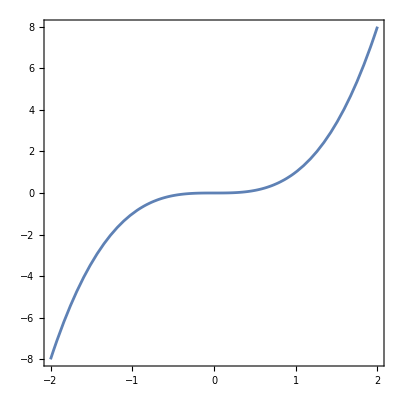

```mathematica
ParametricPlot[{t,t^3},{t,-2,2},Frame->True,AspectRatio->1]
```

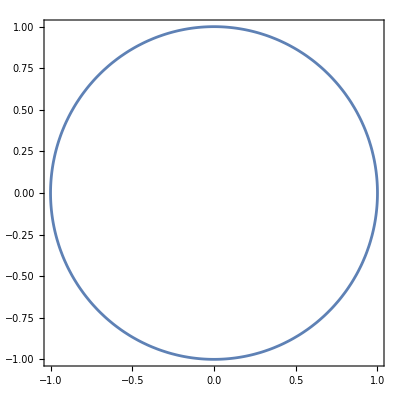

```mathematica
ParametricPlot[{Cos[t],Sin[t]},{t,0,2π},Frame->True,AspectRatio->1]
```

### 1.1.2 Path integrals

The scalar line integral of the function f along a curve C={r(u)∈ℝ^n,a≤u≤b} is given by:

-Graphics-"∮_C f(x)ⅆx=∫_a^b f(r(u)) Norm[r'(u)]ⅆu"

∫_a^b f(X_t) ⅆ X_t=∫_a^b f(X_t) ⅆt=∫_a^b f(X_t)dX_t/dt ⅆt

```mathematica
LineIntegrate[1,{x,y}∈ParametricRegion[{Cos[t],Sin[t]},{{t,0,2Pi}}]]
```

2 π

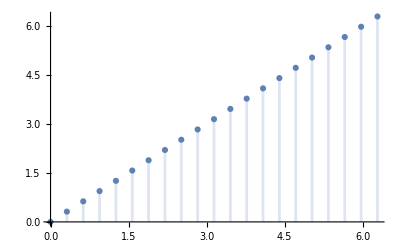

```mathematica
DiscretePlot[LineIntegrate[1,{x,y}∈ParametricRegion[{Cos[t],Sin[t]},{{t,0,z}}]],{z,0,2π,π/10}]
```

```mathematica
LineIntegrate[1,{x,y}∈ParametricRegion[{t,t^3},{{t,-2,2}}]]
```

2/9 (6 √145-(1+ⅈ) √6 EllipticF[ⅈ ArcSinh[(1+ⅈ) √6],-1])

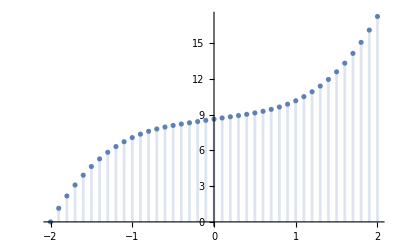

```mathematica
DiscretePlot[LineIntegrate[1,{x,y}∈ParametricRegion[{t,t^3},{{t,-2,z}}]],{z,-2,2,0.1}]
```

```mathematica
LineIntegrate[1,{x,y}∈ParametricRegion[{t^2,t^3},{{t,0,1}}]]
```

1/27 (-8+13 √13)

```mathematica
LineIntegrate[t^2,{x}∈ParametricRegion[{t^3},{{t,0,1}}]]
```

3/5

### 1.2.2 Examples

```mathematica
iterinteg[functions_,limits_,assumptions_]:=Fold[Integrate[#1*#2[[1]],#2[[2]],Assumptions->assumptions]&,1,Transpose[{functions,limits}]];
```

```mathematica
tensorfold[list_,dim_:2]:=If[Length[list]>=dim,ArrayReshape[list,ConstantArray[2,Log[2,Length[list]]]],list];
```

```mathematica
Map[tensorfold,{{1},{5,55},{25/2,475/3,350/3,3025/2},{125/6,1125/4,1375/6,18875/6,2125/12,7250/3,2000,166375/6}}]
```

{{1},{5,55},{{25/2,475/3},{350/3,3025/2}},{{{125/6,1125/4},{1375/6,18875/6}},{{2125/12,7250/3},{2000,166375/6}}}}

```mathematica
signat[paths_,limits_,level_:3]:=Module[{dpaths,dpathsf,integrands,ilimits,iassump,results},
dpaths=D[paths,t];
dpathsf=Map[Function[t,#]&,dpaths,{2}];
integrands=Table[Map[Tuples,Transpose[Table[Map[#[Subscript[t, j]]&,dpathsf,{2}],{j,1,k}]]],{k,1,level}];
ilimits=Table[Table[{Subscript[t, j],limits[[1]],If[j==k,limits[[2]],Subscript[t, j+1]]},{j,1,k}],{k,1,level}];
iassump=Fold[(#1&&(limits[[1]]<=Subscript[t, #2]<=limits[[2]]))&,(limits[[1]]<=Subscript[t, 1]<=limits[[2]]),Range[2,level]];
results=Table[Map[iterinteg[#,ilimits[[k]],iassump]&,integrands[[k]],{2}],{k,1,level}];
Map[tensorfold,Map[Prepend[#,{1}]&,Transpose[results]],{2}]
]
```

```mathematica
signat[{{3+t,(3+t)^2},{3+t,9+16t-t^2}},{0,5}]
```

{{{1},{5,55},{{25/2,475/3},{350/3,3025/2}},{{{125/6,1125/4},{1375/6,18875/6}},{{2125/12,7250/3},{2000,166375/6}}}},{{1},{5,55},{{25/2,350/3},{475/3,3025/2}},{{{125/6,2125/12},{1375/6,2000}},{{1125/4,7250/3},{18875/6,166375/6}}}}}

```mathematica
Grid[signat[{{3+t,(3+t)^2},{3+t,9+16t-t^2}},{0,5}],Frame->All]
```

{1} | {5,55} | {{25/2,475/3},{350/3,3025/2}} | {{{125/6,1125/4},{1375/6,18875/6}},{{2125/12,7250/3},{2000,166375/6}}}
{1} | {5,55} | {{25/2,350/3},{475/3,3025/2}} | {{{125/6,2125/12},{1375/6,2000}},{{1125/4,7250/3},{18875/6,166375/6}}}

```mathematica
krprod[list_]:=If[Length[list]==1,Flatten[list],Flatten[Apply[KroneckerProduct,list],1]];
```

```mathematica
Table[krprod[ConstantArray[{1,1},j]]/(j!),{j,1,4}]
```

{{1,1},{1/2,1/2,1/2,1/2},{1/6,1/6,1/6,1/6,1/6,1/6,1/6,1/6},{1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}}

## Shuffle Product

### Examples

```mathematica
5 55==475/3+350/3
```

True

```mathematica
475/3 5 ==1125/4+1125/4+1375/6
```

True

```mathematica
{Multinomial[2,0],Multinomial[1,1],Multinomial[0,2]}
```

{1,2,1}

```mathematica
{Multinomial[3,0],Multinomial[2,1],Multinomial[1,2],Multinomial[0,3]}
```

{1,3,3,1}

```mathematica
ws33=
{Multinomial[3,0,0],
Multinomial[2,1,0],Multinomial[2,0,1],
Multinomial[1,2,0],Multinomial[1,1,1],Multinomial[1,0,2],
Multinomial[0,3,0],Multinomial[0,2,1],Multinomial[0,1,2],Multinomial[0,0,3]}
```

{1,3,3,3,6,3,1,3,3,1}

```mathematica
Total[ws33]
```

27

```mathematica
IntegerPartitions[3]
```

{{3},{2,1},{1,1,1}}

```mathematica
Map[Factorial,IntegerPartitions[3],{2}]
```

{{6},{2,1},{1,1,1}}

```mathematica
Map[Apply[Times,#]&,Map[Factorial,IntegerPartitions[3],{2}]]
```

{6,2,1}

```mathematica
Map[(3!)/Apply[Times,#]&,Map[Factorial,IntegerPartitions[3],{2}]]
```

{1,3,6}

Enter ⧢

```mathematica
{1,2}⧢{a}={{a,1,2},{1,a,2},{1,2,a}}
```

```mathematica
Table[Grid[Flatten[Map[Permutations,IntegerPartitions[n]],1],Frame->True],{n,2,5}]
```

{2 | 
1 | 1,3 |  | 
2 | 1 | 
1 | 2 | 
1 | 1 | 1,4 |  |  | 
3 | 1 |  | 
1 | 3 |  | 
2 | 2 |  | 
2 | 1 | 1 | 
1 | 2 | 1 | 
1 | 1 | 2 | 
1 | 1 | 1 | 1,5 |  |  |  | 
4 | 1 |  |  | 
1 | 4 |  |  | 
3 | 2 |  |  | 
2 | 3 |  |  | 
3 | 1 | 1 |  | 
1 | 3 | 1 |  | 
1 | 1 | 3 |  | 
2 | 2 | 1 |  | 
2 | 1 | 2 |  | 
1 | 2 | 2 |  | 
2 | 1 | 1 | 1 | 
1 | 2 | 1 | 1 | 
1 | 1 | 2 | 1 | 
1 | 1 | 1 | 2 | 
1 | 1 | 1 | 1 | 1}

### Functions

```mathematica
spbrute[w1_,w2_]:=Module[{w12,n1,n2,n,perms,pos1,pos2,posf,post,res},
w12=Join[w1,w2];
n1=Length[w1];
n2=Length[w2];
n=n1+n2;
perms=Permutations[Range[n]];
pos1=Table[Apply[And,Map[(#>0)&,Differences[Table[First[FirstPosition[perms[[k]],j]],{j,1,n1}]]]],{k,1,n!}];
pos2=Table[Apply[And,Map[(#>0)&,Differences[Table[First[FirstPosition[perms[[k]],j]],{j,n1+1,n}]]]],{k,1,n!}];
posf=MapThread[And,{pos1,pos2}];
post=Pick[perms,posf];
res=Table[Table[w12[[(post[[k]])[[j]]]],{j,1,n}],{k,1,Length[post]}];
res
]
```

```mathematica
spbrute[{a},{d}]
```

{{a,d},{d,a}}

```mathematica
Timing[Map[Length,
{spbrute[{a},{f}],
spbrute[{a,b},{f,g}],
spbrute[{a,b,c},{f,g,h}],
spbrute[{a,b,c,d},{f,g,h,i}],
spbrute[{a,b,c,d,e},{f,g,h,i,j}]}]]
```

{152.451,{2,6,20,70,252}}

```mathematica
insertnew[word_,last_,new_]:=Module[{len,posi,pos},
len=Length[word];
posi=Position[word,last];
pos=If[posi=={},len,posi[[1,1]]];
Table[Join[Take[word,j],{new},Drop[word,j]],{j,pos,len}]];
```

```mathematica
signwords[level_:4]:=Module[
{c,res,lastres,adda,addb},
c=1;
res={{{Subscript[a, 1]},{Subscript[b, 1]}}};
While[c<level,
lastres=Last[res];
adda=Flatten[Map[insertnew[#,Subscript[a, c],Subscript[a, c+1]]&,Last[res]],1];
addb=Flatten[Map[insertnew[#,Subscript[b, c],Subscript[b, c+1]]&,Last[res]],1];
res=Append[res,Join[adda,addb]];
c=c+1;];
res];
```

```mathematica
shuffles2[setw_]:=Flatten[Table[{spbrute[w1,w2],Dot[w1,w2]},{w1,setw},{w2,setw}],1];
```

```mathematica
shuffles[set1]
```

{{{{s_1,s_1},{s_1,s_1}},s_1^2},{{{s_1,s_2},{s_2,s_1}},s_1 s_2},{{{s_2,s_1},{s_1,s_2}},s_1 s_2},{{{s_2,s_2},{s_2,s_2}},s_2^2}}

```mathematica
subjoin[list_]:=Module[{lett,subs},
lett=First[Apply[List,First[list]]];
subs=Map[ToString[Last[Apply[List,#]]]&,list];
Subscript[lett,ToExpression[Apply[StringJoin,subs]]]];
```

```mathematica
shuffles[setw_]:=Apply[Equal,Transpose[Flatten[Table[{Total[Map[subjoin,spbrute[w1,w2]]],Dot[{subjoin[w1]},{subjoin[w2]}]},{w1,setw},{w2,setw}],1]]];
```

```mathematica
shuffles2sets[set1_,set2_]:=Apply[Equal,Transpose[Flatten[Table[{Total[Map[subjoin,spbrute[w1,w2]]],Dot[{subjoin[w1]},{subjoin[w2]}]},{w1,set1},{w2,set2}],1]]];
```

```mathematica
filtereq[shuffs_,vars_]:=Apply[Equal,Transpose[Pick[Transpose[Apply[List,shuffs]],Map[(Length[Intersection[vars,Variables[#]]]>0)&,First[shuffs]]]]];
```

### Inputs

#### Level 2

```mathematica
vars1=Flatten[Table[Subscript[s,ToExpression[StringJoin[ToString[i]]]],{i,1,2}]]
```

{s_1,s_2}

```mathematica
set1=Table[{Subscript[s,i]},{i,1,2}]
```

{{s_1},{s_2}}

```mathematica
fund1={Subscript[s, 1],Subscript[s, 2]};
```

```mathematica
eqs2=shuffles[set1]
```

{2 s_11,s_12+s_21,s_12+s_21,2 s_22}=={s_1^2,s_1 s_2,s_1 s_2,s_2^2}

```mathematica
vars2=Flatten[Table[Subscript[s,ToExpression[StringJoin[ToString[i],ToString[j]]]],{i,1,2},{j,1,2}]]
```

{s_11,s_12,s_21,s_22}

```mathematica
sols2=First[Solve[eqs2,vars2]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_11→s_1^2/2,s_21→s_1 s_2-s_12,s_22→s_2^2/2}

```mathematica
fund2=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols2]]]
```

{s_1,s_2,s_12}

```mathematica
set2=Join[Table[{Subscript[s,j]},{j,1,2}],
Flatten[Table[{Subscript[s,i],Subscript[s,j]},{i,1,2},{j,1,2}],1]]
```

{{s_1},{s_2},{s_1,s_1},{s_1,s_2},{s_2,s_1},{s_2,s_2}}

```mathematica
set2s=Transpose[{Map[subjoin,set2],Map[subjoin,set2]/.sols2}];
```

```mathematica
Grid[set2s,Frame->All]
```

s_1 | s_1
s_2 | s_2
s_11 | s_1^2/2
s_12 | s_12
s_21 | s_1 s_2-s_12
s_22 | s_2^2/2

#### Level 3

```mathematica
vars3=Flatten[Table[Subscript[s,ToExpression[StringJoin[ToString[i],ToString[j],ToString[k]]]],{i,1,2},{j,1,2},{k,1,2}]]
```

{s_111,s_112,s_121,s_122,s_211,s_212,s_221,s_222}

```mathematica
{prod3,matrix3}=Normal[CoefficientArrays[Map[(First[#]-Last[#]==0)&,DeleteDuplicates[Transpose[Apply[List,eqs3]]]],vars3]];
```

```mathematica
Grid[matrix3]
```

3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3

```mathematica
-prod3
```

{s_1 s_11,s_1 s_12,s_1 s_21,s_1 s_22,s_2 s_11,s_2 s_12,s_2 s_21,s_2 s_22}

```mathematica
shuffles2sets[{{Subscript[s, 1]},{Subscript[s, 2]}},{{Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2]}}]
```

{3 s_111,2 s_112+s_121,s_121+2 s_211,s_122+s_212+s_221,s_112+s_121+s_211,2 s_122+s_212,s_212+2 s_221,3 s_222}=={s_1 s_11,s_1 s_12,s_1 s_21,s_1 s_22,s_2 s_11,s_2 s_12,s_2 s_21,s_2 s_22}

```mathematica
eqs3=filtereq[shuffles[set2],vars3]
```

{3 s_111,2 s_112+s_121,s_121+2 s_211,s_122+s_212+s_221,s_112+s_121+s_211,2 s_122+s_212,s_212+2 s_221,3 s_222,3 s_111,s_112+s_121+s_211,2 s_112+s_121,2 s_122+s_212,s_121+2 s_211,s_212+2 s_221,s_122+s_212+s_221,3 s_222}=={s_1 s_11,s_1 s_12,s_1 s_21,s_1 s_22,s_2 s_11,s_2 s_12,s_2 s_21,s_2 s_22,s_1 s_11,s_2 s_11,s_1 s_12,s_2 s_12,s_1 s_21,s_2 s_21,s_1 s_22,s_2 s_22}

```mathematica
sols3new=First[Solve[eqs3/.sols2,vars3]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_111→s_1^3/6,s_121→s_1 s_12-2 s_112,s_211→1/2 (s_1^2 s_2-2 s_1 s_12)+s_112,s_212→s_2 s_12-2 s_122,s_221→1/2 (s_1 s_2^2-2 s_2 s_12)+s_122,s_222→s_2^3/6}

```mathematica
fund3=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols3new]]]
```

{s_1,s_2,s_12,s_112,s_122}

```mathematica
sols3=Join[sols2,sols3new];
```

```mathematica
set3=Join[Table[{Subscript[s,j]},{j,1,2}],
Flatten[Table[{Subscript[s,i],Subscript[s,j]},{i,1,2},{j,1,2}],1],
Flatten[Table[{Subscript[s,i],Subscript[s,j],Subscript[s,k]},{i,1,2},{j,1,2},{k,1,2}],2]]
```

{{s_1},{s_2},{s_1,s_1},{s_1,s_2},{s_2,s_1},{s_2,s_2},{s_1,s_1,s_1},{s_1,s_1,s_2},{s_1,s_2,s_1},{s_1,s_2,s_2},{s_2,s_1,s_1},{s_2,s_1,s_2},{s_2,s_2,s_1},{s_2,s_2,s_2}}

```mathematica
set3s=Transpose[{Map[subjoin,set3],Map[subjoin,set3]/.sols3}];
```

```mathematica
Grid[set3s,Frame->All]
```

s_1 | s_1
s_2 | s_2
s_11 | s_1^2/2
s_12 | s_12
s_21 | s_1 s_2-s_12
s_22 | s_2^2/2
s_111 | s_1^3/6
s_112 | s_112
s_121 | s_1 s_12-2 s_112
s_122 | s_122
s_211 | 1/2 (s_1^2 s_2-2 s_1 s_12)+s_112
s_212 | s_2 s_12-2 s_122
s_221 | 1/2 (s_1 s_2^2-2 s_2 s_12)+s_122
s_222 | s_2^3/6

#### Level 4

```mathematica
vars4=Flatten[Table[Subscript[s,ToExpression[StringJoin[ToString[i],ToString[j],ToString[k],ToString[l]]]],{i,1,2},{j,1,2},{k,1,2},{l,1,2}]]
```

{s_1111,s_1112,s_1121,s_1122,s_1211,s_1212,s_1221,s_1222,s_2111,s_2112,s_2121,s_2122,s_2211,s_2212,s_2221,s_2222}

```mathematica
eqs4f3=filtereq[shuffles[set2],vars4]
```

{6 s_1111,3 s_1112+2 s_1121+s_1211,s_1121+2 s_1211+3 s_2111,s_1122+s_1212+s_1221+s_2112+s_2121+s_2211,3 s_1112+2 s_1121+s_1211,4 s_1122+2 s_1212,s_1212+2 s_1221+2 s_2112+s_2121,3 s_1222+2 s_2122+s_2212,s_1121+2 s_1211+3 s_2111,s_1212+2 s_1221+2 s_2112+s_2121,2 s_2121+4 s_2211,s_2122+2 s_2212+3 s_2221,s_1122+s_1212+s_1221+s_2112+s_2121+s_2211,3 s_1222+2 s_2122+s_2212,s_2122+2 s_2212+3 s_2221,6 s_2222}=={s_11^2,s_11 s_12,s_11 s_21,s_11 s_22,s_11 s_12,s_12^2,s_12 s_21,s_12 s_22,s_11 s_21,s_12 s_21,s_21^2,s_21 s_22,s_11 s_22,s_12 s_22,s_21 s_22,s_22^2}

```mathematica
Length[First[Solve[eqs4f3/.sols3,vars4]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

9

```mathematica
Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,Solve[eqs4f3/.sols3,vars4][[1]]]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_1,s_2,s_12,s_1112,s_1121,s_1122,s_1221,s_1222,s_2112,s_2122}

```mathematica
eqs4f4=filtereq[shuffles[set3],vars4]
```

{4 s_1111,3 s_1112+s_1121,2 s_1121+2 s_1211,2 s_1122+s_1212+s_1221,s_1211+3 s_2111,s_1212+2 s_2112+s_2121,s_1221+s_2121+2 s_2211,s_1222+s_2122+s_2212+s_2221,s_1112+s_1121+s_1211+s_2111,2 s_1122+s_1212+s_2112,s_1212+2 s_1221+s_2121,3 s_1222+s_2122,s_2112+s_2121+2 s_2211,2 s_2122+2 s_2212,s_2212+3 s_2221,4 s_2222,6 s_1111,3 s_1112+2 s_1121+s_1211,s_1121+2 s_1211+3 s_2111,s_1122+s_1212+s_1221+s_2112+s_2121+s_2211,3 s_1112+2 s_1121+s_1211,4 s_1122+2 s_1212,s_1212+2 s_1221+2 s_2112+s_2121,3 s_1222+2 s_2122+s_2212,s_1121+2 s_1211+3 s_2111,s_1212+2 s_1221+2 s_2112+s_2121,2 s_2121+4 s_2211,s_2122+2 s_2212+3 s_2221,s_1122+s_1212+s_1221+s_2112+s_2121+s_2211,3 s_1222+2 s_2122+s_2212,s_2122+2 s_2212+3 s_2221,6 s_2222,4 s_1111,s_1112+s_1121+s_1211+s_2111,3 s_1112+s_1121,2 s_1122+s_1212+s_2112,2 s_1121+2 s_1211,s_1212+2 s_1221+s_2121,2 s_1122+s_1212+s_1221,3 s_1222+s_2122,s_1211+3 s_2111,s_2112+s_2121+2 s_2211,s_1212+2 s_2112+s_2121,2 s_2122+2 s_2212,s_1221+s_2121+2 s_2211,s_2212+3 s_2221,s_1222+s_2122+s_2212+s_2221,4 s_2222}=={s_1 s_111,s_1 s_112,s_1 s_121,s_1 s_122,s_1 s_211,s_1 s_212,s_1 s_221,s_1 s_222,s_2 s_111,s_2 s_112,s_2 s_121,s_2 s_122,s_2 s_211,s_2 s_212,s_2 s_221,s_2 s_222,s_11^2,s_11 s_12,s_11 s_21,s_11 s_22,s_11 s_12,s_12^2,s_12 s_21,s_12 s_22,s_11 s_21,s_12 s_21,s_21^2,s_21 s_22,s_11 s_22,s_12 s_22,s_21 s_22,s_22^2,s_1 s_111,s_2 s_111,s_1 s_112,s_2 s_112,s_1 s_121,s_2 s_121,s_1 s_122,s_2 s_122,s_1 s_211,s_2 s_211,s_1 s_212,s_2 s_212,s_1 s_221,s_2 s_221,s_1 s_222,s_2 s_222}

```mathematica
Length[First[Solve[eqs4f4/.sols3,vars4]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

13

```mathematica
sols4new=First[Solve[eqs4f4/.sols3,vars4]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_1111→s_1^4/24,s_1121→s_1 s_112-3 s_1112,s_1211→1/2 (s_1^2 s_12-4 s_1 s_112)+3 s_1112,s_1212→s_12^2/2-2 s_1122,s_1221→1/2 (-s_12^2+2 s_1 s_122),s_2111→1/6 (s_1^3 s_2-3 s_1^2 s_12+6 s_1 s_112)-s_1112,s_2112→1/2 (-s_12^2+2 s_2 s_112),s_2121→1/2 (2 s_1 s_2 s_12+s_12^2-4 s_2 s_112-4 s_1 s_122)+2 s_1122,s_2122→s_2 s_122-3 s_1222,s_2211→1/4 (s_1^2 s_2^2-4 s_1 s_2 s_12+4 s_2 s_112+4 s_1 s_122)-s_1122,s_2212→1/2 (s_2^2 s_12-4 s_2 s_122)+3 s_1222,s_2221→1/6 (s_1 s_2^3-3 s_2^2 s_12+6 s_2 s_122)-s_1222,s_2222→s_2^4/24}

```mathematica
fund4=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols4new]]]
```

{s_1,s_2,s_12,s_112,s_122,s_1112,s_1122,s_1222}

```mathematica
{prod4,matrix4}=Normal[CoefficientArrays[Map[(First[#]-Last[#]==0)&,DeleteDuplicates[Transpose[Apply[List,eqs4f4]]]],vars4]];
```

```mathematica
Grid[matrix4]
```

4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4
6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 3 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 4 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 4 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6

```mathematica
-prod4
```

{s_1 s_111,s_1 s_112,s_1 s_121,s_1 s_122,s_1 s_211,s_1 s_212,s_1 s_221,s_1 s_222,s_2 s_111,s_2 s_112,s_2 s_121,s_2 s_122,s_2 s_211,s_2 s_212,s_2 s_221,s_2 s_222,s_11^2,s_11 s_12,s_11 s_21,s_11 s_22,s_12^2,s_12 s_21,s_12 s_22,s_21^2,s_21 s_22,s_22^2}

```mathematica
sols4test=First[Solve[shuffles2sets[
{{Subscript[s, 1]},{Subscript[s, 2]}},
{{Subscript[s, 1],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 2]},
{Subscript[s, 2],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 2]}}]/.sols3,vars4]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
sols4test2=First[Solve[shuffles2sets[
{{Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2]}},
{{Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2]}}]/.sols3,vars4]];
```

Solve::svars: Equations may not give solutions for all "solve" variables.

```mathematica
Length[sols4test]
```

12

```mathematica
Length[sols4test2]
```

9

```mathematica
fund4
```

{s_1,s_2,s_12,s_112,s_122,s_1112,s_1122,s_1222}

```mathematica
fund4test=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols4test]]]
```

{s_1,s_2,s_12,s_112,s_122,s_1112,s_1122,s_1212,s_1222}

```mathematica
fund4test2=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols4test2]]]
```

{s_1,s_2,s_12,s_1112,s_1121,s_1122,s_1221,s_1222,s_2112,s_2122}

```mathematica
DeleteElements[fund4test,fund4test2]
```

{s_112,s_122,s_1212}

```mathematica
Select[sols4test2,First[#]==Subscript[s, 1212]&]
```

{s_1212→s_12^2/2-2 s_1122}

```mathematica
Grid[FullSimplify[Transpose[{Sort[sols4new],Sort[Join[sols4test/.{Subscript[s, 1212]->Subscript[s, 12]^2/2-2 Subscript[s, 1122]},{Subscript[s, 1212]->Subscript[s, 12]^2/2-2 Subscript[s, 1122]}]]}]]]
```

s_1111→s_1^4/24 | s_1111→s_1^4/24
s_1121→s_1 s_112-3 s_1112 | s_1121→s_1 s_112-3 s_1112
s_1211→1/2 s_1^2 s_12-2 s_1 s_112+3 s_1112 | s_1211→1/2 s_1^2 s_12-2 s_1 s_112+3 s_1112
s_1212→1/2 (s_12^2-4 s_1122) | s_1212→1/2 (s_12^2-4 s_1122)
s_1221→-s_12^2/2+s_1 s_122 | s_1221→-s_12^2/2+s_1 s_122
s_2111→1/6 s_1 (s_1^2 s_2-3 s_1 s_12+6 s_112)-s_1112 | s_2111→1/6 s_1 (s_1^2 s_2-3 s_1 s_12+6 s_112)-s_1112
s_2112→-s_12^2/2+s_2 s_112 | s_2112→-s_12^2/2+s_2 s_112
s_2121→s_1 (s_2 s_12-2 s_122)+1/2 (s_12^2-4 s_2 s_112+4 s_1122) | s_2121→s_1 (s_2 s_12-2 s_122)+1/2 (s_12^2-4 s_2 s_112+4 s_1122)
s_2122→s_2 s_122-3 s_1222 | s_2122→s_2 s_122-3 s_1222
s_2211→1/4 s_1^2 s_2^2+s_2 s_112+s_1 (-s_2 s_12+s_122)-s_1122 | s_2211→1/4 s_1^2 s_2^2+s_2 s_112+s_1 (-s_2 s_12+s_122)-s_1122
s_2212→1/2 s_2^2 s_12-2 s_2 s_122+3 s_1222 | s_2212→1/2 s_2^2 s_12-2 s_2 s_122+3 s_1222
s_2221→1/6 s_2 (s_1 s_2^2-3 s_2 s_12+6 s_122)-s_1222 | s_2221→1/6 s_2 (s_1 s_2^2-3 s_2 s_12+6 s_122)-s_1222
s_2222→s_2^4/24 | s_2222→s_2^4/24

```mathematica
FullSimplify[Sort[sols4new]]==FullSimplify[Sort[Join[sols4test/.{Subscript[s, 1212]->Subscript[s, 12]^2/2-2 Subscript[s, 1122]},{Subscript[s, 1212]->Subscript[s, 12]^2/2-2 Subscript[s, 1122]}]]]
```

True

```mathematica
sols4=Join[sols3,sols4new];
```

```mathematica
set4=Join[Table[{Subscript[s,j]},{j,1,2}],
Flatten[Table[{Subscript[s,i],Subscript[s,j]},{i,1,2},{j,1,2}],1],
Flatten[Table[{Subscript[s,i],Subscript[s,j],Subscript[s,k]},{i,1,2},{j,1,2},{k,1,2}],2],
Flatten[Table[{Subscript[s,i],Subscript[s,j],Subscript[s,k],Subscript[s,l]},{i,1,2},{j,1,2},{k,1,2},{l,1,2}],3]]
```

{{s_1},{s_2},{s_1,s_1},{s_1,s_2},{s_2,s_1},{s_2,s_2},{s_1,s_1,s_1},{s_1,s_1,s_2},{s_1,s_2,s_1},{s_1,s_2,s_2},{s_2,s_1,s_1},{s_2,s_1,s_2},{s_2,s_2,s_1},{s_2,s_2,s_2},{s_1,s_1,s_1,s_1},{s_1,s_1,s_1,s_2},{s_1,s_1,s_2,s_1},{s_1,s_1,s_2,s_2},{s_1,s_2,s_1,s_1},{s_1,s_2,s_1,s_2},{s_1,s_2,s_2,s_1},{s_1,s_2,s_2,s_2},{s_2,s_1,s_1,s_1},{s_2,s_1,s_1,s_2},{s_2,s_1,s_2,s_1},{s_2,s_1,s_2,s_2},{s_2,s_2,s_1,s_1},{s_2,s_2,s_1,s_2},{s_2,s_2,s_2,s_1},{s_2,s_2,s_2,s_2}}

```mathematica
set4s=Transpose[{Map[subjoin,set4],Map[subjoin,set4]/.sols4}];
```

```mathematica
Grid[set4s,Frame->All]
```

s_1 | s_1
s_2 | s_2
s_11 | s_1^2/2
s_12 | s_12
s_21 | s_1 s_2-s_12
s_22 | s_2^2/2
s_111 | s_1^3/6
s_112 | s_112
s_121 | s_1 s_12-2 s_112
s_122 | s_122
s_211 | 1/2 (s_1^2 s_2-2 s_1 s_12)+s_112
s_212 | s_2 s_12-2 s_122
s_221 | 1/2 (s_1 s_2^2-2 s_2 s_12)+s_122
s_222 | s_2^3/6
s_1111 | s_1^4/24
s_1112 | s_1112
s_1121 | s_1 s_112-3 s_1112
s_1122 | s_1122
s_1211 | 1/2 (s_1^2 s_12-4 s_1 s_112)+3 s_1112
s_1212 | s_12^2/2-2 s_1122
s_1221 | 1/2 (-s_12^2+2 s_1 s_122)
s_1222 | s_1222
s_2111 | 1/6 (s_1^3 s_2-3 s_1^2 s_12+6 s_1 s_112)-s_1112
s_2112 | 1/2 (-s_12^2+2 s_2 s_112)
s_2121 | 1/2 (2 s_1 s_2 s_12+s_12^2-4 s_2 s_112-4 s_1 s_122)+2 s_1122
s_2122 | s_2 s_122-3 s_1222
s_2211 | 1/4 (s_1^2 s_2^2-4 s_1 s_2 s_12+4 s_2 s_112+4 s_1 s_122)-s_1122
s_2212 | 1/2 (s_2^2 s_12-4 s_2 s_122)+3 s_1222
s_2221 | 1/6 (s_1 s_2^3-3 s_2^2 s_12+6 s_2 s_122)-s_1222
s_2222 | s_2^4/24

#### Level 5

```mathematica
vars5=Flatten[Table[Subscript[s,ToExpression[StringJoin[ToString[i],ToString[j],ToString[k],ToString[l],ToString[m]]]],{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2}]]
```

{s_11111,s_11112,s_11121,s_11122,s_11211,s_11212,s_11221,s_11222,s_12111,s_12112,s_12121,s_12122,s_12211,s_12212,s_12221,s_12222,s_21111,s_21112,s_21121,s_21122,s_21211,s_21212,s_21221,s_21222,s_22111,s_22112,s_22121,s_22122,s_22211,s_22212,s_22221,s_22222}

```mathematica
Timing[eqs5f3=filtereq[shuffles[set3],vars5];]
```

{1.40024,Null}

```mathematica
Length[First[Solve[eqs5f3/.sols4,vars5]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

20

```mathematica
Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,First[Solve[eqs5f3/.sols4,vars5]]]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_1,s_2,s_12,s_112,s_122,s_11112,s_11121,s_11122,s_11212,s_11221,s_11222,s_12122,s_12221,s_12222,s_21112,s_21122,s_21222}

```mathematica
Timing[shfs4=shuffles[set4];]
```

{384.239,Null}

```mathematica
Timing[eqs5f4=filtereq[shfs4,vars5];]
```

{0.014419,Null}

```mathematica
Length[First[Solve[eqs5f4/.sols4,vars5]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

26

```mathematica
sols5new=First[Solve[eqs5f4/.sols4,vars5]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_11111→s_1^5/120,s_11121→s_1 s_1112-4 s_11112,s_11211→1/2 (s_1^2 s_112-6 s_1 s_1112)+6 s_11112,s_11221→s_1 s_1122-3 s_11122-s_11212,s_12111→1/6 (s_1^3 s_12-6 s_1^2 s_112+18 s_1 s_1112)-4 s_11112,s_12112→s_12 s_112-6 s_11122-3 s_11212,s_12121→1/2 (s_1 s_12^2-4 s_12 s_112-4 s_1 s_1122)+12 s_11122+4 s_11212,s_12211→1/2 (-s_1 s_12^2+2 s_12 s_112+s_1^2 s_122)-3 s_11122-s_11212,s_12212→s_12 s_122-6 s_11222-3 s_12122,s_12221→-s_12 s_122+s_1 s_1222+4 s_11222+2 s_12122,s_21111→1/24 (s_1^4 s_2-4 s_1^3 s_12+12 s_1^2 s_112-24 s_1 s_1112)+s_11112,s_21112→-s_12 s_112+s_2 s_1112+4 s_11122+2 s_11212,s_21121→1/2 (-s_1 s_12^2+2 s_1 s_2 s_112+4 s_12 s_112-6 s_2 s_1112)-6 s_11122-3 s_11212,s_21122→s_2 s_1122-3 s_11222-s_12122,s_21211→1/2 (s_1^2 s_2 s_12+s_1 s_12^2-4 s_1 s_2 s_112-2 s_12 s_112-2 s_1^2 s_122+6 s_2 s_1112+4 s_1 s_1122)+s_11212,s_21212→1/2 (s_2 s_12^2-4 s_12 s_122-4 s_2 s_1122)+12 s_11222+4 s_12122,s_21221→1/2 (-s_2 s_12^2+2 s_1 s_2 s_122+4 s_12 s_122-6 s_1 s_1222)-6 s_11222-3 s_12122,s_21222→s_2 s_1222-4 s_12222,s_22111→1/12 (s_1^3 s_2^2-6 s_1^2 s_2 s_12+12 s_1 s_2 s_112+6 s_1^2 s_122-12 s_2 s_1112-12 s_1 s_1122)+s_11122,s_22112→1/2 (-s_2 s_12^2+s_2^2 s_112+2 s_12 s_122)-3 s_11222-s_12122,s_22121→1/2 (s_1 s_2^2 s_12+s_2 s_12^2-2 s_2^2 s_112-4 s_1 s_2 s_122-2 s_12 s_122+4 s_2 s_1122+6 s_1 s_1222)+s_12122,s_22122→1/2 (s_2^2 s_122-6 s_2 s_1222)+6 s_12222,s_22211→1/12 (s_1^2 s_2^3-6 s_1 s_2^2 s_12+6 s_2^2 s_112+12 s_1 s_2 s_122-12 s_2 s_1122-12 s_1 s_1222)+s_11222,s_22212→1/6 (s_2^3 s_12-6 s_2^2 s_122+18 s_2 s_1222)-4 s_12222,s_22221→1/24 (s_1 s_2^4-4 s_2^3 s_12+12 s_2^2 s_122-24 s_2 s_1222)+s_12222,s_22222→s_2^5/120}

```mathematica
fund5=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols5new]]]
```

{s_1,s_2,s_12,s_112,s_122,s_1112,s_1122,s_1222,s_11112,s_11122,s_11212,s_11222,s_12122,s_12222}

```mathematica
DeleteElements[fund5,fund4]
```

{s_11112,s_11122,s_11212,s_11222,s_12122,s_12222}

```mathematica
sols5=Join[sols4,sols5new];
```

```mathematica
{prod5,matrix5}=Normal[CoefficientArrays[Map[(First[#]-Last[#]==0)&,DeleteDuplicates[Transpose[Apply[List,eqs5f4]]]],vars5]];
```

```mathematica
Grid[matrix5]
```

5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 4 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 4 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 5
10 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 6 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 3 | 0 | 4 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 3 | 0 | 2 | 2 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 4 | 3 | 0 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 6 | 0 | 3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2 | 4 | 0 | 0 | 2 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 3 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 2 | 0 | 0 | 0 | 0 | 3 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 2 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 4 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 3 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 3 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 4 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 3 | 0 | 6 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 2 | 0 | 3 | 4 | 0
0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 2 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 2 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 2 | 2 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 4 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 3 | 6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 10

```mathematica
-prod5
```

{s_1 s_1111,s_1 s_1112,s_1 s_1121,s_1 s_1122,s_1 s_1211,s_1 s_1212,s_1 s_1221,s_1 s_1222,s_1 s_2111,s_1 s_2112,s_1 s_2121,s_1 s_2122,s_1 s_2211,s_1 s_2212,s_1 s_2221,s_1 s_2222,s_2 s_1111,s_2 s_1112,s_2 s_1121,s_2 s_1122,s_2 s_1211,s_2 s_1212,s_2 s_1221,s_2 s_1222,s_2 s_2111,s_2 s_2112,s_2 s_2121,s_2 s_2122,s_2 s_2211,s_2 s_2212,s_2 s_2221,s_2 s_2222,s_11 s_111,s_11 s_112,s_11 s_121,s_11 s_122,s_11 s_211,s_11 s_212,s_11 s_221,s_11 s_222,s_12 s_111,s_12 s_112,s_12 s_121,s_12 s_122,s_12 s_211,s_12 s_212,s_12 s_221,s_12 s_222,s_21 s_111,s_21 s_112,s_21 s_121,s_21 s_122,s_21 s_211,s_21 s_212,s_21 s_221,s_21 s_222,s_22 s_111,s_22 s_112,s_22 s_121,s_22 s_122,s_22 s_211,s_22 s_212,s_22 s_221,s_22 s_222}

```mathematica
Timing[sols5test1=First[Solve[shuffles2sets[
{{Subscript[s, 1]},{Subscript[s, 2]}},
{{Subscript[s, 1],Subscript[s, 1],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 2],Subscript[s, 2]}}]/.sols4,vars5]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{0.109509,Null}

```mathematica
Length[sols5test1]
```

24

```mathematica
Timing[sols5test2=First[Solve[shuffles2sets[
{{Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2]}},
{{Subscript[s, 1],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 2]},
{Subscript[s, 2],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 2]}}]/.sols4,vars5]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{0.10219,Null}

```mathematica
Length[sols5test2]
```

20

```mathematica
fund5
```

{s_1,s_2,s_12,s_112,s_122,s_1112,s_1122,s_1222,s_11112,s_11122,s_11212,s_11222,s_12122,s_12222}

```mathematica
fund5test1=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols5test1]]]
```

{s_1,s_2,s_12,s_112,s_122,s_1112,s_1122,s_1222,s_11112,s_11122,s_11212,s_11222,s_12112,s_12122,s_12212,s_12222}

```mathematica
fund5test2=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols5test2]]]
```

{s_1,s_2,s_12,s_112,s_122,s_11112,s_11121,s_11122,s_11212,s_11221,s_11222,s_12122,s_12221,s_12222,s_21112,s_21122,s_21222}

```mathematica
DeleteElements[fund5test1,fund5test2]
```

{s_1112,s_1122,s_1222,s_12112,s_12212}

```mathematica
Select[sols5test2,Or[First[#]==Subscript[s, 12112],First[#]==Subscript[s, 12212]]&]
```

{s_12112→s_12 s_112-6 s_11122-3 s_11212,s_12212→s_12 s_122-6 s_11222-3 s_12122}

```mathematica
Expand[Sort[sols5new]]==Expand[Sort[Join[sols5test1/.{Subscript[s, 12112]->Subscript[s, 12] Subscript[s, 112]-6 Subscript[s, 11122]-3 Subscript[s, 11212],Subscript[s, 12212]->Subscript[s, 12] Subscript[s, 122]-6 Subscript[s, 11222]-3 Subscript[s, 12122]},
{Subscript[s, 12112]->Subscript[s, 12] Subscript[s, 112]-6 Subscript[s, 11122]-3 Subscript[s, 11212],Subscript[s, 12212]->Subscript[s, 12] Subscript[s, 122]-6 Subscript[s, 11222]-3 Subscript[s, 12122]}]]]
```

True

```mathematica
set5=Join[Table[{Subscript[s,j]},{j,1,2}],
Flatten[Table[{Subscript[s,i],Subscript[s,j]},{i,1,2},{j,1,2}],1],
Flatten[Table[{Subscript[s,i],Subscript[s,j],Subscript[s,k]},{i,1,2},{j,1,2},{k,1,2}],2],
Flatten[Table[{Subscript[s,i],Subscript[s,j],Subscript[s,k],Subscript[s,l]},{i,1,2},{j,1,2},{k,1,2},{l,1,2}],3],
Flatten[Table[{Subscript[s,i],Subscript[s,j],Subscript[s,k],Subscript[s,l],Subscript[s,m]},{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2}],4]]
```

{{s_1},{s_2},{s_1,s_1},{s_1,s_2},{s_2,s_1},{s_2,s_2},{s_1,s_1,s_1},{s_1,s_1,s_2},{s_1,s_2,s_1},{s_1,s_2,s_2},{s_2,s_1,s_1},{s_2,s_1,s_2},{s_2,s_2,s_1},{s_2,s_2,s_2},{s_1,s_1,s_1,s_1},{s_1,s_1,s_1,s_2},{s_1,s_1,s_2,s_1},{s_1,s_1,s_2,s_2},{s_1,s_2,s_1,s_1},{s_1,s_2,s_1,s_2},{s_1,s_2,s_2,s_1},{s_1,s_2,s_2,s_2},{s_2,s_1,s_1,s_1},{s_2,s_1,s_1,s_2},{s_2,s_1,s_2,s_1},{s_2,s_1,s_2,s_2},{s_2,s_2,s_1,s_1},{s_2,s_2,s_1,s_2},{s_2,s_2,s_2,s_1},{s_2,s_2,s_2,s_2},{s_1,s_1,s_1,s_1,s_1},{s_1,s_1,s_1,s_1,s_2},{s_1,s_1,s_1,s_2,s_1},{s_1,s_1,s_1,s_2,s_2},{s_1,s_1,s_2,s_1,s_1},{s_1,s_1,s_2,s_1,s_2},{s_1,s_1,s_2,s_2,s_1},{s_1,s_1,s_2,s_2,s_2},{s_1,s_2,s_1,s_1,s_1},{s_1,s_2,s_1,s_1,s_2},{s_1,s_2,s_1,s_2,s_1},{s_1,s_2,s_1,s_2,s_2},{s_1,s_2,s_2,s_1,s_1},{s_1,s_2,s_2,s_1,s_2},{s_1,s_2,s_2,s_2,s_1},{s_1,s_2,s_2,s_2,s_2},{s_2,s_1,s_1,s_1,s_1},{s_2,s_1,s_1,s_1,s_2},{s_2,s_1,s_1,s_2,s_1},{s_2,s_1,s_1,s_2,s_2},{s_2,s_1,s_2,s_1,s_1},{s_2,s_1,s_2,s_1,s_2},{s_2,s_1,s_2,s_2,s_1},{s_2,s_1,s_2,s_2,s_2},{s_2,s_2,s_1,s_1,s_1},{s_2,s_2,s_1,s_1,s_2},{s_2,s_2,s_1,s_2,s_1},{s_2,s_2,s_1,s_2,s_2},{s_2,s_2,s_2,s_1,s_1},{s_2,s_2,s_2,s_1,s_2},{s_2,s_2,s_2,s_2,s_1},{s_2,s_2,s_2,s_2,s_2}}

```mathematica
set5s=Transpose[{Map[subjoin,set5],Map[subjoin,set5]/.sols5}];
```

```mathematica
Grid[set5s,Frame->All]
```

s_1 | s_1
s_2 | s_2
s_11 | s_1^2/2
s_12 | s_12
s_21 | s_1 s_2-s_12
s_22 | s_2^2/2
s_111 | s_1^3/6
s_112 | s_112
s_121 | s_1 s_12-2 s_112
s_122 | s_122
s_211 | 1/2 (s_1^2 s_2-2 s_1 s_12)+s_112
s_212 | s_2 s_12-2 s_122
s_221 | 1/2 (s_1 s_2^2-2 s_2 s_12)+s_122
s_222 | s_2^3/6
s_1111 | s_1^4/24
s_1112 | s_1112
s_1121 | s_1 s_112-3 s_1112
s_1122 | s_1122
s_1211 | 1/2 (s_1^2 s_12-4 s_1 s_112)+3 s_1112
s_1212 | s_12^2/2-2 s_1122
s_1221 | 1/2 (-s_12^2+2 s_1 s_122)
s_1222 | s_1222
s_2111 | 1/6 (s_1^3 s_2-3 s_1^2 s_12+6 s_1 s_112)-s_1112
s_2112 | 1/2 (-s_12^2+2 s_2 s_112)
s_2121 | 1/2 (2 s_1 s_2 s_12+s_12^2-4 s_2 s_112-4 s_1 s_122)+2 s_1122
s_2122 | s_2 s_122-3 s_1222
s_2211 | 1/4 (s_1^2 s_2^2-4 s_1 s_2 s_12+4 s_2 s_112+4 s_1 s_122)-s_1122
s_2212 | 1/2 (s_2^2 s_12-4 s_2 s_122)+3 s_1222
s_2221 | 1/6 (s_1 s_2^3-3 s_2^2 s_12+6 s_2 s_122)-s_1222
s_2222 | s_2^4/24
s_11111 | s_1^5/120
s_11112 | s_11112
s_11121 | s_1 s_1112-4 s_11112
s_11122 | s_11122
s_11211 | 1/2 (s_1^2 s_112-6 s_1 s_1112)+6 s_11112
s_11212 | s_11212
s_11221 | s_1 s_1122-3 s_11122-s_11212
s_11222 | s_11222
s_12111 | 1/6 (s_1^3 s_12-6 s_1^2 s_112+18 s_1 s_1112)-4 s_11112
s_12112 | s_12 s_112-6 s_11122-3 s_11212
s_12121 | 1/2 (s_1 s_12^2-4 s_12 s_112-4 s_1 s_1122)+12 s_11122+4 s_11212
s_12122 | s_12122
s_12211 | 1/2 (-s_1 s_12^2+2 s_12 s_112+s_1^2 s_122)-3 s_11122-s_11212
s_12212 | s_12 s_122-6 s_11222-3 s_12122
s_12221 | -s_12 s_122+s_1 s_1222+4 s_11222+2 s_12122
s_12222 | s_12222
s_21111 | 1/24 (s_1^4 s_2-4 s_1^3 s_12+12 s_1^2 s_112-24 s_1 s_1112)+s_11112
s_21112 | -s_12 s_112+s_2 s_1112+4 s_11122+2 s_11212
s_21121 | 1/2 (-s_1 s_12^2+2 s_1 s_2 s_112+4 s_12 s_112-6 s_2 s_1112)-6 s_11122-3 s_11212
s_21122 | s_2 s_1122-3 s_11222-s_12122
s_21211 | 1/2 (s_1^2 s_2 s_12+s_1 s_12^2-4 s_1 s_2 s_112-2 s_12 s_112-2 s_1^2 s_122+6 s_2 s_1112+4 s_1 s_1122)+s_11212
s_21212 | 1/2 (s_2 s_12^2-4 s_12 s_122-4 s_2 s_1122)+12 s_11222+4 s_12122
s_21221 | 1/2 (-s_2 s_12^2+2 s_1 s_2 s_122+4 s_12 s_122-6 s_1 s_1222)-6 s_11222-3 s_12122
s_21222 | s_2 s_1222-4 s_12222
s_22111 | 1/12 (s_1^3 s_2^2-6 s_1^2 s_2 s_12+12 s_1 s_2 s_112+6 s_1^2 s_122-12 s_2 s_1112-12 s_1 s_1122)+s_11122
s_22112 | 1/2 (-s_2 s_12^2+s_2^2 s_112+2 s_12 s_122)-3 s_11222-s_12122
s_22121 | 1/2 (s_1 s_2^2 s_12+s_2 s_12^2-2 s_2^2 s_112-4 s_1 s_2 s_122-2 s_12 s_122+4 s_2 s_1122+6 s_1 s_1222)+s_12122
s_22122 | 1/2 (s_2^2 s_122-6 s_2 s_1222)+6 s_12222
s_22211 | 1/12 (s_1^2 s_2^3-6 s_1 s_2^2 s_12+6 s_2^2 s_112+12 s_1 s_2 s_122-12 s_2 s_1122-12 s_1 s_1222)+s_11222
s_22212 | 1/6 (s_2^3 s_12-6 s_2^2 s_122+18 s_2 s_1222)-4 s_12222
s_22221 | 1/24 (s_1 s_2^4-4 s_2^3 s_12+12 s_2^2 s_122-24 s_2 s_1222)+s_12222
s_22222 | s_2^5/120

#### Level 6

```mathematica
vars6=Flatten[Table[Subscript[s,ToExpression[StringJoin[ToString[i],ToString[j],ToString[k],ToString[l],ToString[m],ToString[n]]]],
{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2},{n,1,2}]]
```

{s_111111,s_111112,s_111121,s_111122,s_111211,s_111212,s_111221,s_111222,s_112111,s_112112,s_112121,s_112122,s_112211,s_112212,s_112221,s_112222,s_121111,s_121112,s_121121,s_121122,s_121211,s_121212,s_121221,s_121222,s_122111,s_122112,s_122121,s_122122,s_122211,s_122212,s_122221,s_122222,s_211111,s_211112,s_211121,s_211122,s_211211,s_211212,s_211221,s_211222,s_212111,s_212112,s_212121,s_212122,s_212211,s_212212,s_212221,s_212222,s_221111,s_221112,s_221121,s_221122,s_221211,s_221212,s_221221,s_221222,s_222111,s_222112,s_222121,s_222122,s_222211,s_222212,s_222221,s_222222}

```mathematica
Timing[sols6s1v5=First[Solve[shuffles2sets[
{{Subscript[s, 1]},{Subscript[s, 2]}},
{{Subscript[s, 1],Subscript[s, 1],Subscript[s, 1],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 1],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 1],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 1],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 2],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 2],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 2],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 2],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 1],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 1],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 1],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 1],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 2],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 2],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 2],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 2],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 1],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 1],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 1],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 1],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 2],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 2],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 2],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 2],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 1],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 1],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 1],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 1],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 2],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 2],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 2],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 2],Subscript[s, 2],Subscript[s, 2]}}]/.sols5,vars6]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{1.23281,Null}

```mathematica
Timing[sols6s2v4=First[Solve[shuffles2sets[
{{Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2]}},
{{Subscript[s, 1],Subscript[s, 1],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 2],Subscript[s, 2]}}]/.Join[sols5,sols6s1v5],vars6]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{1.33966,Null}

```mathematica
sols6s2v4
```

{s_121112→s_12 s_1112-8 s_111122-4 s_111212-2 s_112112,s_121122→s_12 s_1122-9 s_111222-4 s_112122-s_112212,s_121212→1/6 (s_12^3-12 s_12 s_1122)+12 s_111222+4 s_112122,s_122212→s_12 s_1222-8 s_112222-4 s_121222-2 s_122122}

```mathematica
Timing[sols6s3v3=First[Solve[shuffles2sets[
{{Subscript[s, 1],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 2]}},
{{Subscript[s, 1],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 1],Subscript[s, 2],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 1],Subscript[s, 2]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 1]},{Subscript[s, 2],Subscript[s, 2],Subscript[s, 2]}}]/.Join[sols5,sols6s1v5/.sols6s2v4,sols6s2v4],vars6]];]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{1.29281,Null}

```mathematica
sols6s3v3
```

{s_112112→s_112^2/2-6 s_111122-3 s_111212,s_122112→1/6 (-s_12^3+6 s_112 s_122)-3 s_111222-s_112122,s_122122→s_122^2/2-6 s_112222-3 s_121222}

```mathematica
Map[Length,{sols6s1v5,sols6s2v4,sols6s3v3}]
```

{48,4,3}

```mathematica
fund6s1v5=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols6s1v5]]]
```

{s_1,s_2,s_12,s_112,s_122,s_1112,s_1122,s_1222,s_11112,s_11122,s_11212,s_11222,s_12122,s_12222,s_111112,s_111122,s_111212,s_111222,s_112112,s_112122,s_112212,s_112222,s_121112,s_121122,s_121212,s_121222,s_122112,s_122122,s_122212,s_122222}

```mathematica
fund6s2v4=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols6s2v4]]]
```

{s_12,s_1112,s_1122,s_1222,s_111122,s_111212,s_111222,s_112112,s_112122,s_112212,s_112222,s_121222,s_122122}

```mathematica
fund6s3v3=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols6s3v3]]]
```

{s_12,s_112,s_122,s_111122,s_111212,s_111222,s_112122,s_112222,s_121222}

```mathematica
DeleteElements[fund6s2v4,fund6s1v5]
```

{}

```mathematica
DeleteElements[fund6s3v3,fund6s1v5]
```

{}

```mathematica
sols6new=Join[sols6s1v5/.sols6s2v4/.sols6s3v3,sols6s2v4/.sols6s3v3,sols6s3v3]
```

{s_111111→s_1^6/720,s_111121→s_1 s_11112-5 s_111112,s_111211→1/2 (s_1^2 s_1112-8 s_1 s_11112)+10 s_111112,s_111221→s_1 s_11122-4 s_111122-s_111212,s_112111→1/6 (s_1^3 s_112-9 s_1^2 s_1112+36 s_1 s_11112)-10 s_111112,s_112121→s_1 s_11212-2 (s_112^2/2-6 s_111122-3 s_111212)-3 s_111212,s_112211→s_112^2/2+1/2 (s_1^2 s_1122-6 s_1 s_11122-2 s_1 s_11212),s_112221→s_1 s_11222-3 s_111222-s_112122-s_112212,s_121111→1/24 (s_1^4 s_12-8 s_1^3 s_112+36 s_1^2 s_1112-96 s_1 s_11112)+5 s_111112,s_121121→s_1 (s_12 s_112-6 s_11122-3 s_11212)-3 (s_12 s_1112-8 s_111122-2 (s_112^2/2-6 s_111122-3 s_111212)-4 s_111212)-2 (s_112^2/2-6 s_111122-3 s_111212),s_121211→1/4 (s_1^2 s_12^2-8 s_1 s_12 s_112-4 s_1^2 s_1122+48 s_1 s_11122+16 s_1 s_11212)+3 (s_12 s_1112-8 s_111122-2 (s_112^2/2-6 s_111122-3 s_111212)-4 s_111212)+4 (s_112^2/2-6 s_111122-3 s_111212)+3 s_111212,s_121221→1/6 (-s_12^3+12 s_12 s_1122)+s_1 s_12122-12 s_111222-6 s_112122-2 (s_12 s_1122-9 s_111222-4 s_112122-s_112212),s_122111→-s_12 s_1112+1/12 (-3 s_1^2 s_12^2+12 s_1 s_12 s_112+2 s_1^3 s_122-36 s_1 s_11122-12 s_1 s_11212)+4 s_111122+s_111212,s_122121→1/6 (-s_12^3+12 s_12 s_1122)+s_1 (s_12 s_122-6 s_11222-3 s_12122)-12 s_111222-2 (1/6 (-s_12^3+6 s_112 s_122)-3 s_111222-s_112122)-4 s_112122-2 s_112212,s_122211→1/6 (-s_12^3+6 s_112 s_122)+s_12 s_1122+1/6 (s_12^3-12 s_12 s_1122)+1/2 (-2 s_1 s_12 s_122+s_1^2 s_1222+8 s_1 s_11222+4 s_1 s_12122)+3 s_111222+s_112122+s_112212,s_122221→s_122^2/2-s_12 s_1222+s_1 s_12222,s_211111→1/120 (s_1^5 s_2-5 s_1^4 s_12+20 s_1^3 s_112-60 s_1^2 s_1112+120 s_1 s_11112)-s_111112,s_211112→s_112^2/2-s_12 s_1112+s_2 s_11112,s_211121→-s_1 s_12 s_112+s_1 s_2 s_1112-4 s_2 s_11112+4 s_1 s_11122+2 s_1 s_11212+8 s_111122+3 (s_12 s_1112-8 s_111122-2 (s_112^2/2-6 s_111122-3 s_111212)-4 s_111212)+4 (s_112^2/2-6 s_111122-3 s_111212)+4 s_111212,s_211122→-s_12 s_1122+s_2 s_11122+6 s_111222+3 s_112122+s_112212,s_211211→1/4 (-s_1^2 s_12^2+2 s_1^2 s_2 s_112+8 s_1 s_12 s_112-12 s_1 s_2 s_1112+24 s_2 s_11112-24 s_1 s_11122-12 s_1 s_11212)-12 s_111122-3 (s_12 s_1112-8 s_111122-2 (s_112^2/2-6 s_111122-3 s_111212)-4 s_111212)-5 (s_112^2/2-6 s_111122-3 s_111212)-6 s_111212,s_211212→1/6 (-s_12^3+12 s_12 s_1122)+s_2 s_11212-12 s_111222-6 s_112122-2 s_112212,s_211221→s_1 s_2 s_1122+1/6 (s_12^3-12 s_12 s_1122)-3 s_2 s_11122-s_2 s_11212-3 s_1 s_11222-s_1 s_12122+21 s_111222+9 s_112122+2 (s_12 s_1122-9 s_111222-4 s_112122-s_112212)+2 s_112212,s_211222→s_2 s_11222-4 s_112222-s_121222,s_212111→s_12 s_1112+1/12 (2 s_1^3 s_2 s_12+3 s_1^2 s_12^2-12 s_1^2 s_2 s_112-12 s_1 s_12 s_112-4 s_1^3 s_122+36 s_1 s_2 s_1112+12 s_1^2 s_1122-48 s_2 s_11112+12 s_1 s_11212)-s_111212,s_212112→1/6 (-s_12^3+12 s_12 s_1122)+s_2 (s_12 s_112-6 s_11122-3 s_11212)-12 s_111222-2 (1/6 (-s_12^3+6 s_112 s_122)-3 s_111222-s_112122)-4 s_112122-2 (s_12 s_1122-9 s_111222-4 s_112122-s_112212),s_212121→1/2 s_2 (s_1 s_12^2-4 s_12 s_112-4 s_1 s_1122+24 s_11122+8 s_11212)-2 s_1 (s_12 s_122-6 s_11222-3 s_12122)-2 s_1 s_12122+4 (1/6 (-s_12^3+6 s_112 s_122)-3 s_111222-s_112122)+4 s_112122+3 (1/6 (s_12^3-12 s_12 s_1122)+12 s_111222+4 s_112122)+4 (s_12 s_1122-9 s_111222-4 s_112122-s_112212)+4 s_112212,s_212122→s_2 s_12122-2 (s_122^2/2-6 s_112222-3 s_121222)-3 s_121222,s_212211→1/2 (-s_1 s_2 s_12^2+2 s_2 s_12 s_112+s_1^2 s_2 s_122+4 s_1 s_12 s_122-3 s_1^2 s_1222-6 s_2 s_11122-2 s_2 s_11212-12 s_1 s_11222-6 s_1 s_12122)-9 s_111222-2 (1/6 (-s_12^3+6 s_112 s_122)-3 s_111222-s_112122)-6 s_112122-2 (1/6 (s_12^3-12 s_12 s_1122)+12 s_111222+4 s_112122)-3 (s_12 s_1122-9 s_111222-4 s_112122-s_112212)-4 s_112212,s_212212→s_2 (s_12 s_122-6 s_11222-3 s_12122)-3 (s_12 s_1222-8 s_112222-2 (s_122^2/2-6 s_112222-3 s_121222)-4 s_121222)-2 (s_122^2/2-6 s_112222-3 s_121222),s_212221→-s_2 (s_12 s_122-s_1 s_1222-4 s_11222-2 s_12122)-4 s_1 s_12222+8 s_112222+3 (s_12 s_1222-8 s_112222-2 (s_122^2/2-6 s_112222-3 s_121222)-4 s_121222)+4 (s_122^2/2-6 s_112222-3 s_121222)+4 s_121222,s_212222→s_2 s_12222-5 s_122222,s_221111→1/48 (s_1^4 s_2^2-8 s_1^3 s_2 s_12+24 s_1^2 s_2 s_112+8 s_1^3 s_122-48 s_1 s_2 s_1112-24 s_1^2 s_1122+48 s_2 s_11112+48 s_1 s_11122)-s_111122,s_221112→1/6 (-s_12^3+6 s_112 s_122)+1/6 (s_12^3-12 s_12 s_1122)+1/2 (-2 s_2 s_12 s_112+s_2^2 s_1112+8 s_2 s_11122+4 s_2 s_11212)+12 s_111222+5 s_112122+2 (s_12 s_1122-9 s_111222-4 s_112122-s_112212)+s_112212,s_221121→1/2 (-s_1 s_2 s_12^2+s_1 s_2^2 s_112+4 s_2 s_12 s_112+2 s_1 s_12 s_122-3 s_2^2 s_1112-12 s_2 s_11122-6 s_2 s_11212-6 s_1 s_11222-2 s_1 s_12122)-9 s_111222-2 (1/6 (-s_12^3+6 s_112 s_122)-3 s_111222-s_112122)-6 s_112122-2 (1/6 (s_12^3-12 s_12 s_1122)+12 s_111222+4 s_112122)-4 (s_12 s_1122-9 s_111222-4 s_112122-s_112212)-3 s_112212,s_221122→s_122^2/2+1/2 (s_2^2 s_1122-6 s_2 s_11222-2 s_2 s_12122),s_221211→1/6 (-s_12^3+6 s_112 s_122)+1/6 (s_12^3-12 s_12 s_1122)+1/4 (s_1^2 s_2^2 s_12+2 s_1 s_2 s_12^2-4 s_1 s_2^2 s_112-4 s_2 s_12 s_112-4 s_1^2 s_2 s_122-4 s_1 s_12 s_122+6 s_2^2 s_1112+8 s_1 s_2 s_1122+6 s_1^2 s_1222+4 s_2 s_11212+4 s_1 s_12122)+18 s_111222+7 s_112122+2 (s_12 s_1122-9 s_111222-4 s_112122-s_112212)+2 s_112212,s_221212→1/4 (s_2^2 s_12^2-8 s_2 s_12 s_122-4 s_2^2 s_1122+48 s_2 s_11222+16 s_2 s_12122)+3 (s_12 s_1222-8 s_112222-2 (s_122^2/2-6 s_112222-3 s_121222)-4 s_121222)+4 (s_122^2/2-6 s_112222-3 s_121222)+3 s_121222,s_221221→1/4 (-s_2^2 s_12^2+2 s_1 s_2^2 s_122+8 s_2 s_12 s_122-12 s_1 s_2 s_1222-24 s_2 s_11222-12 s_2 s_12122+24 s_1 s_12222)-12 s_112222-3 (s_12 s_1222-8 s_112222-2 (s_122^2/2-6 s_112222-3 s_121222)-4 s_121222)-5 (s_122^2/2-6 s_112222-3 s_121222)-6 s_121222,s_221222→1/2 (s_2^2 s_1222-8 s_2 s_12222)+10 s_122222,s_222111→1/36 (s_1^3 s_2^3-9 s_1^2 s_2^2 s_12+18 s_1 s_2^2 s_112+18 s_1^2 s_2 s_122-18 s_2^2 s_1112-36 s_1 s_2 s_1122-18 s_1^2 s_1222+36 s_2 s_11122+36 s_1 s_11222)-s_111222,s_222112→-s_12 s_1222+1/12 (-3 s_2^2 s_12^2+2 s_2^3 s_112+12 s_2 s_12 s_122-36 s_2 s_11222-12 s_2 s_12122)+4 s_112222+s_121222,s_222121→s_12 s_1222+1/12 (2 s_1 s_2^3 s_12+3 s_2^2 s_12^2-4 s_2^3 s_112-12 s_1 s_2^2 s_122-12 s_2 s_12 s_122+12 s_2^2 s_1122+36 s_1 s_2 s_1222+12 s_2 s_12122-48 s_1 s_12222)-s_121222,s_222122→1/6 (s_2^3 s_122-9 s_2^2 s_1222+36 s_2 s_12222)-10 s_122222,s_222211→1/48 (s_1^2 s_2^4-8 s_1 s_2^3 s_12+8 s_2^3 s_112+24 s_1 s_2^2 s_122-24 s_2^2 s_1122-48 s_1 s_2 s_1222+48 s_2 s_11222+48 s_1 s_12222)-s_112222,s_222212→1/24 (s_2^4 s_12-8 s_2^3 s_122+36 s_2^2 s_1222-96 s_2 s_12222)+5 s_122222,s_222221→1/120 (s_1 s_2^5-5 s_2^4 s_12+20 s_2^3 s_122-60 s_2^2 s_1222+120 s_2 s_12222)-s_122222,s_222222→s_2^6/720,s_121112→s_12 s_1112-8 s_111122-2 (s_112^2/2-6 s_111122-3 s_111212)-4 s_111212,s_121122→s_12 s_1122-9 s_111222-4 s_112122-s_112212,s_121212→1/6 (s_12^3-12 s_12 s_1122)+12 s_111222+4 s_112122,s_122212→s_12 s_1222-8 s_112222-2 (s_122^2/2-6 s_112222-3 s_121222)-4 s_121222,s_112112→s_112^2/2-6 s_111122-3 s_111212,s_122112→1/6 (-s_12^3+6 s_112 s_122)-3 s_111222-s_112122,s_122122→s_122^2/2-6 s_112222-3 s_121222}

```mathematica
sols6=Join[sols5,sols6new];
```

```mathematica
fund6=Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,sols6]]]
```

{s_1,s_2,s_12,s_112,s_122,s_1112,s_1122,s_1222,s_11112,s_11122,s_11212,s_11222,s_12122,s_12222,s_111112,s_111122,s_111212,s_111222,s_112122,s_112212,s_112222,s_121222,s_122222}

```mathematica
DeleteElements[fund6,fund5]
```

{s_111112,s_111122,s_111212,s_111222,s_112122,s_112212,s_112222,s_121222,s_122222}

```mathematica
set6=Join[Table[{Subscript[s,j]},
{j,1,2}],
Flatten[Table[{Subscript[s,i],Subscript[s,j]},
{i,1,2},{j,1,2}],1],
Flatten[Table[{Subscript[s,i],Subscript[s,j],Subscript[s,k]},
{i,1,2},{j,1,2},{k,1,2}],2],
Flatten[Table[{Subscript[s,i],Subscript[s,j],Subscript[s,k],Subscript[s,l]},
{i,1,2},{j,1,2},{k,1,2},{l,1,2}],3],
Flatten[Table[{Subscript[s,i],Subscript[s,j],Subscript[s,k],Subscript[s,l],Subscript[s,m]},
{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2}],4],
Flatten[Table[{Subscript[s,i],Subscript[s,j],Subscript[s,k],Subscript[s,l],Subscript[s,m],Subscript[s,n]},
{i,1,2},{j,1,2},{k,1,2},{l,1,2},{m,1,2},{n,1,2}],5]]
```

{{s_1},{s_2},{s_1,s_1},{s_1,s_2},{s_2,s_1},{s_2,s_2},{s_1,s_1,s_1},{s_1,s_1,s_2},{s_1,s_2,s_1},{s_1,s_2,s_2},{s_2,s_1,s_1},{s_2,s_1,s_2},{s_2,s_2,s_1},{s_2,s_2,s_2},{s_1,s_1,s_1,s_1},{s_1,s_1,s_1,s_2},{s_1,s_1,s_2,s_1},{s_1,s_1,s_2,s_2},{s_1,s_2,s_1,s_1},{s_1,s_2,s_1,s_2},{s_1,s_2,s_2,s_1},{s_1,s_2,s_2,s_2},{s_2,s_1,s_1,s_1},{s_2,s_1,s_1,s_2},{s_2,s_1,s_2,s_1},{s_2,s_1,s_2,s_2},{s_2,s_2,s_1,s_1},{s_2,s_2,s_1,s_2},{s_2,s_2,s_2,s_1},{s_2,s_2,s_2,s_2},{s_1,s_1,s_1,s_1,s_1},{s_1,s_1,s_1,s_1,s_2},{s_1,s_1,s_1,s_2,s_1},{s_1,s_1,s_1,s_2,s_2},{s_1,s_1,s_2,s_1,s_1},{s_1,s_1,s_2,s_1,s_2},{s_1,s_1,s_2,s_2,s_1},{s_1,s_1,s_2,s_2,s_2},{s_1,s_2,s_1,s_1,s_1},{s_1,s_2,s_1,s_1,s_2},{s_1,s_2,s_1,s_2,s_1},{s_1,s_2,s_1,s_2,s_2},{s_1,s_2,s_2,s_1,s_1},{s_1,s_2,s_2,s_1,s_2},{s_1,s_2,s_2,s_2,s_1},{s_1,s_2,s_2,s_2,s_2},{s_2,s_1,s_1,s_1,s_1},{s_2,s_1,s_1,s_1,s_2},{s_2,s_1,s_1,s_2,s_1},{s_2,s_1,s_1,s_2,s_2},{s_2,s_1,s_2,s_1,s_1},{s_2,s_1,s_2,s_1,s_2},{s_2,s_1,s_2,s_2,s_1},{s_2,s_1,s_2,s_2,s_2},{s_2,s_2,s_1,s_1,s_1},{s_2,s_2,s_1,s_1,s_2},{s_2,s_2,s_1,s_2,s_1},{s_2,s_2,s_1,s_2,s_2},{s_2,s_2,s_2,s_1,s_1},{s_2,s_2,s_2,s_1,s_2},{s_2,s_2,s_2,s_2,s_1},{s_2,s_2,s_2,s_2,s_2},{s_1,s_1,s_1,s_1,s_1,s_1},{s_1,s_1,s_1,s_1,s_1,s_2},{s_1,s_1,s_1,s_1,s_2,s_1},{s_1,s_1,s_1,s_1,s_2,s_2},{s_1,s_1,s_1,s_2,s_1,s_1},{s_1,s_1,s_1,s_2,s_1,s_2},{s_1,s_1,s_1,s_2,s_2,s_1},{s_1,s_1,s_1,s_2,s_2,s_2},{s_1,s_1,s_2,s_1,s_1,s_1},{s_1,s_1,s_2,s_1,s_1,s_2},{s_1,s_1,s_2,s_1,s_2,s_1},{s_1,s_1,s_2,s_1,s_2,s_2},{s_1,s_1,s_2,s_2,s_1,s_1},{s_1,s_1,s_2,s_2,s_1,s_2},{s_1,s_1,s_2,s_2,s_2,s_1},{s_1,s_1,s_2,s_2,s_2,s_2},{s_1,s_2,s_1,s_1,s_1,s_1},{s_1,s_2,s_1,s_1,s_1,s_2},{s_1,s_2,s_1,s_1,s_2,s_1},{s_1,s_2,s_1,s_1,s_2,s_2},{s_1,s_2,s_1,s_2,s_1,s_1},{s_1,s_2,s_1,s_2,s_1,s_2},{s_1,s_2,s_1,s_2,s_2,s_1},{s_1,s_2,s_1,s_2,s_2,s_2},{s_1,s_2,s_2,s_1,s_1,s_1},{s_1,s_2,s_2,s_1,s_1,s_2},{s_1,s_2,s_2,s_1,s_2,s_1},{s_1,s_2,s_2,s_1,s_2,s_2},{s_1,s_2,s_2,s_2,s_1,s_1},{s_1,s_2,s_2,s_2,s_1,s_2},{s_1,s_2,s_2,s_2,s_2,s_1},{s_1,s_2,s_2,s_2,s_2,s_2},{s_2,s_1,s_1,s_1,s_1,s_1},{s_2,s_1,s_1,s_1,s_1,s_2},{s_2,s_1,s_1,s_1,s_2,s_1},{s_2,s_1,s_1,s_1,s_2,s_2},{s_2,s_1,s_1,s_2,s_1,s_1},{s_2,s_1,s_1,s_2,s_1,s_2},{s_2,s_1,s_1,s_2,s_2,s_1},{s_2,s_1,s_1,s_2,s_2,s_2},{s_2,s_1,s_2,s_1,s_1,s_1},{s_2,s_1,s_2,s_1,s_1,s_2},{s_2,s_1,s_2,s_1,s_2,s_1},{s_2,s_1,s_2,s_1,s_2,s_2},{s_2,s_1,s_2,s_2,s_1,s_1},{s_2,s_1,s_2,s_2,s_1,s_2},{s_2,s_1,s_2,s_2,s_2,s_1},{s_2,s_1,s_2,s_2,s_2,s_2},{s_2,s_2,s_1,s_1,s_1,s_1},{s_2,s_2,s_1,s_1,s_1,s_2},{s_2,s_2,s_1,s_1,s_2,s_1},{s_2,s_2,s_1,s_1,s_2,s_2},{s_2,s_2,s_1,s_2,s_1,s_1},{s_2,s_2,s_1,s_2,s_1,s_2},{s_2,s_2,s_1,s_2,s_2,s_1},{s_2,s_2,s_1,s_2,s_2,s_2},{s_2,s_2,s_2,s_1,s_1,s_1},{s_2,s_2,s_2,s_1,s_1,s_2},{s_2,s_2,s_2,s_1,s_2,s_1},{s_2,s_2,s_2,s_1,s_2,s_2},{s_2,s_2,s_2,s_2,s_1,s_1},{s_2,s_2,s_2,s_2,s_1,s_2},{s_2,s_2,s_2,s_2,s_2,s_1},{s_2,s_2,s_2,s_2,s_2,s_2}}

```mathematica
set6s=Transpose[{Map[subjoin,set6],Map[subjoin,set6]/.sols6}];
```

```mathematica
Grid[set6s,Frame->All]
```

s_1 | s_1
s_2 | s_2
s_11 | s_1^2/2
s_12 | s_12
s_21 | s_1 s_2-s_12
s_22 | s_2^2/2
s_111 | s_1^3/6
s_112 | s_112
s_121 | s_1 s_12-2 s_112
s_122 | s_122
s_211 | 1/2 (s_1^2 s_2-2 s_1 s_12)+s_112
s_212 | s_2 s_12-2 s_122
s_221 | 1/2 (s_1 s_2^2-2 s_2 s_12)+s_122
s_222 | s_2^3/6
s_1111 | s_1^4/24
s_1112 | s_1112
s_1121 | s_1 s_112-3 s_1112
s_1122 | s_1122
s_1211 | 1/2 (s_1^2 s_12-4 s_1 s_112)+3 s_1112
s_1212 | s_12^2/2-2 s_1122
s_1221 | 1/2 (-s_12^2+2 s_1 s_122)
s_1222 | s_1222
s_2111 | 1/6 (s_1^3 s_2-3 s_1^2 s_12+6 s_1 s_112)-s_1112
s_2112 | 1/2 (-s_12^2+2 s_2 s_112)
s_2121 | 1/2 (2 s_1 s_2 s_12+s_12^2-4 s_2 s_112-4 s_1 s_122)+2 s_1122
s_2122 | s_2 s_122-3 s_1222
s_2211 | 1/4 (s_1^2 s_2^2-4 s_1 s_2 s_12+4 s_2 s_112+4 s_1 s_122)-s_1122
s_2212 | 1/2 (s_2^2 s_12-4 s_2 s_122)+3 s_1222
s_2221 | 1/6 (s_1 s_2^3-3 s_2^2 s_12+6 s_2 s_122)-s_1222
s_2222 | s_2^4/24
s_11111 | s_1^5/120
s_11112 | s_11112
s_11121 | s_1 s_1112-4 s_11112
s_11122 | s_11122
s_11211 | 1/2 (s_1^2 s_112-6 s_1 s_1112)+6 s_11112
s_11212 | s_11212
s_11221 | s_1 s_1122-3 s_11122-s_11212
s_11222 | s_11222
s_12111 | 1/6 (s_1^3 s_12-6 s_1^2 s_112+18 s_1 s_1112)-4 s_11112
s_12112 | s_12 s_112-6 s_11122-3 s_11212
s_12121 | 1/2 (s_1 s_12^2-4 s_12 s_112-4 s_1 s_1122)+12 s_11122+4 s_11212
s_12122 | s_12122
s_12211 | 1/2 (-s_1 s_12^2+2 s_12 s_112+s_1^2 s_122)-3 s_11122-s_11212
s_12212 | s_12 s_122-6 s_11222-3 s_12122
s_12221 | -s_12 s_122+s_1 s_1222+4 s_11222+2 s_12122
s_12222 | s_12222
s_21111 | 1/24 (s_1^4 s_2-4 s_1^3 s_12+12 s_1^2 s_112-24 s_1 s_1112)+s_11112
s_21112 | -s_12 s_112+s_2 s_1112+4 s_11122+2 s_11212
s_21121 | 1/2 (-s_1 s_12^2+2 s_1 s_2 s_112+4 s_12 s_112-6 s_2 s_1112)-6 s_11122-3 s_11212
s_21122 | s_2 s_1122-3 s_11222-s_12122
s_21211 | 1/2 (s_1^2 s_2 s_12+s_1 s_12^2-4 s_1 s_2 s_112-2 s_12 s_112-2 s_1^2 s_122+6 s_2 s_1112+4 s_1 s_1122)+s_11212
s_21212 | 1/2 (s_2 s_12^2-4 s_12 s_122-4 s_2 s_1122)+12 s_11222+4 s_12122
s_21221 | 1/2 (-s_2 s_12^2+2 s_1 s_2 s_122+4 s_12 s_122-6 s_1 s_1222)-6 s_11222-3 s_12122
s_21222 | s_2 s_1222-4 s_12222
s_22111 | 1/12 (s_1^3 s_2^2-6 s_1^2 s_2 s_12+12 s_1 s_2 s_112+6 s_1^2 s_122-12 s_2 s_1112-12 s_1 s_1122)+s_11122
s_22112 | 1/2 (-s_2 s_12^2+s_2^2 s_112+2 s_12 s_122)-3 s_11222-s_12122
s_22121 | 1/2 (s_1 s_2^2 s_12+s_2 s_12^2-2 s_2^2 s_112-4 s_1 s_2 s_122-2 s_12 s_122+4 s_2 s_1122+6 s_1 s_1222)+s_12122
s_22122 | 1/2 (s_2^2 s_122-6 s_2 s_1222)+6 s_12222
s_22211 | 1/12 (s_1^2 s_2^3-6 s_1 s_2^2 s_12+6 s_2^2 s_112+12 s_1 s_2 s_122-12 s_2 s_1122-12 s_1 s_1222)+s_11222
s_22212 | 1/6 (s_2^3 s_12-6 s_2^2 s_122+18 s_2 s_1222)-4 s_12222
s_22221 | 1/24 (s_1 s_2^4-4 s_2^3 s_12+12 s_2^2 s_122-24 s_2 s_1222)+s_12222
s_22222 | s_2^5/120
s_111111 | s_1^6/720
s_111112 | s_111112
s_111121 | s_1 s_11112-5 s_111112
s_111122 | s_111122
s_111211 | 1/2 (s_1^2 s_1112-8 s_1 s_11112)+10 s_111112
s_111212 | s_111212
s_111221 | s_1 s_11122-4 s_111122-s_111212
s_111222 | s_111222
s_112111 | 1/6 (s_1^3 s_112-9 s_1^2 s_1112+36 s_1 s_11112)-10 s_111112
s_112112 | s_112^2/2-6 s_111122-3 s_111212
s_112121 | s_1 s_11212-2 (s_112^2/2-6 s_111122-3 s_111212)-3 s_111212
s_112122 | s_112122
s_112211 | s_112^2/2+1/2 (s_1^2 s_1122-6 s_1 s_11122-2 s_1 s_11212)
s_112212 | s_112212
s_112221 | s_1 s_11222-3 s_111222-s_112122-s_112212
s_112222 | s_112222
s_121111 | 1/24 (s_1^4 s_12-8 s_1^3 s_112+36 s_1^2 s_1112-96 s_1 s_11112)+5 s_111112
s_121112 | s_12 s_1112-8 s_111122-2 (s_112^2/2-6 s_111122-3 s_111212)-4 s_111212
s_121121 | s_1 (s_12 s_112-6 s_11122-3 s_11212)-3 (s_12 s_1112-8 s_111122-2 (s_112^2/2-6 s_111122-3 s_111212)-4 s_111212)-2 (s_112^2/2-6 s_111122-3 s_111212)
s_121122 | s_12 s_1122-9 s_111222-4 s_112122-s_112212
s_121211 | 1/4 (s_1^2 s_12^2-8 s_1 s_12 s_112-4 s_1^2 s_1122+48 s_1 s_11122+16 s_1 s_11212)+3 (s_12 s_1112-8 s_111122-2 (s_112^2/2-6 s_111122-3 s_111212)-4 s_111212)+4 (s_112^2/2-6 s_111122-3 s_111212)+3 s_111212
s_121212 | 1/6 (s_12^3-12 s_12 s_1122)+12 s_111222+4 s_112122
s_121221 | 1/6 (-s_12^3+12 s_12 s_1122)+s_1 s_12122-12 s_111222-6 s_112122-2 (s_12 s_1122-9 s_111222-4 s_112122-s_112212)
s_121222 | s_121222
s_122111 | -s_12 s_1112+1/12 (-3 s_1^2 s_12^2+12 s_1 s_12 s_112+2 s_1^3 s_122-36 s_1 s_11122-12 s_1 s_11212)+4 s_111122+s_111212
s_122112 | 1/6 (-s_12^3+6 s_112 s_122)-3 s_111222-s_112122
s_122121 | 1/6 (-s_12^3+12 s_12 s_1122)+s_1 (s_12 s_122-6 s_11222-3 s_12122)-12 s_111222-2 (1/6 (-s_12^3+6 s_112 s_122)-3 s_111222-s_112122)-4 s_112122-2 s_112212
s_122122 | s_122^2/2-6 s_112222-3 s_121222
s_122211 | 1/6 (-s_12^3+6 s_112 s_122)+s_12 s_1122+1/6 (s_12^3-12 s_12 s_1122)+1/2 (-2 s_1 s_12 s_122+s_1^2 s_1222+8 s_1 s_11222+4 s_1 s_12122)+3 s_111222+s_112122+s_112212
s_122212 | s_12 s_1222-8 s_112222-2 (s_122^2/2-6 s_112222-3 s_121222)-4 s_121222
s_122221 | s_122^2/2-s_12 s_1222+s_1 s_12222
s_122222 | s_122222
s_211111 | 1/120 (s_1^5 s_2-5 s_1^4 s_12+20 s_1^3 s_112-60 s_1^2 s_1112+120 s_1 s_11112)-s_111112
s_211112 | s_112^2/2-s_12 s_1112+s_2 s_11112
s_211121 | -s_1 s_12 s_112+s_1 s_2 s_1112-4 s_2 s_11112+4 s_1 s_11122+2 s_1 s_11212+8 s_111122+3 (s_12 s_1112-8 s_111122-2 (s_112^2/2-6 s_111122-3 s_111212)-4 s_111212)+4 (s_112^2/2-6 s_111122-3 s_111212)+4 s_111212
s_211122 | -s_12 s_1122+s_2 s_11122+6 s_111222+3 s_112122+s_112212
s_211211 | 1/4 (-s_1^2 s_12^2+2 s_1^2 s_2 s_112+8 s_1 s_12 s_112-12 s_1 s_2 s_1112+24 s_2 s_11112-24 s_1 s_11122-12 s_1 s_11212)-12 s_111122-3 (s_12 s_1112-8 s_111122-2 (s_112^2/2-6 s_111122-3 s_111212)-4 s_111212)-5 (s_112^2/2-6 s_111122-3 s_111212)-6 s_111212
s_211212 | 1/6 (-s_12^3+12 s_12 s_1122)+s_2 s_11212-12 s_111222-6 s_112122-2 s_112212
s_211221 | s_1 s_2 s_1122+1/6 (s_12^3-12 s_12 s_1122)-3 s_2 s_11122-s_2 s_11212-3 s_1 s_11222-s_1 s_12122+21 s_111222+9 s_112122+2 (s_12 s_1122-9 s_111222-4 s_112122-s_112212)+2 s_112212
s_211222 | s_2 s_11222-4 s_112222-s_121222
s_212111 | s_12 s_1112+1/12 (2 s_1^3 s_2 s_12+3 s_1^2 s_12^2-12 s_1^2 s_2 s_112-12 s_1 s_12 s_112-4 s_1^3 s_122+36 s_1 s_2 s_1112+12 s_1^2 s_1122-48 s_2 s_11112+12 s_1 s_11212)-s_111212
s_212112 | 1/6 (-s_12^3+12 s_12 s_1122)+s_2 (s_12 s_112-6 s_11122-3 s_11212)-12 s_111222-2 (1/6 (-s_12^3+6 s_112 s_122)-3 s_111222-s_112122)-4 s_112122-2 (s_12 s_1122-9 s_111222-4 s_112122-s_112212)
s_212121 | 1/2 s_2 (s_1 s_12^2-4 s_12 s_112-4 s_1 s_1122+24 s_11122+8 s_11212)-2 s_1 (s_12 s_122-6 s_11222-3 s_12122)-2 s_1 s_12122+4 (1/6 (-s_12^3+6 s_112 s_122)-3 s_111222-s_112122)+4 s_112122+3 (1/6 (s_12^3-12 s_12 s_1122)+12 s_111222+4 s_112122)+4 (s_12 s_1122-9 s_111222-4 s_112122-s_112212)+4 s_112212
s_212122 | s_2 s_12122-2 (s_122^2/2-6 s_112222-3 s_121222)-3 s_121222
s_212211 | 1/2 (-s_1 s_2 s_12^2+2 s_2 s_12 s_112+s_1^2 s_2 s_122+4 s_1 s_12 s_122-3 s_1^2 s_1222-6 s_2 s_11122-2 s_2 s_11212-12 s_1 s_11222-6 s_1 s_12122)-9 s_111222-2 (1/6 (-s_12^3+6 s_112 s_122)-3 s_111222-s_112122)-6 s_112122-2 (1/6 (s_12^3-12 s_12 s_1122)+12 s_111222+4 s_112122)-3 (s_12 s_1122-9 s_111222-4 s_112122-s_112212)-4 s_112212
s_212212 | s_2 (s_12 s_122-6 s_11222-3 s_12122)-3 (s_12 s_1222-8 s_112222-2 (s_122^2/2-6 s_112222-3 s_121222)-4 s_121222)-2 (s_122^2/2-6 s_112222-3 s_121222)
s_212221 | -s_2 (s_12 s_122-s_1 s_1222-4 s_11222-2 s_12122)-4 s_1 s_12222+8 s_112222+3 (s_12 s_1222-8 s_112222-2 (s_122^2/2-6 s_112222-3 s_121222)-4 s_121222)+4 (s_122^2/2-6 s_112222-3 s_121222)+4 s_121222
s_212222 | s_2 s_12222-5 s_122222
s_221111 | 1/48 (s_1^4 s_2^2-8 s_1^3 s_2 s_12+24 s_1^2 s_2 s_112+8 s_1^3 s_122-48 s_1 s_2 s_1112-24 s_1^2 s_1122+48 s_2 s_11112+48 s_1 s_11122)-s_111122
s_221112 | 1/6 (-s_12^3+6 s_112 s_122)+1/6 (s_12^3-12 s_12 s_1122)+1/2 (-2 s_2 s_12 s_112+s_2^2 s_1112+8 s_2 s_11122+4 s_2 s_11212)+12 s_111222+5 s_112122+2 (s_12 s_1122-9 s_111222-4 s_112122-s_112212)+s_112212
s_221121 | 1/2 (-s_1 s_2 s_12^2+s_1 s_2^2 s_112+4 s_2 s_12 s_112+2 s_1 s_12 s_122-3 s_2^2 s_1112-12 s_2 s_11122-6 s_2 s_11212-6 s_1 s_11222-2 s_1 s_12122)-9 s_111222-2 (1/6 (-s_12^3+6 s_112 s_122)-3 s_111222-s_112122)-6 s_112122-2 (1/6 (s_12^3-12 s_12 s_1122)+12 s_111222+4 s_112122)-4 (s_12 s_1122-9 s_111222-4 s_112122-s_112212)-3 s_112212
s_221122 | s_122^2/2+1/2 (s_2^2 s_1122-6 s_2 s_11222-2 s_2 s_12122)
s_221211 | 1/6 (-s_12^3+6 s_112 s_122)+1/6 (s_12^3-12 s_12 s_1122)+1/4 (s_1^2 s_2^2 s_12+2 s_1 s_2 s_12^2-4 s_1 s_2^2 s_112-4 s_2 s_12 s_112-4 s_1^2 s_2 s_122-4 s_1 s_12 s_122+6 s_2^2 s_1112+8 s_1 s_2 s_1122+6 s_1^2 s_1222+4 s_2 s_11212+4 s_1 s_12122)+18 s_111222+7 s_112122+2 (s_12 s_1122-9 s_111222-4 s_112122-s_112212)+2 s_112212
s_221212 | 1/4 (s_2^2 s_12^2-8 s_2 s_12 s_122-4 s_2^2 s_1122+48 s_2 s_11222+16 s_2 s_12122)+3 (s_12 s_1222-8 s_112222-2 (s_122^2/2-6 s_112222-3 s_121222)-4 s_121222)+4 (s_122^2/2-6 s_112222-3 s_121222)+3 s_121222
s_221221 | 1/4 (-s_2^2 s_12^2+2 s_1 s_2^2 s_122+8 s_2 s_12 s_122-12 s_1 s_2 s_1222-24 s_2 s_11222-12 s_2 s_12122+24 s_1 s_12222)-12 s_112222-3 (s_12 s_1222-8 s_112222-2 (s_122^2/2-6 s_112222-3 s_121222)-4 s_121222)-5 (s_122^2/2-6 s_112222-3 s_121222)-6 s_121222
s_221222 | 1/2 (s_2^2 s_1222-8 s_2 s_12222)+10 s_122222
s_222111 | 1/36 (s_1^3 s_2^3-9 s_1^2 s_2^2 s_12+18 s_1 s_2^2 s_112+18 s_1^2 s_2 s_122-18 s_2^2 s_1112-36 s_1 s_2 s_1122-18 s_1^2 s_1222+36 s_2 s_11122+36 s_1 s_11222)-s_111222
s_222112 | -s_12 s_1222+1/12 (-3 s_2^2 s_12^2+2 s_2^3 s_112+12 s_2 s_12 s_122-36 s_2 s_11222-12 s_2 s_12122)+4 s_112222+s_121222
s_222121 | s_12 s_1222+1/12 (2 s_1 s_2^3 s_12+3 s_2^2 s_12^2-4 s_2^3 s_112-12 s_1 s_2^2 s_122-12 s_2 s_12 s_122+12 s_2^2 s_1122+36 s_1 s_2 s_1222+12 s_2 s_12122-48 s_1 s_12222)-s_121222
s_222122 | 1/6 (s_2^3 s_122-9 s_2^2 s_1222+36 s_2 s_12222)-10 s_122222
s_222211 | 1/48 (s_1^2 s_2^4-8 s_1 s_2^3 s_12+8 s_2^3 s_112+24 s_1 s_2^2 s_122-24 s_2^2 s_1122-48 s_1 s_2 s_1222+48 s_2 s_11222+48 s_1 s_12222)-s_112222
s_222212 | 1/24 (s_2^4 s_12-8 s_2^3 s_122+36 s_2^2 s_1222-96 s_2 s_12222)+5 s_122222
s_222221 | 1/120 (s_1 s_2^5-5 s_2^4 s_12+20 s_2^3 s_122-60 s_2^2 s_1222+120 s_2 s_12222)-s_122222
s_222222 | s_2^6/720

```mathematica
Map[Length,{fund2,fund3,fund4,fund5,fund6}]
```

{3,5,8,14,23}

#### Level 2, 3 variables

```mathematica
vars1={Subscript[s, 1],Subscript[s, 2],Subscript[s, 3]};
```

```mathematica
set1={{Subscript[s, 1]},{Subscript[s, 2]},{Subscript[s, 3]}};
```

```mathematica
fund1={Subscript[s, 1],Subscript[s, 2],Subscript[s, 3]};
```

```mathematica
shuffles[set1]
```

{2 s_11,s_12+s_21,s_13+s_31,s_12+s_21,2 s_22,s_23+s_32,s_13+s_31,s_23+s_32,2 s_33}=={s_1^2,s_1 s_2,s_1 s_3,s_1 s_2,s_2^2,s_2 s_3,s_1 s_3,s_2 s_3,s_3^2}

```mathematica
vars2=Flatten[Table[Subscript[s,ToExpression[StringJoin[ToString[i],ToString[j]]]],{i,1,3},{j,1,3}]]
```

{s_11,s_12,s_13,s_21,s_22,s_23,s_31,s_32,s_33}

```mathematica
Solve[shuffles[set1],vars2]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{s_11→s_1^2/2,s_21→s_1 s_2-s_12,s_22→s_2^2/2,s_31→s_1 s_3-s_13,s_32→s_2 s_3-s_23,s_33→s_3^2/2}}

```mathematica
fund2={
Subscript[s, 1] ,Subscript[s, 2],Subscript[s, 3],
Subscript[s, 12],Subscript[s, 13],Subscript[s, 23]};
```

```mathematica
sols2={Subscript[s, 11]->Subscript[s, 1]^2/2,Subscript[s, 21]->Subscript[s, 1] Subscript[s, 2]-Subscript[s, 12],Subscript[s, 22]->Subscript[s, 2]^2/2,Subscript[s, 31]->Subscript[s, 1] Subscript[s, 3]-Subscript[s, 13],Subscript[s, 32]->Subscript[s, 2] Subscript[s, 3]-Subscript[s, 23],Subscript[s, 33]->Subscript[s, 3]^2/2};
```

```mathematica
set2=Join[Table[{Subscript[s,j]},{j,1,3}],
Flatten[Table[{Subscript[s,i],Subscript[s,j]},{i,1,3},{j,1,3}],1]]
```

{{s_1},{s_2},{s_3},{s_1,s_1},{s_1,s_2},{s_1,s_3},{s_2,s_1},{s_2,s_2},{s_2,s_3},{s_3,s_1},{s_3,s_2},{s_3,s_3}}

```mathematica
set2s=Transpose[{Map[subjoin,set2],Map[subjoin,set2]/.sols2}];
```

```mathematica
Grid[set2s,Frame->All]
```

s_1 | s_1
s_2 | s_2
s_3 | s_3
s_11 | s_1^2/2
s_12 | s_12
s_13 | s_13
s_21 | s_1 s_2-s_12
s_22 | s_2^2/2
s_23 | s_23
s_31 | s_1 s_3-s_13
s_32 | s_2 s_3-s_23
s_33 | s_3^2/2

#### Level 3, 3 variables

```mathematica
vars3=Flatten[Table[Subscript[s,ToExpression[StringJoin[ToString[i],ToString[j],ToString[k]]]],{i,1,3},{j,1,3},{k,1,3}]]
```

{s_111,s_112,s_113,s_121,s_122,s_123,s_131,s_132,s_133,s_211,s_212,s_213,s_221,s_222,s_223,s_231,s_232,s_233,s_311,s_312,s_313,s_321,s_322,s_323,s_331,s_332,s_333}

```mathematica
eqs3=filtereq[shuffles[set2],vars3]
```

{3 s_111,2 s_112+s_121,2 s_113+s_131,s_121+2 s_211,s_122+s_212+s_221,s_123+s_213+s_231,s_131+2 s_311,s_132+s_312+s_321,s_133+s_313+s_331,s_112+s_121+s_211,2 s_122+s_212,s_123+s_132+s_213,s_212+2 s_221,3 s_222,2 s_223+s_232,s_231+s_312+s_321,s_232+2 s_322,s_233+s_323+s_332,s_113+s_131+s_311,s_123+s_132+s_312,2 s_133+s_313,s_213+s_231+s_321,s_223+s_232+s_322,2 s_233+s_323,s_313+2 s_331,s_323+2 s_332,3 s_333,3 s_111,s_112+s_121+s_211,s_113+s_131+s_311,2 s_112+s_121,2 s_122+s_212,s_123+s_132+s_312,2 s_113+s_131,s_123+s_132+s_213,2 s_133+s_313,s_121+2 s_211,s_212+2 s_221,s_213+s_231+s_321,s_122+s_212+s_221,3 s_222,s_223+s_232+s_322,s_123+s_213+s_231,2 s_223+s_232,2 s_233+s_323,s_131+2 s_311,s_231+s_312+s_321,s_313+2 s_331,s_132+s_312+s_321,s_232+2 s_322,s_323+2 s_332,s_133+s_313+s_331,s_233+s_323+s_332,3 s_333}=={s_1 s_11,s_1 s_12,s_1 s_13,s_1 s_21,s_1 s_22,s_1 s_23,s_1 s_31,s_1 s_32,s_1 s_33,s_2 s_11,s_2 s_12,s_2 s_13,s_2 s_21,s_2 s_22,s_2 s_23,s_2 s_31,s_2 s_32,s_2 s_33,s_3 s_11,s_3 s_12,s_3 s_13,s_3 s_21,s_3 s_22,s_3 s_23,s_3 s_31,s_3 s_32,s_3 s_33,s_1 s_11,s_2 s_11,s_3 s_11,s_1 s_12,s_2 s_12,s_3 s_12,s_1 s_13,s_2 s_13,s_3 s_13,s_1 s_21,s_2 s_21,s_3 s_21,s_1 s_22,s_2 s_22,s_3 s_22,s_1 s_23,s_2 s_23,s_3 s_23,s_1 s_31,s_2 s_31,s_3 s_31,s_1 s_32,s_2 s_32,s_3 s_32,s_1 s_33,s_2 s_33,s_3 s_33}

```mathematica
Solve[eqs3/.sols2,vars3]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{s_111→s_1^3/6,s_121→s_1 s_12-2 s_112,s_131→s_1 s_13-2 s_113,s_211→1/2 (s_1^2 s_2-2 s_1 s_12)+s_112,s_212→s_2 s_12-2 s_122,s_213→s_2 s_13-s_123-s_132,s_221→1/2 (s_1 s_2^2-2 s_2 s_12)+s_122,s_222→s_2^3/6,s_231→-s_2 s_13+s_1 s_23+s_132,s_232→s_2 s_23-2 s_223,s_311→1/2 (s_1^2 s_3-2 s_1 s_13)+s_113,s_312→s_3 s_12-s_123-s_132,s_313→s_3 s_13-2 s_133,s_321→s_1 s_2 s_3-s_3 s_12-s_1 s_23+s_123,s_322→1/2 (s_2^2 s_3-2 s_2 s_23)+s_223,s_323→s_3 s_23-2 s_233,s_331→1/2 (s_1 s_3^2-2 s_3 s_13)+s_133,s_332→1/2 (s_2 s_3^2-2 s_3 s_23)+s_233,s_333→s_3^3/6}}

```mathematica
Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,Solve[eqs3/.sols2,vars3][[1]]]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_1,s_2,s_3,s_12,s_13,s_23,s_112,s_113,s_122,s_123,s_132,s_133,s_223,s_233}

```mathematica
sols3=Join[sols2,{Subscript[s, 111]->Subscript[s, 1]^3/6,Subscript[s, 121]->Subscript[s, 1] Subscript[s, 12]-2 Subscript[s, 112],Subscript[s, 131]->Subscript[s, 1] Subscript[s, 13]-2 Subscript[s, 113],Subscript[s, 211]->1/2 (Subscript[s, 1]^2 Subscript[s, 2]-2 Subscript[s, 1] Subscript[s, 12])+Subscript[s, 112],Subscript[s, 212]->Subscript[s, 2] Subscript[s, 12]-2 Subscript[s, 122],Subscript[s, 213]->Subscript[s, 2] Subscript[s, 13]-Subscript[s, 123]-Subscript[s, 132],Subscript[s, 221]->1/2 (Subscript[s, 1] Subscript[s, 2]^2-2 Subscript[s, 2] Subscript[s, 12])+Subscript[s, 122],Subscript[s, 222]->Subscript[s, 2]^3/6,Subscript[s, 231]->-Subscript[s, 2] Subscript[s, 13]+Subscript[s, 1] Subscript[s, 23]+Subscript[s, 132],Subscript[s, 232]->Subscript[s, 2] Subscript[s, 23]-2 Subscript[s, 223],Subscript[s, 311]->1/2 (Subscript[s, 1]^2 Subscript[s, 3]-2 Subscript[s, 1] Subscript[s, 13])+Subscript[s, 113],Subscript[s, 312]->Subscript[s, 3] Subscript[s, 12]-Subscript[s, 123]-Subscript[s, 132],Subscript[s, 313]->Subscript[s, 3] Subscript[s, 13]-2 Subscript[s, 133],Subscript[s, 321]->Subscript[s, 1] Subscript[s, 2] Subscript[s, 3]-Subscript[s, 3] Subscript[s, 12]-Subscript[s, 1] Subscript[s, 23]+Subscript[s, 123],Subscript[s, 322]->1/2 (Subscript[s, 2]^2 Subscript[s, 3]-2 Subscript[s, 2] Subscript[s, 23])+Subscript[s, 223],Subscript[s, 323]->Subscript[s, 3] Subscript[s, 23]-2 Subscript[s, 233],Subscript[s, 331]->1/2 (Subscript[s, 1] Subscript[s, 3]^2-2 Subscript[s, 3] Subscript[s, 13])+Subscript[s, 133],Subscript[s, 332]->1/2 (Subscript[s, 2] Subscript[s, 3]^2-2 Subscript[s, 3] Subscript[s, 23])+Subscript[s, 233],Subscript[s, 333]->Subscript[s, 3]^3/6}];
```

```mathematica
fund3={
Subscript[s, 1] ,Subscript[s, 2],Subscript[s, 3],
Subscript[s, 12],Subscript[s, 13],Subscript[s, 23],
Subscript[s, 112],Subscript[s, 113],Subscript[s, 122],Subscript[s, 123],Subscript[s, 132],Subscript[s, 133],Subscript[s, 223],Subscript[s, 233]};
```

```mathematica
set3=Join[Table[{Subscript[s,j]},{j,1,3}],
Flatten[Table[{Subscript[s,i],Subscript[s,j]},{i,1,3},{j,1,3}],1],
Flatten[Table[{Subscript[s,i],Subscript[s,j],Subscript[s,k]},{i,1,3},{j,1,3},{k,1,3}],2]]
```

{{s_1},{s_2},{s_3},{s_1,s_1},{s_1,s_2},{s_1,s_3},{s_2,s_1},{s_2,s_2},{s_2,s_3},{s_3,s_1},{s_3,s_2},{s_3,s_3},{s_1,s_1,s_1},{s_1,s_1,s_2},{s_1,s_1,s_3},{s_1,s_2,s_1},{s_1,s_2,s_2},{s_1,s_2,s_3},{s_1,s_3,s_1},{s_1,s_3,s_2},{s_1,s_3,s_3},{s_2,s_1,s_1},{s_2,s_1,s_2},{s_2,s_1,s_3},{s_2,s_2,s_1},{s_2,s_2,s_2},{s_2,s_2,s_3},{s_2,s_3,s_1},{s_2,s_3,s_2},{s_2,s_3,s_3},{s_3,s_1,s_1},{s_3,s_1,s_2},{s_3,s_1,s_3},{s_3,s_2,s_1},{s_3,s_2,s_2},{s_3,s_2,s_3},{s_3,s_3,s_1},{s_3,s_3,s_2},{s_3,s_3,s_3}}

```mathematica
set3s=Transpose[{Map[subjoin,set3],Map[subjoin,set3]/.sols3}];
```

```mathematica
Grid[set3s,Frame->All]
```

s_1 | s_1
s_2 | s_2
s_3 | s_3
s_11 | s_1^2/2
s_12 | s_12
s_13 | s_13
s_21 | s_1 s_2-s_12
s_22 | s_2^2/2
s_23 | s_23
s_31 | s_1 s_3-s_13
s_32 | s_2 s_3-s_23
s_33 | s_3^2/2
s_111 | s_1^3/6
s_112 | s_112
s_113 | s_113
s_121 | s_1 s_12-2 s_112
s_122 | s_122
s_123 | s_123
s_131 | s_1 s_13-2 s_113
s_132 | s_132
s_133 | s_133
s_211 | 1/2 (s_1^2 s_2-2 s_1 s_12)+s_112
s_212 | s_2 s_12-2 s_122
s_213 | s_2 s_13-s_123-s_132
s_221 | 1/2 (s_1 s_2^2-2 s_2 s_12)+s_122
s_222 | s_2^3/6
s_223 | s_223
s_231 | -s_2 s_13+s_1 s_23+s_132
s_232 | s_2 s_23-2 s_223
s_233 | s_233
s_311 | 1/2 (s_1^2 s_3-2 s_1 s_13)+s_113
s_312 | s_3 s_12-s_123-s_132
s_313 | s_3 s_13-2 s_133
s_321 | s_1 s_2 s_3-s_3 s_12-s_1 s_23+s_123
s_322 | 1/2 (s_2^2 s_3-2 s_2 s_23)+s_223
s_323 | s_3 s_23-2 s_233
s_331 | 1/2 (s_1 s_3^2-2 s_3 s_13)+s_133
s_332 | 1/2 (s_2 s_3^2-2 s_3 s_23)+s_233
s_333 | s_3^3/6

#### Level 4, 3 variables

```mathematica
vars4=Flatten[Table[Subscript[s,ToExpression[StringJoin[ToString[i],ToString[j],ToString[k],ToString[l]]]],{i,1,3},{j,1,3},{k,1,3},{l,1,3}]]
```

{s_1111,s_1112,s_1113,s_1121,s_1122,s_1123,s_1131,s_1132,s_1133,s_1211,s_1212,s_1213,s_1221,s_1222,s_1223,s_1231,s_1232,s_1233,s_1311,s_1312,s_1313,s_1321,s_1322,s_1323,s_1331,s_1332,s_1333,s_2111,s_2112,s_2113,s_2121,s_2122,s_2123,s_2131,s_2132,s_2133,s_2211,s_2212,s_2213,s_2221,s_2222,s_2223,s_2231,s_2232,s_2233,s_2311,s_2312,s_2313,s_2321,s_2322,s_2323,s_2331,s_2332,s_2333,s_3111,s_3112,s_3113,s_3121,s_3122,s_3123,s_3131,s_3132,s_3133,s_3211,s_3212,s_3213,s_3221,s_3222,s_3223,s_3231,s_3232,s_3233,s_3311,s_3312,s_3313,s_3321,s_3322,s_3323,s_3331,s_3332,s_3333}

```mathematica
eqs4f3=filtereq[shuffles[set2],vars4]
```

{6 s_1111,3 s_1112+2 s_1121+s_1211,3 s_1113+2 s_1131+s_1311,s_1121+2 s_1211+3 s_2111,s_1122+s_1212+s_1221+s_2112+s_2121+s_2211,s_1123+s_1213+s_1231+s_2113+s_2131+s_2311,s_1131+2 s_1311+3 s_3111,s_1132+s_1312+s_1321+s_3112+s_3121+s_3211,s_1133+s_1313+s_1331+s_3113+s_3131+s_3311,3 s_1112+2 s_1121+s_1211,4 s_1122+2 s_1212,2 s_1123+2 s_1132+s_1213+s_1312,s_1212+2 s_1221+2 s_2112+s_2121,3 s_1222+2 s_2122+s_2212,2 s_1223+s_1232+s_2123+s_2132+s_2312,s_1231+s_1312+s_1321+2 s_3112+s_3121,s_1232+2 s_1322+2 s_3122+s_3212,s_1233+s_1323+s_1332+s_3123+s_3132+s_3312,3 s_1113+2 s_1131+s_1311,2 s_1123+2 s_1132+s_1213+s_1312,4 s_1133+2 s_1313,s_1213+s_1231+s_1321+2 s_2113+s_2131,s_1223+s_1232+s_1322+s_2123+s_2132+s_2213,2 s_1233+s_1323+2 s_2133+s_2313,s_1313+2 s_1331+2 s_3113+s_3131,s_1323+2 s_1332+s_3123+s_3132+s_3213,3 s_1333+2 s_3133+s_3313,s_1121+2 s_1211+3 s_2111,s_1212+2 s_1221+2 s_2112+s_2121,s_1213+s_1231+s_1321+2 s_2113+s_2131,2 s_2121+4 s_2211,s_2122+2 s_2212+3 s_2221,s_2123+2 s_2213+2 s_2231+s_2321,s_2131+2 s_2311+s_3121+2 s_3211,s_2132+s_2312+s_2321+s_3212+2 s_3221,s_2133+s_2313+s_2331+s_3213+s_3231+s_3321,s_1122+s_1212+s_1221+s_2112+s_2121+s_2211,3 s_1222+2 s_2122+s_2212,s_1223+s_1232+s_1322+s_2123+s_2132+s_2213,s_2122+2 s_2212+3 s_2221,6 s_2222,3 s_2223+2 s_2232+s_2322,s_2231+s_2312+s_2321+s_3122+s_3212+s_3221,s_2232+2 s_2322+3 s_3222,s_2233+s_2323+s_2332+s_3223+s_3232+s_3322,s_1123+s_1213+s_1231+s_2113+s_2131+s_2311,2 s_1223+s_1232+s_2123+s_2132+s_2312,2 s_1233+s_1323+2 s_2133+s_2313,s_2123+2 s_2213+2 s_2231+s_2321,3 s_2223+2 s_2232+s_2322,4 s_2233+2 s_2323,s_2313+2 s_2331+s_3123+s_3213+s_3231,s_2323+2 s_2332+2 s_3223+s_3232,3 s_2333+2 s_3233+s_3323,s_1131+2 s_1311+3 s_3111,s_1231+s_1312+s_1321+2 s_3112+s_3121,s_1313+2 s_1331+2 s_3113+s_3131,s_2131+2 s_2311+s_3121+2 s_3211,s_2231+s_2312+s_2321+s_3122+s_3212+s_3221,s_2313+2 s_2331+s_3123+s_3213+s_3231,2 s_3131+4 s_3311,s_3132+s_3231+2 s_3312+2 s_3321,s_3133+2 s_3313+3 s_3331,s_1132+s_1312+s_1321+s_3112+s_3121+s_3211,s_1232+2 s_1322+2 s_3122+s_3212,s_1323+2 s_1332+s_3123+s_3132+s_3213,s_2132+s_2312+s_2321+s_3212+2 s_3221,s_2232+2 s_2322+3 s_3222,s_2323+2 s_2332+2 s_3223+s_3232,s_3132+s_3231+2 s_3312+2 s_3321,2 s_3232+4 s_3322,s_3233+2 s_3323+3 s_3332,s_1133+s_1313+s_1331+s_3113+s_3131+s_3311,s_1233+s_1323+s_1332+s_3123+s_3132+s_3312,3 s_1333+2 s_3133+s_3313,s_2133+s_2313+s_2331+s_3213+s_3231+s_3321,s_2233+s_2323+s_2332+s_3223+s_3232+s_3322,3 s_2333+2 s_3233+s_3323,s_3133+2 s_3313+3 s_3331,s_3233+2 s_3323+3 s_3332,6 s_3333}=={s_11^2,s_11 s_12,s_11 s_13,s_11 s_21,s_11 s_22,s_11 s_23,s_11 s_31,s_11 s_32,s_11 s_33,s_11 s_12,s_12^2,s_12 s_13,s_12 s_21,s_12 s_22,s_12 s_23,s_12 s_31,s_12 s_32,s_12 s_33,s_11 s_13,s_12 s_13,s_13^2,s_13 s_21,s_13 s_22,s_13 s_23,s_13 s_31,s_13 s_32,s_13 s_33,s_11 s_21,s_12 s_21,s_13 s_21,s_21^2,s_21 s_22,s_21 s_23,s_21 s_31,s_21 s_32,s_21 s_33,s_11 s_22,s_12 s_22,s_13 s_22,s_21 s_22,s_22^2,s_22 s_23,s_22 s_31,s_22 s_32,s_22 s_33,s_11 s_23,s_12 s_23,s_13 s_23,s_21 s_23,s_22 s_23,s_23^2,s_23 s_31,s_23 s_32,s_23 s_33,s_11 s_31,s_12 s_31,s_13 s_31,s_21 s_31,s_22 s_31,s_23 s_31,s_31^2,s_31 s_32,s_31 s_33,s_11 s_32,s_12 s_32,s_13 s_32,s_21 s_32,s_22 s_32,s_23 s_32,s_31 s_32,s_32^2,s_32 s_33,s_11 s_33,s_12 s_33,s_13 s_33,s_21 s_33,s_22 s_33,s_23 s_33,s_31 s_33,s_32 s_33,s_33^2}

```mathematica
Length[First[Solve[eqs4f3/.sols3,vars4]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

39

```mathematica
eqs4f4=filtereq[shuffles[set3],vars4]
```

{4 s_1111,3 s_1112+s_1121,3 s_1113+s_1131,2 s_1121+2 s_1211,2 s_1122+s_1212+s_1221,2 s_1123+s_1213+s_1231,2 s_1131+2 s_1311,2 s_1132+s_1312+s_1321,2 s_1133+s_1313+s_1331,s_1211+3 s_2111,s_1212+2 s_2112+s_2121,s_1213+2 s_2113+s_2131,s_1221+s_2121+2 s_2211,s_1222+s_2122+s_2212+s_2221,s_1223+s_2123+s_2213+s_2231,s_1231+s_2131+2 s_2311,s_1232+s_2132+s_2312+s_2321,s_1233+s_2133+s_2313+s_2331,s_1311+3 s_3111,s_1312+2 s_3112+s_3121,s_1313+2 s_3113+s_3131,s_1321+s_3121+2 s_3211,s_1322+s_3122+s_3212+s_3221,s_1323+s_3123+s_3213+s_3231,s_1331+s_3131+2 s_3311,s_1332+s_3132+s_3312+s_3321,s_1333+s_3133+s_3313+s_3331,s_1112+s_1121+s_1211+s_2111,2 s_1122+s_1212+s_2112,s_1123+s_1132+s_1213+s_2113,s_1212+2 s_1221+s_2121,3 s_1222+s_2122,2 s_1223+s_1232+s_2123,s_1231+s_1312+s_1321+s_2131,s_1232+2 s_1322+s_2132,s_1233+s_1323+s_1332+s_2133,s_2112+s_2121+2 s_2211,2 s_2122+2 s_2212,s_2123+s_2132+2 s_2213,s_2212+3 s_2221,4 s_2222,3 s_2223+s_2232,2 s_2231+s_2312+s_2321,2 s_2232+2 s_2322,2 s_2233+s_2323+s_2332,s_2311+s_3112+s_3121+s_3211,s_2312+2 s_3122+s_3212,s_2313+s_3123+s_3132+s_3213,s_2321+s_3212+2 s_3221,s_2322+3 s_3222,s_2323+2 s_3223+s_3232,s_2331+s_3231+s_3312+s_3321,s_2332+s_3232+2 s_3322,s_2333+s_3233+s_3323+s_3332,s_1113+s_1131+s_1311+s_3111,s_1123+s_1132+s_1312+s_3112,2 s_1133+s_1313+s_3113,s_1213+s_1231+s_1321+s_3121,s_1223+s_1232+s_1322+s_3122,2 s_1233+s_1323+s_3123,s_1313+2 s_1331+s_3131,s_1323+2 s_1332+s_3132,3 s_1333+s_3133,s_2113+s_2131+s_2311+s_3211,s_2123+s_2132+s_2312+s_3212,2 s_2133+s_2313+s_3213,s_2213+s_2231+s_2321+s_3221,s_2223+s_2232+s_2322+s_3222,2 s_2233+s_2323+s_3223,s_2313+2 s_2331+s_3231,s_2323+2 s_2332+s_3232,3 s_2333+s_3233,s_3113+s_3131+2 s_3311,s_3123+s_3132+2 s_3312,2 s_3133+2 s_3313,s_3213+s_3231+2 s_3321,s_3223+s_3232+2 s_3322,2 s_3233+2 s_3323,s_3313+3 s_3331,s_3323+3 s_3332,4 s_3333,6 s_1111,3 s_1112+2 s_1121+s_1211,3 s_1113+2 s_1131+s_1311,s_1121+2 s_1211+3 s_2111,s_1122+s_1212+s_1221+s_2112+s_2121+s_2211,s_1123+s_1213+s_1231+s_2113+s_2131+s_2311,s_1131+2 s_1311+3 s_3111,s_1132+s_1312+s_1321+s_3112+s_3121+s_3211,s_1133+s_1313+s_1331+s_3113+s_3131+s_3311,3 s_1112+2 s_1121+s_1211,4 s_1122+2 s_1212,2 s_1123+2 s_1132+s_1213+s_1312,s_1212+2 s_1221+2 s_2112+s_2121,3 s_1222+2 s_2122+s_2212,2 s_1223+s_1232+s_2123+s_2132+s_2312,s_1231+s_1312+s_1321+2 s_3112+s_3121,s_1232+2 s_1322+2 s_3122+s_3212,s_1233+s_1323+s_1332+s_3123+s_3132+s_3312,3 s_1113+2 s_1131+s_1311,2 s_1123+2 s_1132+s_1213+s_1312,4 s_1133+2 s_1313,s_1213+s_1231+s_1321+2 s_2113+s_2131,s_1223+s_1232+s_1322+s_2123+s_2132+s_2213,2 s_1233+s_1323+2 s_2133+s_2313,s_1313+2 s_1331+2 s_3113+s_3131,s_1323+2 s_1332+s_3123+s_3132+s_3213,3 s_1333+2 s_3133+s_3313,s_1121+2 s_1211+3 s_2111,s_1212+2 s_1221+2 s_2112+s_2121,s_1213+s_1231+s_1321+2 s_2113+s_2131,2 s_2121+4 s_2211,s_2122+2 s_2212+3 s_2221,s_2123+2 s_2213+2 s_2231+s_2321,s_2131+2 s_2311+s_3121+2 s_3211,s_2132+s_2312+s_2321+s_3212+2 s_3221,s_2133+s_2313+s_2331+s_3213+s_3231+s_3321,s_1122+s_1212+s_1221+s_2112+s_2121+s_2211,3 s_1222+2 s_2122+s_2212,s_1223+s_1232+s_1322+s_2123+s_2132+s_2213,s_2122+2 s_2212+3 s_2221,6 s_2222,3 s_2223+2 s_2232+s_2322,s_2231+s_2312+s_2321+s_3122+s_3212+s_3221,s_2232+2 s_2322+3 s_3222,s_2233+s_2323+s_2332+s_3223+s_3232+s_3322,s_1123+s_1213+s_1231+s_2113+s_2131+s_2311,2 s_1223+s_1232+s_2123+s_2132+s_2312,2 s_1233+s_1323+2 s_2133+s_2313,s_2123+2 s_2213+2 s_2231+s_2321,3 s_2223+2 s_2232+s_2322,4 s_2233+2 s_2323,s_2313+2 s_2331+s_3123+s_3213+s_3231,s_2323+2 s_2332+2 s_3223+s_3232,3 s_2333+2 s_3233+s_3323,s_1131+2 s_1311+3 s_3111,s_1231+s_1312+s_1321+2 s_3112+s_3121,s_1313+2 s_1331+2 s_3113+s_3131,s_2131+2 s_2311+s_3121+2 s_3211,s_2231+s_2312+s_2321+s_3122+s_3212+s_3221,s_2313+2 s_2331+s_3123+s_3213+s_3231,2 s_3131+4 s_3311,s_3132+s_3231+2 s_3312+2 s_3321,s_3133+2 s_3313+3 s_3331,s_1132+s_1312+s_1321+s_3112+s_3121+s_3211,s_1232+2 s_1322+2 s_3122+s_3212,s_1323+2 s_1332+s_3123+s_3132+s_3213,s_2132+s_2312+s_2321+s_3212+2 s_3221,s_2232+2 s_2322+3 s_3222,s_2323+2 s_2332+2 s_3223+s_3232,s_3132+s_3231+2 s_3312+2 s_3321,2 s_3232+4 s_3322,s_3233+2 s_3323+3 s_3332,s_1133+s_1313+s_1331+s_3113+s_3131+s_3311,s_1233+s_1323+s_1332+s_3123+s_3132+s_3312,3 s_1333+2 s_3133+s_3313,s_2133+s_2313+s_2331+s_3213+s_3231+s_3321,s_2233+s_2323+s_2332+s_3223+s_3232+s_3322,3 s_2333+2 s_3233+s_3323,s_3133+2 s_3313+3 s_3331,s_3233+2 s_3323+3 s_3332,6 s_3333,4 s_1111,s_1112+s_1121+s_1211+s_2111,s_1113+s_1131+s_1311+s_3111,3 s_1112+s_1121,2 s_1122+s_1212+s_2112,s_1123+s_1132+s_1312+s_3112,3 s_1113+s_1131,s_1123+s_1132+s_1213+s_2113,2 s_1133+s_1313+s_3113,2 s_1121+2 s_1211,s_1212+2 s_1221+s_2121,s_1213+s_1231+s_1321+s_3121,2 s_1122+s_1212+s_1221,3 s_1222+s_2122,s_1223+s_1232+s_1322+s_3122,2 s_1123+s_1213+s_1231,2 s_1223+s_1232+s_2123,2 s_1233+s_1323+s_3123,2 s_1131+2 s_1311,s_1231+s_1312+s_1321+s_2131,s_1313+2 s_1331+s_3131,2 s_1132+s_1312+s_1321,s_1232+2 s_1322+s_2132,s_1323+2 s_1332+s_3132,2 s_1133+s_1313+s_1331,s_1233+s_1323+s_1332+s_2133,3 s_1333+s_3133,s_1211+3 s_2111,s_2112+s_2121+2 s_2211,s_2113+s_2131+s_2311+s_3211,s_1212+2 s_2112+s_2121,2 s_2122+2 s_2212,s_2123+s_2132+s_2312+s_3212,s_1213+2 s_2113+s_2131,s_2123+s_2132+2 s_2213,2 s_2133+s_2313+s_3213,s_1221+s_2121+2 s_2211,s_2212+3 s_2221,s_2213+s_2231+s_2321+s_3221,s_1222+s_2122+s_2212+s_2221,4 s_2222,s_2223+s_2232+s_2322+s_3222,s_1223+s_2123+s_2213+s_2231,3 s_2223+s_2232,2 s_2233+s_2323+s_3223,s_1231+s_2131+2 s_2311,2 s_2231+s_2312+s_2321,s_2313+2 s_2331+s_3231,s_1232+s_2132+s_2312+s_2321,2 s_2232+2 s_2322,s_2323+2 s_2332+s_3232,s_1233+s_2133+s_2313+s_2331,2 s_2233+s_2323+s_2332,3 s_2333+s_3233,s_1311+3 s_3111,s_2311+s_3112+s_3121+s_3211,s_3113+s_3131+2 s_3311,s_1312+2 s_3112+s_3121,s_2312+2 s_3122+s_3212,s_3123+s_3132+2 s_3312,s_1313+2 s_3113+s_3131,s_2313+s_3123+s_3132+s_3213,2 s_3133+2 s_3313,s_1321+s_3121+2 s_3211,s_2321+s_3212+2 s_3221,s_3213+s_3231+2 s_3321,s_1322+s_3122+s_3212+s_3221,s_2322+3 s_3222,s_3223+s_3232+2 s_3322,s_1323+s_3123+s_3213+s_3231,s_2323+2 s_3223+s_3232,2 s_3233+2 s_3323,s_1331+s_3131+2 s_3311,s_2331+s_3231+s_3312+s_3321,s_3313+3 s_3331,s_1332+s_3132+s_3312+s_3321,s_2332+s_3232+2 s_3322,s_3323+3 s_3332,s_1333+s_3133+s_3313+s_3331,s_2333+s_3233+s_3323+s_3332,4 s_3333}=={s_1 s_111,s_1 s_112,s_1 s_113,s_1 s_121,s_1 s_122,s_1 s_123,s_1 s_131,s_1 s_132,s_1 s_133,s_1 s_211,s_1 s_212,s_1 s_213,s_1 s_221,s_1 s_222,s_1 s_223,s_1 s_231,s_1 s_232,s_1 s_233,s_1 s_311,s_1 s_312,s_1 s_313,s_1 s_321,s_1 s_322,s_1 s_323,s_1 s_331,s_1 s_332,s_1 s_333,s_2 s_111,s_2 s_112,s_2 s_113,s_2 s_121,s_2 s_122,s_2 s_123,s_2 s_131,s_2 s_132,s_2 s_133,s_2 s_211,s_2 s_212,s_2 s_213,s_2 s_221,s_2 s_222,s_2 s_223,s_2 s_231,s_2 s_232,s_2 s_233,s_2 s_311,s_2 s_312,s_2 s_313,s_2 s_321,s_2 s_322,s_2 s_323,s_2 s_331,s_2 s_332,s_2 s_333,s_3 s_111,s_3 s_112,s_3 s_113,s_3 s_121,s_3 s_122,s_3 s_123,s_3 s_131,s_3 s_132,s_3 s_133,s_3 s_211,s_3 s_212,s_3 s_213,s_3 s_221,s_3 s_222,s_3 s_223,s_3 s_231,s_3 s_232,s_3 s_233,s_3 s_311,s_3 s_312,s_3 s_313,s_3 s_321,s_3 s_322,s_3 s_323,s_3 s_331,s_3 s_332,s_3 s_333,s_11^2,s_11 s_12,s_11 s_13,s_11 s_21,s_11 s_22,s_11 s_23,s_11 s_31,s_11 s_32,s_11 s_33,s_11 s_12,s_12^2,s_12 s_13,s_12 s_21,s_12 s_22,s_12 s_23,s_12 s_31,s_12 s_32,s_12 s_33,s_11 s_13,s_12 s_13,s_13^2,s_13 s_21,s_13 s_22,s_13 s_23,s_13 s_31,s_13 s_32,s_13 s_33,s_11 s_21,s_12 s_21,s_13 s_21,s_21^2,s_21 s_22,s_21 s_23,s_21 s_31,s_21 s_32,s_21 s_33,s_11 s_22,s_12 s_22,s_13 s_22,s_21 s_22,s_22^2,s_22 s_23,s_22 s_31,s_22 s_32,s_22 s_33,s_11 s_23,s_12 s_23,s_13 s_23,s_21 s_23,s_22 s_23,s_23^2,s_23 s_31,s_23 s_32,s_23 s_33,s_11 s_31,s_12 s_31,s_13 s_31,s_21 s_31,s_22 s_31,s_23 s_31,s_31^2,s_31 s_32,s_31 s_33,s_11 s_32,s_12 s_32,s_13 s_32,s_21 s_32,s_22 s_32,s_23 s_32,s_31 s_32,s_32^2,s_32 s_33,s_11 s_33,s_12 s_33,s_13 s_33,s_21 s_33,s_22 s_33,s_23 s_33,s_31 s_33,s_32 s_33,s_33^2,s_1 s_111,s_2 s_111,s_3 s_111,s_1 s_112,s_2 s_112,s_3 s_112,s_1 s_113,s_2 s_113,s_3 s_113,s_1 s_121,s_2 s_121,s_3 s_121,s_1 s_122,s_2 s_122,s_3 s_122,s_1 s_123,s_2 s_123,s_3 s_123,s_1 s_131,s_2 s_131,s_3 s_131,s_1 s_132,s_2 s_132,s_3 s_132,s_1 s_133,s_2 s_133,s_3 s_133,s_1 s_211,s_2 s_211,s_3 s_211,s_1 s_212,s_2 s_212,s_3 s_212,s_1 s_213,s_2 s_213,s_3 s_213,s_1 s_221,s_2 s_221,s_3 s_221,s_1 s_222,s_2 s_222,s_3 s_222,s_1 s_223,s_2 s_223,s_3 s_223,s_1 s_231,s_2 s_231,s_3 s_231,s_1 s_232,s_2 s_232,s_3 s_232,s_1 s_233,s_2 s_233,s_3 s_233,s_1 s_311,s_2 s_311,s_3 s_311,s_1 s_312,s_2 s_312,s_3 s_312,s_1 s_313,s_2 s_313,s_3 s_313,s_1 s_321,s_2 s_321,s_3 s_321,s_1 s_322,s_2 s_322,s_3 s_322,s_1 s_323,s_2 s_323,s_3 s_323,s_1 s_331,s_2 s_331,s_3 s_331,s_1 s_332,s_2 s_332,s_3 s_332,s_1 s_333,s_2 s_333,s_3 s_333}

```mathematica
Length[First[Solve[eqs4f4/.sols3,vars4]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

63

```mathematica
First[Solve[eqs4f4/.sols3,vars4]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_1111→s_1^4/24,s_1121→s_1 s_112-3 s_1112,s_1131→s_1 s_113-3 s_1113,s_1211→1/2 (s_1^2 s_12-4 s_1 s_112)+3 s_1112,s_1212→s_12^2/2-2 s_1122,s_1221→1/2 (-s_12^2+2 s_1 s_122),s_1231→s_1 s_123-2 s_1123-s_1213,s_1311→1/2 (s_1^2 s_13-4 s_1 s_113)+3 s_1113,s_1312→s_12 s_13-2 s_1123-2 s_1132-s_1213,s_1313→s_13^2/2-2 s_1133,s_1321→-s_12 s_13+s_1 s_132+2 s_1123+s_1213,s_1331→1/2 (-s_13^2+2 s_1 s_133),s_2111→1/6 (s_1^3 s_2-3 s_1^2 s_12+6 s_1 s_112)-s_1112,s_2112→1/2 (-s_12^2+2 s_2 s_112),s_2113→s_2 s_113-s_1123-s_1132-s_1213,s_2121→1/2 (2 s_1 s_2 s_12+s_12^2-4 s_2 s_112-4 s_1 s_122)+2 s_1122,s_2122→s_2 s_122-3 s_1222,s_2123→s_2 s_123-2 s_1223-s_1232,s_2131→s_1 s_2 s_13-2 s_2 s_113-s_1 s_123-s_1 s_132+2 s_1123+2 s_1132+s_1213,s_2132→s_2 s_132-s_1232-2 s_1322,s_2133→s_2 s_133-s_1233-s_1323-s_1332,s_2211→1/4 (s_1^2 s_2^2-4 s_1 s_2 s_12+4 s_2 s_112+4 s_1 s_122)-s_1122,s_2212→1/2 (s_2^2 s_12-4 s_2 s_122)+3 s_1222,s_2213→1/2 (s_2^2 s_13-2 s_2 s_123-2 s_2 s_132)+s_1223+s_1232+s_1322,s_2221→1/6 (s_1 s_2^3-3 s_2^2 s_12+6 s_2 s_122)-s_1222,s_2222→s_2^4/24,s_2231→1/2 (-s_2^2 s_13+2 s_2 s_132+2 s_1 s_223)-s_1322,s_2232→s_2 s_223-3 s_2223,s_2311→1/2 (-2 s_1 s_2 s_13+s_1^2 s_23+2 s_2 s_113+2 s_1 s_132)-s_1132,s_2312→s_12 s_23-s_2 s_123-s_2 s_132+s_1232+2 s_1322,s_2313→s_13 s_23-2 s_2 s_133+s_1323+2 s_1332,s_2321→s_1 s_2 s_23-s_12 s_23+s_2 s_123-2 s_1 s_223-s_1232,s_2322→1/2 (s_2^2 s_23-4 s_2 s_223)+3 s_2223,s_2323→s_23^2/2-2 s_2233,s_2331→-s_13 s_23+s_2 s_133+s_1 s_233-s_1332,s_2332→1/2 (-s_23^2+2 s_2 s_233),s_3111→1/6 (s_1^3 s_3-3 s_1^2 s_13+6 s_1 s_113)-s_1113,s_3112→-s_12 s_13+s_3 s_112+s_1123+s_1132+s_1213,s_3113→1/2 (-s_13^2+2 s_3 s_113),s_3121→s_1 s_3 s_12+s_12 s_13-2 s_3 s_112-s_1 s_123-s_1 s_132-s_1213,s_3122→s_3 s_122-s_1223-s_1232-s_1322,s_3123→s_3 s_123-2 s_1233-s_1323,s_3131→1/2 (2 s_1 s_3 s_13+s_13^2-4 s_3 s_113-4 s_1 s_133)+2 s_1133,s_3132→s_3 s_132-s_1323-2 s_1332,s_3133→s_3 s_133-3 s_1333,s_3211→1/2 (s_1^2 s_2 s_3-2 s_1 s_3 s_12-s_1^2 s_23+2 s_3 s_112+2 s_1 s_123)-s_1123,s_3212→s_2 s_3 s_12-s_12 s_23-2 s_3 s_122+2 s_1223+s_1232,s_3213→s_2 s_3 s_13-s_13 s_23-s_3 s_123-s_3 s_132+2 s_1233+s_1323,s_3221→1/2 (s_1 s_2^2 s_3-2 s_2 s_3 s_12-2 s_1 s_2 s_23+2 s_12 s_23+2 s_3 s_122+2 s_1 s_223)-s_1223,s_3222→1/6 (s_2^3 s_3-3 s_2^2 s_23+6 s_2 s_223)-s_2223,s_3223→1/2 (-s_23^2+2 s_3 s_223),s_3231→s_13 s_23-s_3 (s_2 s_13-s_1 s_23-s_132)-2 s_1 s_233-s_1323,s_3232→1/2 (2 s_2 s_3 s_23+s_23^2-4 s_3 s_223-4 s_2 s_233)+2 s_2233,s_3233→s_3 s_233-3 s_2333,s_3311→1/4 (s_1^2 s_3^2-4 s_1 s_3 s_13+4 s_3 s_113+4 s_1 s_133)-s_1133,s_3312→1/2 (s_3^2 s_12-2 s_3 s_123-2 s_3 s_132)+s_1233+s_1323+s_1332,s_3313→1/2 (s_3^2 s_13-4 s_3 s_133)+3 s_1333,s_3321→1/2 (s_1 s_2 s_3^2-s_3^2 s_12-2 s_1 s_3 s_23+2 s_3 s_123+2 s_1 s_233)-s_1233,s_3322→1/4 (s_2^2 s_3^2-4 s_2 s_3 s_23+4 s_3 s_223+4 s_2 s_233)-s_2233,s_3323→1/2 (s_3^2 s_23-4 s_3 s_233)+3 s_2333,s_3331→1/6 (s_1 s_3^3-3 s_3^2 s_13+6 s_3 s_133)-s_1333,s_3332→1/6 (s_2 s_3^3-3 s_3^2 s_23+6 s_3 s_233)-s_2333,s_3333→s_3^4/24}

```mathematica
Union[Flatten[Map[Variables[Last[Apply[List,#]]]&,Solve[eqs4f4/.sols3,vars4][[1]]]]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{s_1,s_2,s_3,s_12,s_13,s_23,s_112,s_113,s_122,s_123,s_132,s_133,s_223,s_233,s_1112,s_1113,s_1122,s_1123,s_1132,s_1133,s_1213,s_1222,s_1223,s_1232,s_1233,s_1322,s_1323,s_1332,s_1333,s_2223,s_2233,s_2333}

```mathematica
Length[{Subscript[s, 112],Subscript[s, 113],Subscript[s, 122],Subscript[s, 123],Subscript[s, 132],Subscript[s, 133],Subscript[s, 223],Subscript[s, 233]}]
```

8

```mathematica
Length[{Subscript[s, 1112],Subscript[s, 1113],Subscript[s, 1122],Subscript[s, 1123],Subscript[s, 1132],Subscript[s, 1133],Subscript[s, 1213],Subscript[s, 1222],Subscript[s, 1223],Subscript[s, 1232],Subscript[s, 1233],Subscript[s, 1322],Subscript[s, 1323],Subscript[s, 1332],Subscript[s, 1333],Subscript[s, 2223],Subscript[s, 2233],Subscript[s, 2333]}]
```

18

```mathematica
Fit[{{2,3},{3,8},{4,18}}, {1,x,x^2}, x]
```

8.-7.5 x+2.5 x^2

```mathematica
Solve[(5 x^2-15x+16==0),x]
```

{{x→1/10 (15-ⅈ √95)},{x→1/10 (15+ⅈ √95)}}

```mathematica
8-7.5 x+2.5 x^2/.x->5
```

33.

```mathematica
sols4=Join[sols3,{Subscript[s, 1111]->Subscript[s, 1]^4/24,Subscript[s, 1121]->Subscript[s, 1] Subscript[s, 112]-3 Subscript[s, 1112],Subscript[s, 1131]->Subscript[s, 1] Subscript[s, 113]-3 Subscript[s, 1113],Subscript[s, 1211]->1/2 (Subscript[s, 1]^2 Subscript[s, 12]-4 Subscript[s, 1] Subscript[s, 112])+3 Subscript[s, 1112],Subscript[s, 1212]->Subscript[s, 12]^2/2-2 Subscript[s, 1122],Subscript[s, 1221]->1/2 (-Subscript[s, 12]^2+2 Subscript[s, 1] Subscript[s, 122]),Subscript[s, 1231]->Subscript[s, 1] Subscript[s, 123]-2 Subscript[s, 1123]-Subscript[s, 1213],Subscript[s, 1311]->1/2 (Subscript[s, 1]^2 Subscript[s, 13]-4 Subscript[s, 1] Subscript[s, 113])+3 Subscript[s, 1113],Subscript[s, 1312]->Subscript[s, 12] Subscript[s, 13]-2 Subscript[s, 1123]-2 Subscript[s, 1132]-Subscript[s, 1213],Subscript[s, 1313]->Subscript[s, 13]^2/2-2 Subscript[s, 1133],Subscript[s, 1321]->-Subscript[s, 12] Subscript[s, 13]+Subscript[s, 1] Subscript[s, 132]+2 Subscript[s, 1123]+Subscript[s, 1213],Subscript[s, 1331]->1/2 (-Subscript[s, 13]^2+2 Subscript[s, 1] Subscript[s, 133]),Subscript[s, 2111]->1/6 (Subscript[s, 1]^3 Subscript[s, 2]-3 Subscript[s, 1]^2 Subscript[s, 12]+6 Subscript[s, 1] Subscript[s, 112])-Subscript[s, 1112],Subscript[s, 2112]->1/2 (-Subscript[s, 12]^2+2 Subscript[s, 2] Subscript[s, 112]),Subscript[s, 2113]->Subscript[s, 2] Subscript[s, 113]-Subscript[s, 1123]-Subscript[s, 1132]-Subscript[s, 1213],Subscript[s, 2121]->1/2 (2 Subscript[s, 1] Subscript[s, 2] Subscript[s, 12]+Subscript[s, 12]^2-4 Subscript[s, 2] Subscript[s, 112]-4 Subscript[s, 1] Subscript[s, 122])+2 Subscript[s, 1122],Subscript[s, 2122]->Subscript[s, 2] Subscript[s, 122]-3 Subscript[s, 1222],Subscript[s, 2123]->Subscript[s, 2] Subscript[s, 123]-2 Subscript[s, 1223]-Subscript[s, 1232],Subscript[s, 2131]->Subscript[s, 1] Subscript[s, 2] Subscript[s, 13]-2 Subscript[s, 2] Subscript[s, 113]-Subscript[s, 1] Subscript[s, 123]-Subscript[s, 1] Subscript[s, 132]+2 Subscript[s, 1123]+2 Subscript[s, 1132]+Subscript[s, 1213],Subscript[s, 2132]->Subscript[s, 2] Subscript[s, 132]-Subscript[s, 1232]-2 Subscript[s, 1322],Subscript[s, 2133]->Subscript[s, 2] Subscript[s, 133]-Subscript[s, 1233]-Subscript[s, 1323]-Subscript[s, 1332],Subscript[s, 2211]->1/4 (Subscript[s, 1]^2 Subscript[s, 2]^2-4 Subscript[s, 1] Subscript[s, 2] Subscript[s, 12]+4 Subscript[s, 2] Subscript[s, 112]+4 Subscript[s, 1] Subscript[s, 122])-Subscript[s, 1122],Subscript[s, 2212]->1/2 (Subscript[s, 2]^2 Subscript[s, 12]-4 Subscript[s, 2] Subscript[s, 122])+3 Subscript[s, 1222],Subscript[s, 2213]->1/2 (Subscript[s, 2]^2 Subscript[s, 13]-2 Subscript[s, 2] Subscript[s, 123]-2 Subscript[s, 2] Subscript[s, 132])+Subscript[s, 1223]+Subscript[s, 1232]+Subscript[s, 1322],Subscript[s, 2221]->1/6 (Subscript[s, 1] Subscript[s, 2]^3-3 Subscript[s, 2]^2 Subscript[s, 12]+6 Subscript[s, 2] Subscript[s, 122])-Subscript[s, 1222],Subscript[s, 2222]->Subscript[s, 2]^4/24,Subscript[s, 2231]->1/2 (-Subscript[s, 2]^2 Subscript[s, 13]+2 Subscript[s, 2] Subscript[s, 132]+2 Subscript[s, 1] Subscript[s, 223])-Subscript[s, 1322],Subscript[s, 2232]->Subscript[s, 2] Subscript[s, 223]-3 Subscript[s, 2223],Subscript[s, 2311]->1/2 (-2 Subscript[s, 1] Subscript[s, 2] Subscript[s, 13]+Subscript[s, 1]^2 Subscript[s, 23]+2 Subscript[s, 2] Subscript[s, 113]+2 Subscript[s, 1] Subscript[s, 132])-Subscript[s, 1132],Subscript[s, 2312]->Subscript[s, 12] Subscript[s, 23]-Subscript[s, 2] Subscript[s, 123]-Subscript[s, 2] Subscript[s, 132]+Subscript[s, 1232]+2 Subscript[s, 1322],Subscript[s, 2313]->Subscript[s, 13] Subscript[s, 23]-2 Subscript[s, 2] Subscript[s, 133]+Subscript[s, 1323]+2 Subscript[s, 1332],Subscript[s, 2321]->Subscript[s, 1] Subscript[s, 2] Subscript[s, 23]-Subscript[s, 12] Subscript[s, 23]+Subscript[s, 2] Subscript[s, 123]-2 Subscript[s, 1] Subscript[s, 223]-Subscript[s, 1232],Subscript[s, 2322]->1/2 (Subscript[s, 2]^2 Subscript[s, 23]-4 Subscript[s, 2] Subscript[s, 223])+3 Subscript[s, 2223],Subscript[s, 2323]->Subscript[s, 23]^2/2-2 Subscript[s, 2233],Subscript[s, 2331]->-Subscript[s, 13] Subscript[s, 23]+Subscript[s, 2] Subscript[s, 133]+Subscript[s, 1] Subscript[s, 233]-Subscript[s, 1332],Subscript[s, 2332]->1/2 (-Subscript[s, 23]^2+2 Subscript[s, 2] Subscript[s, 233]),Subscript[s, 3111]->1/6 (Subscript[s, 1]^3 Subscript[s, 3]-3 Subscript[s, 1]^2 Subscript[s, 13]+6 Subscript[s, 1] Subscript[s, 113])-Subscript[s, 1113],Subscript[s, 3112]->-Subscript[s, 12] Subscript[s, 13]+Subscript[s, 3] Subscript[s, 112]+Subscript[s, 1123]+Subscript[s, 1132]+Subscript[s, 1213],Subscript[s, 3113]->1/2 (-Subscript[s, 13]^2+2 Subscript[s, 3] Subscript[s, 113]),Subscript[s, 3121]->Subscript[s, 1] Subscript[s, 3] Subscript[s, 12]+Subscript[s, 12] Subscript[s, 13]-2 Subscript[s, 3] Subscript[s, 112]-Subscript[s, 1] Subscript[s, 123]-Subscript[s, 1] Subscript[s, 132]-Subscript[s, 1213],Subscript[s, 3122]->Subscript[s, 3] Subscript[s, 122]-Subscript[s, 1223]-Subscript[s, 1232]-Subscript[s, 1322],Subscript[s, 3123]->Subscript[s, 3] Subscript[s, 123]-2 Subscript[s, 1233]-Subscript[s, 1323],Subscript[s, 3131]->1/2 (2 Subscript[s, 1] Subscript[s, 3] Subscript[s, 13]+Subscript[s, 13]^2-4 Subscript[s, 3] Subscript[s, 113]-4 Subscript[s, 1] Subscript[s, 133])+2 Subscript[s, 1133],Subscript[s, 3132]->Subscript[s, 3] Subscript[s, 132]-Subscript[s, 1323]-2 Subscript[s, 1332],Subscript[s, 3133]->Subscript[s, 3] Subscript[s, 133]-3 Subscript[s, 1333],Subscript[s, 3211]->1/2 (Subscript[s, 1]^2 Subscript[s, 2] Subscript[s, 3]-2 Subscript[s, 1] Subscript[s, 3] Subscript[s, 12]-Subscript[s, 1]^2 Subscript[s, 23]+2 Subscript[s, 3] Subscript[s, 112]+2 Subscript[s, 1] Subscript[s, 123])-Subscript[s, 1123],Subscript[s, 3212]->Subscript[s, 2] Subscript[s, 3] Subscript[s, 12]-Subscript[s, 12] Subscript[s, 23]-2 Subscript[s, 3] Subscript[s, 122]+2 Subscript[s, 1223]+Subscript[s, 1232],Subscript[s, 3213]->Subscript[s, 2] Subscript[s, 3] Subscript[s, 13]-Subscript[s, 13] Subscript[s, 23]-Subscript[s, 3] Subscript[s, 123]-Subscript[s, 3] Subscript[s, 132]+2 Subscript[s, 1233]+Subscript[s, 1323],Subscript[s, 3221]->1/2 (Subscript[s, 1] Subscript[s, 2]^2 Subscript[s, 3]-2 Subscript[s, 2] Subscript[s, 3] Subscript[s, 12]-2 Subscript[s, 1] Subscript[s, 2] Subscript[s, 23]+2 Subscript[s, 12] Subscript[s, 23]+2 Subscript[s, 3] Subscript[s, 122]+2 Subscript[s, 1] Subscript[s, 223])-Subscript[s, 1223],Subscript[s, 3222]->1/6 (Subscript[s, 2]^3 Subscript[s, 3]-3 Subscript[s, 2]^2 Subscript[s, 23]+6 Subscript[s, 2] Subscript[s, 223])-Subscript[s, 2223],Subscript[s, 3223]->1/2 (-Subscript[s, 23]^2+2 Subscript[s, 3] Subscript[s, 223]),Subscript[s, 3231]->Subscript[s, 13] Subscript[s, 23]-Subscript[s, 3] (Subscript[s, 2] Subscript[s, 13]-Subscript[s, 1] Subscript[s, 23]-Subscript[s, 132])-2 Subscript[s, 1] Subscript[s, 233]-Subscript[s, 1323],Subscript[s, 3232]->1/2 (2 Subscript[s, 2] Subscript[s, 3] Subscript[s, 23]+Subscript[s, 23]^2-4 Subscript[s, 3] Subscript[s, 223]-4 Subscript[s, 2] Subscript[s, 233])+2 Subscript[s, 2233],Subscript[s, 3233]->Subscript[s, 3] Subscript[s, 233]-3 Subscript[s, 2333],Subscript[s, 3311]->1/4 (Subscript[s, 1]^2 Subscript[s, 3]^2-4 Subscript[s, 1] Subscript[s, 3] Subscript[s, 13]+4 Subscript[s, 3] Subscript[s, 113]+4 Subscript[s, 1] Subscript[s, 133])-Subscript[s, 1133],Subscript[s, 3312]->1/2 (Subscript[s, 3]^2 Subscript[s, 12]-2 Subscript[s, 3] Subscript[s, 123]-2 Subscript[s, 3] Subscript[s, 132])+Subscript[s, 1233]+Subscript[s, 1323]+Subscript[s, 1332],Subscript[s, 3313]->1/2 (Subscript[s, 3]^2 Subscript[s, 13]-4 Subscript[s, 3] Subscript[s, 133])+3 Subscript[s, 1333],Subscript[s, 3321]->1/2 (Subscript[s, 1] Subscript[s, 2] Subscript[s, 3]^2-Subscript[s, 3]^2 Subscript[s, 12]-2 Subscript[s, 1] Subscript[s, 3] Subscript[s, 23]+2 Subscript[s, 3] Subscript[s, 123]+2 Subscript[s, 1] Subscript[s, 233])-Subscript[s, 1233],Subscript[s, 3322]->1/4 (Subscript[s, 2]^2 Subscript[s, 3]^2-4 Subscript[s, 2] Subscript[s, 3] Subscript[s, 23]+4 Subscript[s, 3] Subscript[s, 223]+4 Subscript[s, 2] Subscript[s, 233])-Subscript[s, 2233],Subscript[s, 3323]->1/2 (Subscript[s, 3]^2 Subscript[s, 23]-4 Subscript[s, 3] Subscript[s, 233])+3 Subscript[s, 2333],Subscript[s, 3331]->1/6 (Subscript[s, 1] Subscript[s, 3]^3-3 Subscript[s, 3]^2 Subscript[s, 13]+6 Subscript[s, 3] Subscript[s, 133])-Subscript[s, 1333],Subscript[s, 3332]->1/6 (Subscript[s, 2] Subscript[s, 3]^3-3 Subscript[s, 3]^2 Subscript[s, 23]+6 Subscript[s, 3] Subscript[s, 233])-Subscript[s, 2333],Subscript[s, 3333]->Subscript[s, 3]^4/24}];
```

```mathematica
fund4={
Subscript[s, 1] ,Subscript[s, 2],Subscript[s, 3],
Subscript[s, 12],Subscript[s, 13],Subscript[s, 23],
Subscript[s, 112],Subscript[s, 113],Subscript[s, 122],Subscript[s, 123],Subscript[s, 132],Subscript[s, 133],Subscript[s, 223],Subscript[s, 233],
Subscript[s, 1112],Subscript[s, 1113],Subscript[s, 1122],Subscript[s, 1123],Subscript[s, 1132],Subscript[s, 1133],Subscript[s, 1213],Subscript[s, 1222],Subscript[s, 1223],Subscript[s, 1232],Subscript[s, 1233],Subscript[s, 1322],Subscript[s, 1323],Subscript[s, 1332],Subscript[s, 1333],Subscript[s, 2223],Subscript[s, 2233],Subscript[s, 2333]};
```

```mathematica
set4=Join[Table[{Subscript[s,j]},{j,1,3}],
Flatten[Table[{Subscript[s,i],Subscript[s,j]},{i,1,3},{j,1,3}],1],
Flatten[Table[{Subscript[s,i],Subscript[s,j],Subscript[s,k]},{i,1,3},{j,1,3},{k,1,3}],2],
Flatten[Table[{Subscript[s,i],Subscript[s,j],Subscript[s,k],Subscript[s,l]},{i,1,3},{j,1,3},{k,1,3},{l,1,3}],3]]
```

{{s_1},{s_2},{s_3},{s_1,s_1},{s_1,s_2},{s_1,s_3},{s_2,s_1},{s_2,s_2},{s_2,s_3},{s_3,s_1},{s_3,s_2},{s_3,s_3},{s_1,s_1,s_1},{s_1,s_1,s_2},{s_1,s_1,s_3},{s_1,s_2,s_1},{s_1,s_2,s_2},{s_1,s_2,s_3},{s_1,s_3,s_1},{s_1,s_3,s_2},{s_1,s_3,s_3},{s_2,s_1,s_1},{s_2,s_1,s_2},{s_2,s_1,s_3},{s_2,s_2,s_1},{s_2,s_2,s_2},{s_2,s_2,s_3},{s_2,s_3,s_1},{s_2,s_3,s_2},{s_2,s_3,s_3},{s_3,s_1,s_1},{s_3,s_1,s_2},{s_3,s_1,s_3},{s_3,s_2,s_1},{s_3,s_2,s_2},{s_3,s_2,s_3},{s_3,s_3,s_1},{s_3,s_3,s_2},{s_3,s_3,s_3},{s_1,s_1,s_1,s_1},{s_1,s_1,s_1,s_2},{s_1,s_1,s_1,s_3},{s_1,s_1,s_2,s_1},{s_1,s_1,s_2,s_2},{s_1,s_1,s_2,s_3},{s_1,s_1,s_3,s_1},{s_1,s_1,s_3,s_2},{s_1,s_1,s_3,s_3},{s_1,s_2,s_1,s_1},{s_1,s_2,s_1,s_2},{s_1,s_2,s_1,s_3},{s_1,s_2,s_2,s_1},{s_1,s_2,s_2,s_2},{s_1,s_2,s_2,s_3},{s_1,s_2,s_3,s_1},{s_1,s_2,s_3,s_2},{s_1,s_2,s_3,s_3},{s_1,s_3,s_1,s_1},{s_1,s_3,s_1,s_2},{s_1,s_3,s_1,s_3},{s_1,s_3,s_2,s_1},{s_1,s_3,s_2,s_2},{s_1,s_3,s_2,s_3},{s_1,s_3,s_3,s_1},{s_1,s_3,s_3,s_2},{s_1,s_3,s_3,s_3},{s_2,s_1,s_1,s_1},{s_2,s_1,s_1,s_2},{s_2,s_1,s_1,s_3},{s_2,s_1,s_2,s_1},{s_2,s_1,s_2,s_2},{s_2,s_1,s_2,s_3},{s_2,s_1,s_3,s_1},{s_2,s_1,s_3,s_2},{s_2,s_1,s_3,s_3},{s_2,s_2,s_1,s_1},{s_2,s_2,s_1,s_2},{s_2,s_2,s_1,s_3},{s_2,s_2,s_2,s_1},{s_2,s_2,s_2,s_2},{s_2,s_2,s_2,s_3},{s_2,s_2,s_3,s_1},{s_2,s_2,s_3,s_2},{s_2,s_2,s_3,s_3},{s_2,s_3,s_1,s_1},{s_2,s_3,s_1,s_2},{s_2,s_3,s_1,s_3},{s_2,s_3,s_2,s_1},{s_2,s_3,s_2,s_2},{s_2,s_3,s_2,s_3},{s_2,s_3,s_3,s_1},{s_2,s_3,s_3,s_2},{s_2,s_3,s_3,s_3},{s_3,s_1,s_1,s_1},{s_3,s_1,s_1,s_2},{s_3,s_1,s_1,s_3},{s_3,s_1,s_2,s_1},{s_3,s_1,s_2,s_2},{s_3,s_1,s_2,s_3},{s_3,s_1,s_3,s_1},{s_3,s_1,s_3,s_2},{s_3,s_1,s_3,s_3},{s_3,s_2,s_1,s_1},{s_3,s_2,s_1,s_2},{s_3,s_2,s_1,s_3},{s_3,s_2,s_2,s_1},{s_3,s_2,s_2,s_2},{s_3,s_2,s_2,s_3},{s_3,s_2,s_3,s_1},{s_3,s_2,s_3,s_2},{s_3,s_2,s_3,s_3},{s_3,s_3,s_1,s_1},{s_3,s_3,s_1,s_2},{s_3,s_3,s_1,s_3},{s_3,s_3,s_2,s_1},{s_3,s_3,s_2,s_2},{s_3,s_3,s_2,s_3},{s_3,s_3,s_3,s_1},{s_3,s_3,s_3,s_2},{s_3,s_3,s_3,s_3}}

```mathematica
set4s=Transpose[{Map[subjoin,set4],Map[subjoin,set4]/.sols4}];
```

```mathematica
Grid[set4s,Frame->All]
```

s_1 | s_1
s_2 | s_2
s_3 | s_3
s_11 | s_1^2/2
s_12 | s_12
s_13 | s_13
s_21 | s_1 s_2-s_12
s_22 | s_2^2/2
s_23 | s_23
s_31 | s_1 s_3-s_13
s_32 | s_2 s_3-s_23
s_33 | s_3^2/2
s_111 | s_1^3/6
s_112 | s_112
s_113 | s_113
s_121 | s_1 s_12-2 s_112
s_122 | s_122
s_123 | s_123
s_131 | s_1 s_13-2 s_113
s_132 | s_132
s_133 | s_133
s_211 | 1/2 (s_1^2 s_2-2 s_1 s_12)+s_112
s_212 | s_2 s_12-2 s_122
s_213 | s_2 s_13-s_123-s_132
s_221 | 1/2 (s_1 s_2^2-2 s_2 s_12)+s_122
s_222 | s_2^3/6
s_223 | s_223
s_231 | -s_2 s_13+s_1 s_23+s_132
s_232 | s_2 s_23-2 s_223
s_233 | s_233
s_311 | 1/2 (s_1^2 s_3-2 s_1 s_13)+s_113
s_312 | s_3 s_12-s_123-s_132
s_313 | s_3 s_13-2 s_133
s_321 | s_1 s_2 s_3-s_3 s_12-s_1 s_23+s_123
s_322 | 1/2 (s_2^2 s_3-2 s_2 s_23)+s_223
s_323 | s_3 s_23-2 s_233
s_331 | 1/2 (s_1 s_3^2-2 s_3 s_13)+s_133
s_332 | 1/2 (s_2 s_3^2-2 s_3 s_23)+s_233
s_333 | s_3^3/6
s_1111 | s_1^4/24
s_1112 | s_1112
s_1113 | s_1113
s_1121 | s_1 s_112-3 s_1112
s_1122 | s_1122
s_1123 | s_1123
s_1131 | s_1 s_113-3 s_1113
s_1132 | s_1132
s_1133 | s_1133
s_1211 | 1/2 (s_1^2 s_12-4 s_1 s_112)+3 s_1112
s_1212 | s_12^2/2-2 s_1122
s_1213 | s_1213
s_1221 | 1/2 (-s_12^2+2 s_1 s_122)
s_1222 | s_1222
s_1223 | s_1223
s_1231 | s_1 s_123-2 s_1123-s_1213
s_1232 | s_1232
s_1233 | s_1233
s_1311 | 1/2 (s_1^2 s_13-4 s_1 s_113)+3 s_1113
s_1312 | s_12 s_13-2 s_1123-2 s_1132-s_1213
s_1313 | s_13^2/2-2 s_1133
s_1321 | -s_12 s_13+s_1 s_132+2 s_1123+s_1213
s_1322 | s_1322
s_1323 | s_1323
s_1331 | 1/2 (-s_13^2+2 s_1 s_133)
s_1332 | s_1332
s_1333 | s_1333
s_2111 | 1/6 (s_1^3 s_2-3 s_1^2 s_12+6 s_1 s_112)-s_1112
s_2112 | 1/2 (-s_12^2+2 s_2 s_112)
s_2113 | s_2 s_113-s_1123-s_1132-s_1213
s_2121 | 1/2 (2 s_1 s_2 s_12+s_12^2-4 s_2 s_112-4 s_1 s_122)+2 s_1122
s_2122 | s_2 s_122-3 s_1222
s_2123 | s_2 s_123-2 s_1223-s_1232
s_2131 | s_1 s_2 s_13-2 s_2 s_113-s_1 s_123-s_1 s_132+2 s_1123+2 s_1132+s_1213
s_2132 | s_2 s_132-s_1232-2 s_1322
s_2133 | s_2 s_133-s_1233-s_1323-s_1332
s_2211 | 1/4 (s_1^2 s_2^2-4 s_1 s_2 s_12+4 s_2 s_112+4 s_1 s_122)-s_1122
s_2212 | 1/2 (s_2^2 s_12-4 s_2 s_122)+3 s_1222
s_2213 | 1/2 (s_2^2 s_13-2 s_2 s_123-2 s_2 s_132)+s_1223+s_1232+s_1322
s_2221 | 1/6 (s_1 s_2^3-3 s_2^2 s_12+6 s_2 s_122)-s_1222
s_2222 | s_2^4/24
s_2223 | s_2223
s_2231 | 1/2 (-s_2^2 s_13+2 s_2 s_132+2 s_1 s_223)-s_1322
s_2232 | s_2 s_223-3 s_2223
s_2233 | s_2233
s_2311 | 1/2 (-2 s_1 s_2 s_13+s_1^2 s_23+2 s_2 s_113+2 s_1 s_132)-s_1132
s_2312 | s_12 s_23-s_2 s_123-s_2 s_132+s_1232+2 s_1322
s_2313 | s_13 s_23-2 s_2 s_133+s_1323+2 s_1332
s_2321 | s_1 s_2 s_23-s_12 s_23+s_2 s_123-2 s_1 s_223-s_1232
s_2322 | 1/2 (s_2^2 s_23-4 s_2 s_223)+3 s_2223
s_2323 | s_23^2/2-2 s_2233
s_2331 | -s_13 s_23+s_2 s_133+s_1 s_233-s_1332
s_2332 | 1/2 (-s_23^2+2 s_2 s_233)
s_2333 | s_2333
s_3111 | 1/6 (s_1^3 s_3-3 s_1^2 s_13+6 s_1 s_113)-s_1113
s_3112 | -s_12 s_13+s_3 s_112+s_1123+s_1132+s_1213
s_3113 | 1/2 (-s_13^2+2 s_3 s_113)
s_3121 | s_1 s_3 s_12+s_12 s_13-2 s_3 s_112-s_1 s_123-s_1 s_132-s_1213
s_3122 | s_3 s_122-s_1223-s_1232-s_1322
s_3123 | s_3 s_123-2 s_1233-s_1323
s_3131 | 1/2 (2 s_1 s_3 s_13+s_13^2-4 s_3 s_113-4 s_1 s_133)+2 s_1133
s_3132 | s_3 s_132-s_1323-2 s_1332
s_3133 | s_3 s_133-3 s_1333
s_3211 | 1/2 (s_1^2 s_2 s_3-2 s_1 s_3 s_12-s_1^2 s_23+2 s_3 s_112+2 s_1 s_123)-s_1123
s_3212 | s_2 s_3 s_12-s_12 s_23-2 s_3 s_122+2 s_1223+s_1232
s_3213 | s_2 s_3 s_13-s_13 s_23-s_3 s_123-s_3 s_132+2 s_1233+s_1323
s_3221 | 1/2 (s_1 s_2^2 s_3-2 s_2 s_3 s_12-2 s_1 s_2 s_23+2 s_12 s_23+2 s_3 s_122+2 s_1 s_223)-s_1223
s_3222 | 1/6 (s_2^3 s_3-3 s_2^2 s_23+6 s_2 s_223)-s_2223
s_3223 | 1/2 (-s_23^2+2 s_3 s_223)
s_3231 | s_13 s_23-s_3 (s_2 s_13-s_1 s_23-s_132)-2 s_1 s_233-s_1323
s_3232 | 1/2 (2 s_2 s_3 s_23+s_23^2-4 s_3 s_223-4 s_2 s_233)+2 s_2233
s_3233 | s_3 s_233-3 s_2333
s_3311 | 1/4 (s_1^2 s_3^2-4 s_1 s_3 s_13+4 s_3 s_113+4 s_1 s_133)-s_1133
s_3312 | 1/2 (s_3^2 s_12-2 s_3 s_123-2 s_3 s_132)+s_1233+s_1323+s_1332
s_3313 | 1/2 (s_3^2 s_13-4 s_3 s_133)+3 s_1333
s_3321 | 1/2 (s_1 s_2 s_3^2-s_3^2 s_12-2 s_1 s_3 s_23+2 s_3 s_123+2 s_1 s_233)-s_1233
s_3322 | 1/4 (s_2^2 s_3^2-4 s_2 s_3 s_23+4 s_3 s_223+4 s_2 s_233)-s_2233
s_3323 | 1/2 (s_3^2 s_23-4 s_3 s_233)+3 s_2333
s_3331 | 1/6 (s_1 s_3^3-3 s_3^2 s_13+6 s_3 s_133)-s_1333
s_3332 | 1/6 (s_2 s_3^3-3 s_3^2 s_23+6 s_3 s_233)-s_2333
s_3333 | s_3^4/24

#### Plots

```mathematica
Flatten[Table[{i,j,k},{i,{1,2}},{j,{1,2}},{k,{1,2}}],2]
```

{{1,1,1},{1,1,2},{1,2,1},{1,2,2},{2,1,1},{2,1,2},{2,2,1},{2,2,2}}

```mathematica
ListPointPlot3D[{{{1,1,1},{1,2,1},{2,1,1},{2,1,2},{2,2,1},{2,2,2}},
{{1,1,2},{1,2,2}}},
PlotStyle->{Blue,Red},
BoxRatios->{1, 1, 1}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{{{1,1,1},{1,2,1},{2,1,1},{2,1,2},{2,2,1}},
{{1,1,2},{1,2,2},{2,2,2}},
{{4,1,1},{4,1,2},{4,2,1},{4,2,2},{5,1,1},{5,1,2},{5,2,1},{5,2,2}}},
PlotStyle->{Blue,Red,Green},PlotRange->All,
BoxRatios->{5, 1, 1}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{{
{1,1,1},{1,2,1},{1,3,1},
{2,1,1},{2,1,2},{2,1,3},{2,2,1},{2,2,2},{2,3,1},{2,3,2},
{3,1,1},{3,1,2},{3,1,3},{3,2,1},{3,2,2},{3,2,3},{3,3,1},{3,3,2},{3,3,3}},
{{1,1,2},{1,1,3},{1,2,2},{1,2,3},{1,3,2},{1,3,3},{2,2,3},{2,3,3}}},
PlotStyle->{Blue,Red},
BoxRatios->{1, 1, 1}]
```

-Graphics3D-

## Signatures

### Signature of a line segment

```mathematica
ftp[x_,level_:3]:=Prepend[Map[tensorfold,Table[Flatten[Apply[TensorProduct,ConstantArray[x,j]]/(j!)],{j,1,level}]],{1}];
```

```mathematica
ftp[{5,55}]
```

{{1},{5,55},{{25/2,275/2},{275/2,3025/2}},{{{125/6,1375/6},{1375/6,15125/6}},{{1375/6,15125/6},{15125/6,166375/6}}}}

### Sum of Signatures

```mathematica
sigsum[α_,β_]:=MapThread[Plus,{α,β}];
```

```mathematica
sigsum[{1,{5,55},{25/2,475/3,350/3,3025/2},{125/6,1125/4,1375/6,18875/6,2125/12,7250/3,2000,166375/6}},-ftp[{5,55}]]
```

{0,{0,0},{0,125/6,-125/6,0},{0,625/12,0,625,-625/12,-625/6,-3125/6,0}}

### Concatenation of Signatures (Chen)

```mathematica
sigchen[sig1_,sig2_,levelout_:4]:=
Take[
Table[tensorfold[Sum[Flatten[TensorProduct[sig1[[k]],sig2[[j+1-k]]]],
{k,1,j}]],{j,1,Length[sig1]}]
,levelout+1];
```

```mathematica
chainchen[sigs_,levelout_:4]:=
Fold[sigchen[#1,#2,levelout]&,sigs[[1]],Rest[sigs]];
```

```mathematica
chainchenN[sigs_,levelout_:4]:=
Fold[sigchen[#1,#2,levelout]&,sigs[[1]],Rest[sigs]];
```

```mathematica
ftp[{1,1},4]
```

{{1},{1,1},{{1/2,1/2},{1/2,1/2}},{{{1/6,1/6},{1/6,1/6}},{{1/6,1/6},{1/6,1/6}}},{{{{1/24,1/24},{1/24,1/24}},{{1/24,1/24},{1/24,1/24}}},{{{1/24,1/24},{1/24,1/24}},{{1/24,1/24},{1/24,1/24}}}}}

```mathematica
signat[{{t,t}},{0,1},4][[1]]
```

{{1},{1,1},{{1/2,1/2},{1/2,1/2}},{{{1/6,1/6},{1/6,1/6}},{{1/6,1/6},{1/6,1/6}}},{{{{1/24,1/24},{1/24,1/24}},{{1/24,1/24},{1/24,1/24}}},{{{1/24,1/24},{1/24,1/24}},{{1/24,1/24},{1/24,1/24}}}}}

```mathematica
signat[{{t,t}},{1,2},4][[1]]
```

{{1},{1,1},{{1/2,1/2},{1/2,1/2}},{{{1/6,1/6},{1/6,1/6}},{{1/6,1/6},{1/6,1/6}}},{{{{1/24,1/24},{1/24,1/24}},{{1/24,1/24},{1/24,1/24}}},{{{1/24,1/24},{1/24,1/24}},{{1/24,1/24},{1/24,1/24}}}}}

```mathematica
signat[{{t,t}},{0,2},4][[1]]
```

{{1},{2,2},{{2,2},{2,2}},{{{4/3,4/3},{4/3,4/3}},{{4/3,4/3},{4/3,4/3}}},{{{{2/3,2/3},{2/3,2/3}},{{2/3,2/3},{2/3,2/3}}},{{{2/3,2/3},{2/3,2/3}},{{2/3,2/3},{2/3,2/3}}}}}

```mathematica
sigchen[signat[{{t,t}},{0,1},4][[1]],signat[{{t,t}},{1,2},4][[1]]]
```

{{1},{2,2},{{2,2},{2,2}},{{{4/3,4/3},{4/3,4/3}},{{4/3,4/3},{4/3,4/3}}},{{{{2/3,2/3},{2/3,2/3}},{{2/3,2/3},{2/3,2/3}}},{{{2/3,2/3},{2/3,2/3}},{{2/3,2/3},{2/3,2/3}}}}}

```mathematica
signat[{{t,1-t}},{1,2},4][[1]]
```

{{1},{1,-1},{{1/2,-1/2},{-1/2,1/2}},{{{1/6,-1/6},{-1/6,1/6}},{{-1/6,1/6},{1/6,-1/6}}},{{{{1/24,-1/24},{-1/24,1/24}},{{-1/24,1/24},{1/24,-1/24}}},{{{-1/24,1/24},{1/24,-1/24}},{{1/24,-1/24},{-1/24,1/24}}}}}

```mathematica
sigchen[signat[{{t,t}},{0,1},4][[1]],signat[{{t,1-t}},{1,2},4][[1]]]
```

{{1},{2,0},{{2,-1},{1,0}},{{{4/3,-1},{0,1/3}},{{1,-2/3},{1/3,0}}},{{{{2/3,-7/12},{-1/4,1/3}},{{1/4,-1/6},{1/6,-1/12}}},{{{7/12,-1/2},{-1/6,1/4}},{{1/3,-1/4},{1/12,0}}}}}

```mathematica
signat[{{t,UnitTriangle[t-1]}},{0,2},4]
```

{{{1},{2,0},{{2,-1},{1,0}},{{{4/3,-1},{0,1/3}},{{1,-2/3},{1/3,0}}},{{{{2/3,-7/12},{-1/4,1/3}},{{1/4,-1/6},{1/6,-1/12}}},{{{7/12,-1/2},{-1/6,1/4}},{{1/3,-1/4},{1/12,0}}}}}}

```mathematica
sigchen[signat[{{t,1-t}},{0,1},4][[1]],signat[{{t,t}},{1,2},4][[1]]]
```

{{1},{2,0},{{2,1},{-1,0}},{{{4/3,1},{0,1/3}},{{-1,-2/3},{1/3,0}}},{{{{2/3,7/12},{1/4,1/3}},{{-1/4,-1/6},{1/6,1/12}}},{{{-7/12,-1/2},{-1/6,-1/4}},{{1/3,1/4},{-1/12,0}}}}}

```mathematica
signat[{{t,1-UnitTriangle[t-1]}},{0,2},4]
```

{{{1},{2,0},{{2,1},{-1,0}},{{{4/3,1},{0,1/3}},{{-1,-2/3},{1/3,0}}},{{{{2/3,7/12},{1/4,1/3}},{{-1/4,-1/6},{1/6,1/12}}},{{{-7/12,-1/2},{-1/6,-1/4}},{{1/3,1/4},{-1/12,0}}}}}}

```mathematica
ftp[{δt,δx},3]
```

{{1},{δt,δx},{{δt^2/2,(δt δx)/2},{(δt δx)/2,δx^2/2}},{{{δt^3/6,(δt^2 δx)/6},{(δt^2 δx)/6,(δt δx^2)/6}},{{(δt^2 δx)/6,(δt δx^2)/6},{(δt δx^2)/6,δx^3/6}}}}

```mathematica
sigchen[ftp[{δt1,δx1},4],ftp[{δt2,δx2},4],3]
```

{{1},{δt1+δt2,δx1+δx2},{{δt1^2/2+δt1 δt2+δt2^2/2,(δt1 δx1)/2+δt1 δx2+(δt2 δx2)/2},{(δt1 δx1)/2+δt2 δx1+(δt2 δx2)/2,δx1^2/2+δx1 δx2+δx2^2/2}},{{{δt1^3/6+(δt1^2 δt2)/2+(δt1 δt2^2)/2+δt2^3/6,(δt1^2 δx1)/6+(δt1^2 δx2)/2+(δt1 δt2 δx2)/2+(δt2^2 δx2)/6},{(δt1^2 δx1)/6+(δt1 δt2 δx1)/2+(δt1 δt2 δx2)/2+(δt2^2 δx2)/6,(δt1 δx1^2)/6+(δt1 δx1 δx2)/2+(δt1 δx2^2)/2+(δt2 δx2^2)/6}},{{(δt1^2 δx1)/6+(δt1 δt2 δx1)/2+(δt2^2 δx1)/2+(δt2^2 δx2)/6,(δt1 δx1^2)/6+(δt1 δx1 δx2)/2+(δt2 δx1 δx2)/2+(δt2 δx2^2)/6},{(δt1 δx1^2)/6+(δt2 δx1^2)/2+(δt2 δx1 δx2)/2+(δt2 δx2^2)/6,δx1^3/6+(δx1^2 δx2)/2+(δx1 δx2^2)/2+δx2^3/6}}}}

### Inversion of Signatures (Chen)

#### Functions

```mathematica
solvesigssymb[sigvars_,exclude_:{},points_:3,level_:3]:=Module[{excludep,vars,indices,left,indstr,right,mask},
excludep=If[Length[exclude]==0,exclude,Map[Prepend[#,Length[#]+1]&,exclude]];
vars=Append[Flatten[Table[{Subscript[δt, j],Subscript[δx, j]},{j,1,points-2}]],δx];
indices=Flatten[Prepend[Table[Join[{k+2},ConstantArray[1,k-j+1],ConstantArray[2,j]],{k,1,level-1},{j,1,k}],{{2,2}}],1];
left=Map[Apply[Part,Prepend[#,sigvars]]&,indices];
indstr=Map[Rest,Map[ToString,indices,{2}]];
right=Map[Subscript[s,ToExpression[Apply[StringJoin,#]]]&,indstr];
mask=Map[Not[MemberQ[excludep,#]]&,indices];
 FullSimplify[Apply[Solve,{Pick[MapThread[Equal,{left,right}],mask],vars}]]
];
```

```mathematica
solvesigsN[sigvars_,signatN_,exclude_:{},points_:3,level_:3]:=Module[{excludep,vars,indices,left,right,mask,dtbounds},
excludep=If[Length[exclude]==0,exclude,Map[Prepend[#,Length[#]+1]&,exclude]];
vars=Append[Flatten[Table[{Subscript[δt, j],Subscript[δx, j]},{j,1,points-2}]],δx];
indices=Flatten[Prepend[Table[Join[{k+2},ConstantArray[1,k-j+1],ConstantArray[2,j]],{k,1,level-1},{j,1,k}],{{2,2}}],1];
left=Map[Apply[Part,Prepend[#,sigvars]]&,indices];
right=Map[Apply[Part,Prepend[#,signatN]]&,indices];
mask=Map[Not[MemberQ[excludep,#]]&,indices];
dtbounds=Table[0<=Subscript[δt, j]<=1,{j,1,points-2}];
 FullSimplify[Apply[NSolve,{Join[Pick[MapThread[Equal,{left,right}],mask],dtbounds],vars}]]
];
```

```mathematica
solvesigstN[sigvars_,signatN_,dts_:{},exclude_:{},points_:3,level_:3]:=Module[{excludep,vars,indices,left,right,mask,dtbounds,eqs},
excludep=If[Length[exclude]==0,exclude,Map[Prepend[#,Length[#]+1]&,exclude]];
vars=Append[Flatten[Table[{Subscript[δt, j],Subscript[δx, j]},{j,1,points-2}]],δx];
indices=Flatten[Prepend[Table[Join[{k+2},ConstantArray[1,k-j+1],ConstantArray[2,j]],{k,1,level-1},{j,1,k}],{{2,2}}],1];
left=Map[Apply[Part,Prepend[#,sigvars]]&,indices];
right=Map[Apply[Part,Prepend[#,signatN]]&,indices];
mask=Map[Not[MemberQ[excludep,#]]&,indices];
dtbounds=Table[0<=Subscript[δt, j]<=1,{j,1,points-2}];
eqs=Pick[MapThread[Equal,{left,right}],mask]/.dts;
 FullSimplify[Apply[NSolve,{Join[eqs,dtbounds],vars}]]
];
```

#### 3 points

```mathematica
sig3=chainchen[{
ftp[{Subscript[δt, 1],Subscript[δx, 1]},4],
ftp[{1-Subscript[δt, 1],δx-Subscript[δx, 1]},4]},
3];
```

```mathematica
FullSimplify[sig3]
```

{{1},{1,δx},{{1/2,1/2 (δx+δx δt_1-δx_1)},{1/2 (δx-δx δt_1+δx_1),δx^2/2}},{{{1/6,1/6 (δx (1+δt_1+δt_1^2)-(1+δt_1) δx_1)},{1/6 (δx-δx_1+δt_1 (δx-2 δx δt_1+2 δx_1)),1/6 ((δx-δx_1)^2+δx δt_1 (2 δx-δx_1))}},{{1/6 (δx (-1+δt_1)^2-(-2+δt_1) δx_1),1/6 (δx^2-(δx-2 δx_1) (δx δt_1-δx_1))},{1/6 (δx^2-(δx δt_1-δx_1) (δx+δx_1)),δx^3/6}}}}

```mathematica
solvesigssymb[sig3,{}]
```

{}

```mathematica
solvesigssymb[sig3,{{1,2,2}}]
```

{{δt_1→(2 (s_12-3 s_112))/(s_2-2 s_12),δx_1→(s_2^2+4 s_12^2-2 s_2 (s_12+3 s_112))/(s_2-2 s_12),δx→s_2}}

```mathematica
solvesigssymb[sig3,{{1,1,2}}]
```

{{δt_1→(-4 s_12^2+6 s_122)/(s_2 (s_2-2 s_12)),δx_1→(s_2^2-4 s_2 s_12+6 s_122)/(s_2-2 s_12),δx→s_2}}

```mathematica
solvesigssymb[sig3,{{1,2}}]
```

{{δt_1→-(s_2^2+6 s_2 s_112-12 s_122+(s_2-6 s_112) √(s_2^2+24 s_2 s_112+24 s_122))/(4 (s_2^2-3 s_2 s_112-3 s_122)),δx_1→(5 s_2^3-6 s_2 s_122-6 s_122 √(s_2^2+24 s_2 s_112+24 s_122)+s_2^2 (-24 s_112+√(s_2^2+24 s_2 s_112+24 s_122)))/(4 (s_2^2-3 s_2 s_112-3 s_122)),δx→s_2},{δt_1→(-s_2^2-6 s_2 s_112+12 s_122+(s_2-6 s_112) √(s_2^2+24 s_2 s_112+24 s_122))/(4 (s_2^2-3 s_2 s_112-3 s_122)),δx_1→(5 s_2^3-6 s_2 s_122+6 s_122 √(s_2^2+24 s_2 s_112+24 s_122)-s_2^2 (24 s_112+√(s_2^2+24 s_2 s_112+24 s_122)))/(4 (s_2^2-3 s_2 s_112-3 s_122)),δx→s_2}}

```mathematica
solvesigssymb[sig3,{{2}}]
```

{{δt_1→(2 (s_12-3 s_112)^2)/(-4 s_12^2+6 s_12 s_112+3 s_122),δx_1→(-12 s_12^3 (s_12-2 s_112)+18 (s_12^2-3 s_112^2) s_122-9 s_122^2)/((s_12-3 s_112) (4 s_12^2-6 s_12 s_112-3 s_122)),δx→(-2 s_12^2+3 s_122)/(s_12-3 s_112)}}

```mathematica
Solve[sig3[[2,2]]-2sig3[[3,1,2]]==0,Subscript[δx, 1]]
```

{{δx_1→δx δt_1}}

```mathematica
FullSimplify[sig3/.{Subscript[δx, 1]->δx Subscript[δt, 1]}]
```

{{1},{1,δx},{{1/2,δx/2},{δx/2,δx^2/2}},{{{1/6,δx/6},{δx/6,δx^2/6}},{{δx/6,δx^2/6},{δx^2/6,δx^3/6}}}}

```mathematica
ftp[{1,δx}]
```

{{1},{1,δx},{{1/2,δx/2},{δx/2,δx^2/2}},{{{1/6,δx/6},{δx/6,δx^2/6}},{{δx/6,δx^2/6},{δx^2/6,δx^3/6}}}}

```mathematica
Solve[sig3[[2,2]](sig3[[2,2]]-2sig3[[3,1,2]])==0,δx]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{δx→0}}

```mathematica
FullSimplify[sig3/.{δx->0}/.{Subscript[0, 1]->Subscript[δx, 1]}]
```

{{1},{1,0},{{1/2,-δx_1/2},{δx_1/2,0}},{{{1/6,-1/6 (1+δt_1) δx_1},{1/6 (-1+2 δt_1) δx_1,δx_1^2/6}},{{-1/6 (-2+δt_1) δx_1,-δx_1^2/3},{δx_1^2/6,0}}}}

```mathematica
FullSimplify[chainchen[{ftp[{Subscript[δt, 1],Subscript[δx, 1]},4],ftp[{1-Subscript[δt, 1],-Subscript[δx, 1]},4]},3]]
```

{{1},{1,0},{{1/2,-δx_1/2},{δx_1/2,0}},{{{1/6,-1/6 (1+δt_1) δx_1},{1/6 (-1+2 δt_1) δx_1,δx_1^2/6}},{{-1/6 (-2+δt_1) δx_1,-δx_1^2/3},{δx_1^2/6,0}}}}

```mathematica
FullSimplify[Solve[sig3[[2,2]]^2-3sig3[[2,2]]sig3[[4,1,1,2]]-3sig3[[4,1,1,2]]==0,Subscript[δx, 1]]]
```

{{δx_1→δx (δt_1+(1-δx)/(1+δx+δt_1+δx δt_1))}}

```mathematica
FullSimplify[chainchen[{ftp[{Subscript[δt, 1],0},4],ftp[{1-Subscript[δt, 1],0},4]},3]]
```

{{1},{1,0},{{1/2,0},{0,0}},{{{1/6,0},{0,0}},{{0,0},{0,0}}}}

```mathematica
RegionPlot3D[{
(0<=(2 (3 s112-s12))/(2 s12-s2)<=1)},
{s2,-2,3},{s12,-1/2,2},{s112,-1/4,6/5},
AxesLabel->Automatic,PlotRange->All]
```

-Graphics3D-

```mathematica
sig3v=sigchen[ftp[{1/3,3},4],ftp[{1-1/3,4-3},4],4]
```

{{1},{1,4},{{1/2,7/6},{17/6,8}},{{{1/6,8/27},{31/54,23/18}},{{61/54,19/9},{83/18,32/3}}},{{{{1/24,43/648},{7/72,13/72}},{{41/216,23/72},{43/72,29/24}}},{{{203/648,109/216},{169/216,107/72}},{{349/216,197/72},{377/72,32/3}}}}}

```mathematica
solvesigsN[sig3,sig3v,{{1,2,2}}]
```

{{δx→4.,δt_1→0.333333,δx_1→3.}}

```mathematica
solvesigssymb[sig3,{{1,2,2}}]/.{Subscript[s, 2]->4,Subscript[s, 12]->7/6,Subscript[s, 112]->8/27}
```

{{δt_1→1/3,δx_1→3,δx→4}}

```mathematica
solvesigssymb[sig3,{{1,1,2}}]/.{Subscript[s, 2]->4,Subscript[s, 12]->7/6,Subscript[s, 122]->23/18}
```

{{δt_1→1/3,δx_1→3,δx→4}}

```mathematica
solvesigssymb[sig3,{{2}}]/.{Subscript[s, 12]->7/6,Subscript[s, 112]->8/27,Subscript[s, 122]->23/18}
```

{{δt_1→1/3,δx_1→3,δx→4}}

#### 4 points

```mathematica
sig4=chainchen[{
ftp[{Subscript[δt, 1],Subscript[δx, 1]},5],
ftp[{Subscript[δt, 2],Subscript[δx, 2]},5],
ftp[{1-Subscript[δt, 1]-Subscript[δt, 2],δx-Subscript[δx, 1]-Subscript[δx, 2]},5]
},4];
```

```mathematica
fund4
```

{s_1,s_2,s_12,s_112,s_122,s_1112,s_1122,s_1222}

```mathematica
Grid[FullSimplify[{
{sig4[[2,1]],sig4[[2,2]]},
{sig4[[3,1,2]]},
{sig4[[4,1,1,2]],sig4[[4,1,2,2]]},
{sig4[[5,1,1,1,2]],sig4[[5,1,1,2,2]],sig4[[5,1,2,2,2]]}}],Frame->All]
```

1 | δx | 
1/2 ((1+δt_2) (δx-δx_1)-δx_2+δt_1 (δx+δx_2)) |  | 
1/6 ((1+δt_2+δt_2^2) (δx-δx_1)-(1+δt_2) δx_2+δt_1^2 (δx+2 δx_2)+δt_1 ((1+2 δt_2) (δx-δx_1)+(-1+δt_2) δx_2)) | 1/6 (δt_2 (δx-δx_1) (2 δx-2 δx_1-δx_2)+(-δx+δx_1+δx_2)^2+δt_1 (2 δx^2+2 δx δx_2-δx_2^2-δx_1 (δx+2 δx_2))) | 
1/24 ((1+δt_2) (1+δt_2^2) (δx-δx_1)-(1+δt_2+δt_2^2) δx_2+δt_1^3 (δx+3 δx_2)+δt_1^2 ((1+3 δt_2) (δx-δx_1)+(-1+3 δt_2) δx_2)+δt_1 ((1+δt_2 (2+3 δt_2)) (δx-δx_1)+(-1+(-2+δt_2) δt_2) δx_2)) | 1/24 ((1+δt_2 (2+3 δt_2)) (δx-δx_1)^2-2 (1+δt_2)^2 (δx-δx_1) δx_2+(1+2 δt_2) δx_2^2+2 δt_1 ((-δx+δx_1+δx_2)^2+δt_2 (3 (δx-δx_1)^2-δx_2^2))+δt_1^2 (-2 δx_1 (δx+3 δx_2)+3 (δx^2+2 δx δx_2-δx_2^2))) | 1/24 ((δx-δx_1-δx_2)^3+δt_2 (δx-δx_1) (3 (δx-δx_1)^2+3 (-δx+δx_1) δx_2+δx_2^2)+δt_1 (3 δx^3+δx δx_1 (-3 δx+δx_1)+3 (δx-δx_1)^2 δx_2+3 (-δx+δx_1) δx_2^2+δx_2^3))

```mathematica
Solve[1/2 ((1+Subscript[δt, 2]) (Subscript[s, 2]-Subscript[δx, 1])-Subscript[δx, 2]+Subscript[δt, 1] (Subscript[s, 2]+Subscript[δx, 2]))==Subscript[s, 12],Subscript[δt, 1]]
```

{{δt_1→(-s_2+2 s_12-s_2 δt_2+δx_1+δt_2 δx_1+δx_2)/(s_2+δx_2)}}

```mathematica
FullSimplify[Solve[FullSimplify[(1/6 (Subscript[δt, 2] (Subscript[s, 2]-Subscript[δx, 1]) (2 Subscript[s, 2]-2 Subscript[δx, 1]-Subscript[δx, 2])+(-Subscript[s, 2]+Subscript[δx, 1]+Subscript[δx, 2])^2+Subscript[δt, 1] (2 Subscript[s, 2]^2+2 Subscript[s, 2] Subscript[δx, 2]-Subscript[δx, 2]^2-Subscript[δx, 1] (Subscript[s, 2]+2 Subscript[δx, 2])))==Subscript[s, 122])/.{Subscript[δt, 1]->(-Subscript[s, 2]+2 Subscript[s, 12]-Subscript[s, 2] Subscript[δt, 2]+Subscript[δx, 1]+Subscript[δt, 2] Subscript[δx, 1]+Subscript[δx, 2])/(Subscript[s, 2]+Subscript[δx, 2])}],Subscript[δt, 2]]]
```

{{δt_2→(-s_2^3+s_2^2 (4 s_12+δx_1-δx_2)-δx_2 (6 s_122+δx_1 (δx_1+δx_2)+2 s_12 (2 δx_1+δx_2))+s_2 (-6 s_122-2 s_12 (δx_1-2 δx_2)+δx_2 (3 δx_1+2 δx_2)))/(s_2 (s_2-δx_1) (δx_1+δx_2))}}

```mathematica
FullSimplify[Solve[FullSimplify[1/6 ((1+Subscript[δt, 2]+Subscript[δt, 2]^2) (Subscript[s, 2]-Subscript[δx, 1])-(1+Subscript[δt, 2]) Subscript[δx, 2]+Subscript[δt, 1]^2 (Subscript[s, 2]+2 Subscript[δx, 2])+Subscript[δt, 1] ((1+2 Subscript[δt, 2]) (Subscript[s, 2]-Subscript[δx, 1])+(-1+Subscript[δt, 2]) Subscript[δx, 2]))==Subscript[s, 112]/.{Subscript[δt, 1]->(-Subscript[s, 2]+2 Subscript[s, 12]-Subscript[s, 2] Subscript[δt, 2]+Subscript[δx, 1]+Subscript[δt, 2] Subscript[δx, 1]+Subscript[δx, 2])/(Subscript[s, 2]+Subscript[δx, 2])}/.{Subscript[δt, 2]->(-Subscript[s, 2]^3+Subscript[s, 2]^2 (4 Subscript[s, 12]+Subscript[δx, 1]-Subscript[δx, 2])-Subscript[δx, 2] (6 Subscript[s, 122]+Subscript[δx, 1] (Subscript[δx, 1]+Subscript[δx, 2])+2 Subscript[s, 12] (2 Subscript[δx, 1]+Subscript[δx, 2]))+Subscript[s, 2] (-6 Subscript[s, 122]-2 Subscript[s, 12] (Subscript[δx, 1]-2 Subscript[δx, 2])+Subscript[δx, 2] (3 Subscript[δx, 1]+2 Subscript[δx, 2])))/(Subscript[s, 2] (Subscript[s, 2]-Subscript[δx, 1]) (Subscript[δx, 1]+Subscript[δx, 2]))}],Subscript[δx, 2]]]
```

{{δx_2→((s_2^2-4 s_2 s_12+6 s_122)^2-2 (s_2 (s_2^2+6 s_12^2+s_2 (-7 s_12+3 s_112))+3 (3 s_2-4 s_12) s_122) δx_1+(s_2 (s_2-6 s_12+6 s_112)+6 s_122) δx_1^2)/(s_2^3-6 s_122 (2 s_12+δx_1)-s_2^2 (8 s_12-6 s_112+δx_1)+2 s_2 (2 s_12^2+6 s_122+3 (s_12-s_112) δx_1))}}

```mathematica
FullSimplify[Solve[1/24 ((1+Subscript[δt, 2]) (1+Subscript[δt, 2]^2) (Subscript[s, 2]-Subscript[δx, 1])-(1+Subscript[δt, 2]+Subscript[δt, 2]^2) Subscript[δx, 2]+Subscript[δt, 1]^3 (Subscript[s, 2]+3 Subscript[δx, 2])+Subscript[δt, 1]^2 ((1+3 Subscript[δt, 2]) (Subscript[s, 2]-Subscript[δx, 1])+(-1+3 Subscript[δt, 2]) Subscript[δx, 2])+Subscript[δt, 1] ((1+Subscript[δt, 2] (2+3 Subscript[δt, 2])) (Subscript[s, 2]-Subscript[δx, 1])+(-1+(-2+Subscript[δt, 2]) Subscript[δt, 2]) Subscript[δx, 2]))==Subscript[s, 1112],Subscript[δx, 1]]]
```

{{δx_1→(-24 s_1112+s_2 (1+δt_1+δt_2) (1+(δt_1+δt_2)^2)+(-1+δt_1) (1+3 δt_1^2+δt_2+δt_2^2+δt_1 (2+3 δt_2)) δx_2)/(δt_1^2 (1+3 δt_2)+(1+δt_2) (1+δt_2^2)+δt_1 (1+δt_2 (2+3 δt_2)))}}

```mathematica
solsdx14pts=Solve[(Subscript[s, 2]^6-2 Subscript[s, 2]^5 Subscript[s, 12]+2 Subscript[s, 2]^3 (12 (Subscript[s, 12]^3-Subscript[s, 12] Subscript[s, 122]+Subscript[s, 1222])+(8 Subscript[s, 12]^2-18 Subscript[s, 12] Subscript[s, 112]+3 Subscript[s, 122]) Subscript[δx, 1]+(2 Subscript[s, 12]-3 Subscript[s, 112]) Subscript[δx, 1]^2)+4 Subscript[s, 2]^2 (3 Subscript[s, 122] (2 Subscript[s, 12]^2+9 Subscript[s, 122])+12 (-4 Subscript[s, 12]+3 Subscript[s, 112]) Subscript[s, 1222]+(8 Subscript[s, 12]^3+3 (-2 Subscript[s, 12]+3 Subscript[s, 112]) Subscript[s, 122]-6 Subscript[s, 1222]) Subscript[δx, 1]+3 (Subscript[s, 12]^2-Subscript[s, 122]) Subscript[δx, 1]^2)+4 Subscript[s, 2] (-72 Subscript[s, 12] Subscript[s, 122]^2+24 (Subscript[s, 12]^2+3 Subscript[s, 122]) Subscript[s, 1222]+3 (Subscript[s, 122] (-10 Subscript[s, 12]^2+3 Subscript[s, 122])+12 (Subscript[s, 12]-Subscript[s, 112]) Subscript[s, 1222]) Subscript[δx, 1]+(-4 Subscript[s, 12]^3+3 (2 Subscript[s, 12]-3 Subscript[s, 112]) Subscript[s, 122]) Subscript[δx, 1]^2)-Subscript[s, 2]^4 (32 Subscript[s, 12]^2-18 Subscript[s, 122]-6 Subscript[s, 112] Subscript[δx, 1]+Subscript[δx, 1]^2+6 Subscript[s, 12] (-6 Subscript[s, 112]+Subscript[δx, 1]))+12 Subscript[s, 122] (18 Subscript[s, 122]^2-24 Subscript[s, 12] Subscript[s, 1222]+3 Subscript[s, 122] (2 Subscript[s, 12]-Subscript[δx, 1]) Subscript[δx, 1]+2 Subscript[δx, 1] (-6 Subscript[s, 1222]+Subscript[s, 12]^2 Subscript[δx, 1])))/(Subscript[s, 2]^3-6 Subscript[s, 122] (2 Subscript[s, 12]+Subscript[δx, 1])-Subscript[s, 2]^2 (8 Subscript[s, 12]-6 Subscript[s, 112]+Subscript[δx, 1])+2 Subscript[s, 2] (2 Subscript[s, 12]^2+6 Subscript[s, 122]+3 (Subscript[s, 12]-Subscript[s, 112]) Subscript[δx, 1]))==(Subscript[s, 2] (Subscript[s, 2]^5+Subscript[s, 2]^4 (-4 Subscript[s, 12]+6 Subscript[s, 112])-Subscript[s, 2]^3 (28 Subscript[s, 12]^2-30 Subscript[s, 122]+2 (Subscript[s, 12]+3 Subscript[s, 112]) Subscript[δx, 1]+Subscript[δx, 1]^2)-12 Subscript[s, 122] (6 Subscript[s, 122] Subscript[δx, 1]+Subscript[s, 12] (6 Subscript[s, 122]+Subscript[δx, 1]^2))+2 Subscript[s, 2]^2 (32 Subscript[s, 12]^3+6 Subscript[s, 122] (9 Subscript[s, 112]-Subscript[δx, 1])+4 Subscript[s, 12]^2 Subscript[δx, 1]+Subscript[s, 12] (-54 Subscript[s, 122]+12 Subscript[s, 112] Subscript[δx, 1]+Subscript[δx, 1]^2))+2 Subscript[s, 2] (-8 Subscript[s, 12]^3 Subscript[δx, 1]+6 Subscript[s, 12] Subscript[δx, 1] (7 Subscript[s, 122]-2 Subscript[s, 112] Subscript[δx, 1])+Subscript[s, 12]^2 (-60 Subscript[s, 122]+8 Subscript[δx, 1]^2)+3 Subscript[s, 122] (36 Subscript[s, 122]-Subscript[δx, 1] (18 Subscript[s, 112]+Subscript[δx, 1])))))/(Subscript[s, 2]^3-6 Subscript[s, 122] (2 Subscript[s, 12]+Subscript[δx, 1])-Subscript[s, 2]^2 (8 Subscript[s, 12]-6 Subscript[s, 112]+Subscript[δx, 1])+2 Subscript[s, 2] (2 Subscript[s, 12]^2+6 Subscript[s, 122]+3 (Subscript[s, 12]-Subscript[s, 112]) Subscript[δx, 1]))==Subscript[s, 1222],Subscript[δx, 1]]
```

{}

```mathematica
FullSimplify[solsdx14pts]
```

{{δx_1→(4 s_2^6 (s_12-3 s_112)-12 s_2^5 (s_12-3 s_112) (2 s_12-3 s_112)+3 s_2^2 (128 s_12^3 s_122+3 (12 δx^3 s_112^2+48 s_112 s_122^2+s_122 (δx^3-16 s_1222))-6 s_12 (28 s_122^2+s_112 (9 δx^3-16 s_1222))+12 s_12^2 (δx^3-8 s_1222))+54 s_122 (s_12 (-2 δx^3 s_112+4 s_122^2)+s_122 (δx^3-8 s_1222))-6 s_2^3 (16 s_12^4-30 s_12^2 s_122-9 s_122^2+s_12 (δx^3+60 s_112 s_122-20 s_1222)-3 s_112 (δx^3-4 s_1222))-2 s_2^4 (4 s_12^2 (2 s_12-15 s_112)-3 (s_12-18 s_112) s_122+6 s_1222)+12 s_2 (2 δx^3 s_12^3-42 s_12^2 s_122^2+27 s_122^3+18 s_112 s_122 (δx^3-2 s_1222)+3 s_12 s_122 (-3 δx^3+20 s_1222))-√((s_2^2-4 s_2 s_12+6 s_122)^2 (64 s_2 (-3 δx^3+2 s_2^3) s_12^6-32 s_12^5 (-2 s_2^5-18 δx^3 s_122+6 s_2^3 s_122+3 s_2^2 (δx^3-16 s_1222))+16 s_12^4 (9 δx^6+4 s_2^6-12 s_2^5 s_112-30 s_2^4 s_122+9 s_2^2 (2 δx^3 s_112-11 s_122^2)+54 s_2 s_122 (δx^3-8 s_1222)-12 s_2^3 (δx^3-4 s_1222))+48 s_12^3 (s_122 (-3 δx^3 s_2^2+2 s_2^5-3 (12 δx^3+s_2^3) s_122+90 s_2 s_122^2)-s_112 (9 δx^6+4 s_2^6+9 δx^3 s_2 s_122-12 s_2^3 (δx^3-6 s_1222))+12 (-3 δx^3 s_2+2 s_2^4-13 s_2^2 s_122+12 s_122^2) s_1222)+36 s_12 (s_122 ((3 δx^3-2 s_2^3) s_112 (3 δx^3-2 s_2^2 (s_2+6 s_112))+s_2 (3 δx^3-2 s_2^3) (s_2-30 s_112) s_122+18 (δx^3-s_2^2 (s_2+12 s_112)) s_122^2-324 s_2 s_122^3)-4 (s_2 s_112 (3 δx^3 s_2-2 s_2^4+6 (3 δx^3-4 s_2^3) s_112)+(-9 δx^3 s_2+7 s_2^4+18 δx^3 s_112-30 s_2^3 s_112) s_122+6 s_2 (5 s_2+18 s_112) s_122^2+108 s_122^3) s_1222-48 s_2 (s_2^2+6 s_2 s_112+6 s_122) s_1222^2)+9 (s_122^2 ((3 δx^3-2 s_2^3) (3 δx^3-2 s_2^3+144 s_2 s_112^2)-12 (3 δx^3-2 s_2^3) (s_2-12 s_112) s_122+36 s_2 (s_2+24 s_112) s_122^2+864 s_122^3)+8 s_122 (s_2 (-3 δx^3 s_2+2 s_2^4+6 (-3 δx^3+2 s_2^3) s_112-72 s_2^2 s_112^2)-18 (δx^3-s_2^3+2 s_2^2 s_112) s_122+36 s_2 s_122^2) s_1222+16 (s_2^2+6 s_2 s_112+6 s_122)^2 s_1222^2)+12 s_12^2 (3 (3 δx^3-2 s_2^3)^2 s_112^2+504 s_2^2 s_122^3-324 s_122^4+8 s_2^2 s_1222 (3 δx^3-2 s_2^3+54 s_1222)+2 s_122 (-(3 δx^3-2 s_2^3)^2+72 δx^3 s_1222)+18 s_112 (s_122 (3 δx^3 s_2^2-2 s_2^5-6 δx^3 s_122+16 s_2^3 s_122)+4 s_2 (5 δx^3-4 s_2^3+18 s_2 s_122) s_1222)-9 s_2 s_122^2 (s_2^3-2 (δx^3+96 s_1222))))))/(2 s_2 (s_12 (2 s_2^4+18 δx^3 s_12-12 s_2^3 s_12-s_2 (3 δx^3+32 s_12^3))+3 (3 δx^3 s_2-2 s_2^4-24 δx^3 s_12+16 s_2^3 s_12+16 s_2^2 s_12^2) s_112+54 (δx^3-s_2^3) s_112^2)+6 (s_2^4+32 s_2 s_12^3-6 δx^3 (s_12-3 s_112)+24 s_2^2 s_12 (s_12-2 s_112)-6 s_2^3 (s_12+s_112)) s_122+72 (s_2^2-2 s_12^2+s_2 (-5 s_12+3 s_112)) s_122^2+216 s_122^3)},{δx_1→(4 s_2^6 (s_12-3 s_112)-12 s_2^5 (s_12-3 s_112) (2 s_12-3 s_112)+3 s_2^2 (128 s_12^3 s_122+3 (12 δx^3 s_112^2+48 s_112 s_122^2+s_122 (δx^3-16 s_1222))-6 s_12 (28 s_122^2+s_112 (9 δx^3-16 s_1222))+12 s_12^2 (δx^3-8 s_1222))+54 s_122 (s_12 (-2 δx^3 s_112+4 s_122^2)+s_122 (δx^3-8 s_1222))-6 s_2^3 (16 s_12^4-30 s_12^2 s_122-9 s_122^2+s_12 (δx^3+60 s_112 s_122-20 s_1222)-3 s_112 (δx^3-4 s_1222))-2 s_2^4 (4 s_12^2 (2 s_12-15 s_112)-3 (s_12-18 s_112) s_122+6 s_1222)+12 s_2 (2 δx^3 s_12^3-42 s_12^2 s_122^2+27 s_122^3+18 s_112 s_122 (δx^3-2 s_1222)+3 s_12 s_122 (-3 δx^3+20 s_1222))+√((s_2^2-4 s_2 s_12+6 s_122)^2 (64 s_2 (-3 δx^3+2 s_2^3) s_12^6-32 s_12^5 (-2 s_2^5-18 δx^3 s_122+6 s_2^3 s_122+3 s_2^2 (δx^3-16 s_1222))+16 s_12^4 (9 δx^6+4 s_2^6-12 s_2^5 s_112-30 s_2^4 s_122+9 s_2^2 (2 δx^3 s_112-11 s_122^2)+54 s_2 s_122 (δx^3-8 s_1222)-12 s_2^3 (δx^3-4 s_1222))+48 s_12^3 (s_122 (-3 δx^3 s_2^2+2 s_2^5-3 (12 δx^3+s_2^3) s_122+90 s_2 s_122^2)-s_112 (9 δx^6+4 s_2^6+9 δx^3 s_2 s_122-12 s_2^3 (δx^3-6 s_1222))+12 (-3 δx^3 s_2+2 s_2^4-13 s_2^2 s_122+12 s_122^2) s_1222)+36 s_12 (s_122 ((3 δx^3-2 s_2^3) s_112 (3 δx^3-2 s_2^2 (s_2+6 s_112))+s_2 (3 δx^3-2 s_2^3) (s_2-30 s_112) s_122+18 (δx^3-s_2^2 (s_2+12 s_112)) s_122^2-324 s_2 s_122^3)-4 (s_2 s_112 (3 δx^3 s_2-2 s_2^4+6 (3 δx^3-4 s_2^3) s_112)+(-9 δx^3 s_2+7 s_2^4+18 δx^3 s_112-30 s_2^3 s_112) s_122+6 s_2 (5 s_2+18 s_112) s_122^2+108 s_122^3) s_1222-48 s_2 (s_2^2+6 s_2 s_112+6 s_122) s_1222^2)+9 (s_122^2 ((3 δx^3-2 s_2^3) (3 δx^3-2 s_2^3+144 s_2 s_112^2)-12 (3 δx^3-2 s_2^3) (s_2-12 s_112) s_122+36 s_2 (s_2+24 s_112) s_122^2+864 s_122^3)+8 s_122 (s_2 (-3 δx^3 s_2+2 s_2^4+6 (-3 δx^3+2 s_2^3) s_112-72 s_2^2 s_112^2)-18 (δx^3-s_2^3+2 s_2^2 s_112) s_122+36 s_2 s_122^2) s_1222+16 (s_2^2+6 s_2 s_112+6 s_122)^2 s_1222^2)+12 s_12^2 (3 (3 δx^3-2 s_2^3)^2 s_112^2+504 s_2^2 s_122^3-324 s_122^4+8 s_2^2 s_1222 (3 δx^3-2 s_2^3+54 s_1222)+2 s_122 (-(3 δx^3-2 s_2^3)^2+72 δx^3 s_1222)+18 s_112 (s_122 (3 δx^3 s_2^2-2 s_2^5-6 δx^3 s_122+16 s_2^3 s_122)+4 s_2 (5 δx^3-4 s_2^3+18 s_2 s_122) s_1222)-9 s_2 s_122^2 (s_2^3-2 (δx^3+96 s_1222))))))/(2 s_2 (s_12 (2 s_2^4+18 δx^3 s_12-12 s_2^3 s_12-s_2 (3 δx^3+32 s_12^3))+3 (3 δx^3 s_2-2 s_2^4-24 δx^3 s_12+16 s_2^3 s_12+16 s_2^2 s_12^2) s_112+54 (δx^3-s_2^3) s_112^2)+6 (s_2^4+32 s_2 s_12^3-6 δx^3 (s_12-3 s_112)+24 s_2^2 s_12 (s_12-2 s_112)-6 s_2^3 (s_12+s_112)) s_122+72 (s_2^2-2 s_12^2+s_2 (-5 s_12+3 s_112)) s_122^2+216 s_122^3)}}

```mathematica
sig4v=sig4/.{Subscript[δt, 1]->1/5,Subscript[δt, 2]->2/3,Subscript[δx, 1]->4,Subscript[δx, 2]->-2,δx->3}
```

{{1},{1,3},{{1/2,4/15},{41/15,9/2}},{{{1/6,191/1350},{-11/675,11/30}},{{928/675,1/15},{61/15,9/2}}},{{{{1/24,1361/20250},{-203/3375,241/2700}},{{13/250,-193/1350},{149/450,31/180}}},{{{8929/20250,7/18},{-767/1350,7/12}},{{581/270,-29/60},{761/180,27/8}}}}}

```mathematica
Timing[solvesigsN[sig4,sig4v,{},4,4]]
```

{0.04609,{{δt_1→0.2,δx_1→4.,δt_2→0.666667,δx_2→-2.,δx→3.}}}

```mathematica
Timing[solvesigsN[sig3,sig4v,{{1,1,2}},3,3]]
```

{0.007128,{{δx→3.,δt_1→0.258859,δx_1→3.24324}}}

```mathematica
N[solvesigssymb[sig3,{{1,1,2}}]/.{Subscript[s, 2]->sig4v[[2,2]],Subscript[s, 12]->sig4v[[3,1,2]],Subscript[s, 122]->sig4v[[4,1,2,2]]}]
```

{{δt_1→0.258859,δx_1→3.24324,δx→3.}}

#### 5 points

```mathematica
Timing[sig5=chainchen[{
ftp[{Subscript[δt, 1],Subscript[δx, 1]},6],
ftp[{Subscript[δt, 2],Subscript[δx, 2]},6],
ftp[{Subscript[δt, 3],Subscript[δx, 3]},6],
ftp[{1-Subscript[δt, 1]-Subscript[δt, 2]-Subscript[δt, 3],δx-Subscript[δx, 1]-Subscript[δx, 2]-Subscript[δx, 3]},6]
},5];]
```

{190.563,Null}

```mathematica
sig5v=sig5/.{Subscript[δt, 1]->1/5,Subscript[δt, 2]->1/3,Subscript[δt, 3]->1/4,Subscript[δx, 1]->4,Subscript[δx, 2]->-2,Subscript[δx, 3]->4,δx->3};
```

```mathematica
{{sig5v[[2,2]]},
{sig5v[[3,1,2]]},
{sig5v[[4,1,1,2]],sig5v[[4,1,2,2]]},
{sig5v[[5,1,1,1,2]],sig5v[[5,1,1,2,2]],sig5v[[5,1,2,2,2]]},
{sig5v[[6,1,1,1,1,2]],sig5v[[6,1,1,1,2,2]],sig5v[[6,1,1,2,2,2]],sig5v[[6,1,2,2,2,2]]}}
```

{{3},{-3/8},{-9467/21600,163/180},{-938933/5184000,44531/86400,-137/480},{-25852393/518400000,1275839/6480000,-75791/216000,17/45}}

```mathematica
Timing[solvesigstN[sig5,sig5v,
{Subscript[δt, 1]->1/5},
{{1,1,2},{1,1,2,2},{1,2,2,2},{1,1,2,2,2},{1,2,2,2,2}},5,5]]
```

NSolve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{17.6095,{{δx_1→4.,δt_2→0.333333,δx_2→-2.,δt_3→0.25,δx_3→4.,δx→3.},{δx_1→4.,δt_2→0.333333,δx_2→-2.,δt_3→0.25,δx_3→4.,δx→3.},{δx_1→4.,δt_2→0.333333,δx_2→-2.,δt_3→0.25,δx_3→4.,δx→3.}}}

```mathematica
Timing[solvesigstN[sig5,sig5v,
{Subscript[δt, 1]->1/6},
{{1,1,2},{1,1,2,2},{1,2,2,2},{1,1,2,2,2},{1,2,2,2,2}},5,5]]
```

NSolve::fulldim: The solution set contains a full-dimensional component; use Reduce for complete solution information.

{16.143,{{δx_1→4.01162,δt_2→0.303721,δx_2→-2.27481,δt_3→0.305273,δx_3→4.17744,δx→3.},{δx_1→4.01162,δt_2→0.303721,δx_2→-2.27481,δt_3→0.305273,δx_3→4.17744,δx→3.}}}

```mathematica
pts5={
{0,0},
{1/5,4},
{1/5,4}+{1/3,-2},
{1/5,4}+{1/3,-2}+{1/4,4},
{1,3}};
```

```mathematica
pts5near={
{0,0},
{1/6,4.011618346295155},
{1/6,4.011618346295155}+{0.30372088034838973,-2.2748098768648473},
{1/6,4.011618346295155}+{0.30372088034838973,-2.2748098768648473}+{0.3052730105050065,4.177441835611833},
{1,3}};
```

```mathematica
N[solvesigssymb[sig3,{{1,1,2}}]/.{Subscript[s, 2]->sig5v[[2,2]],Subscript[s, 12]->sig5v[[3,1,2]],Subscript[s, 122]->sig5v[[4,1,2,2]]}]
```

{{δt_1→0.432963,δx_1→5.04889,δx→3.}}

```mathematica
Timing[solvesigsN[sig3,sig5v,{{1,1,2}},3,3]]
```

{0.004049,{{δx→3.,δt_1→0.432963,δx_1→5.04889}}}

```mathematica
pts5g3={
{0,0},
{0.432963,5.04889},
{1,3}};
```

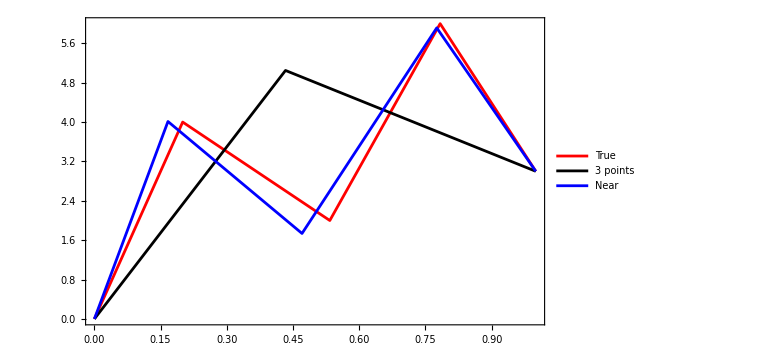

```mathematica
ListLinePlot[{pts5,pts5g3,pts5near},Frame->True,
PlotRange->All,PlotStyle->{Red,Black,Blue},
PlotLegends->{"True","3 points","Near"},
ImageSize->Large]
```

### Sin

#### Plot and Signatures

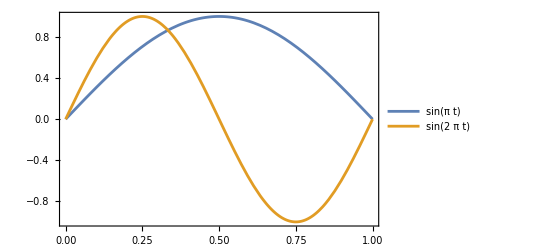

```mathematica
Plot[{Sin[π t],Sin[2π t]},{t,0,1},
Frame->True,PlotRange->All,
PlotLegends->"Expressions"]
```

```mathematica
Timing[sigsins=signat[{{t,Sin[π t]},{t,Sin[2π t]}},{0,1},5]]
```

{140.4,{{{1},{1,0},{{1/2,-2/π},{2/π,0}},{{{1/6,-1/π},{0,1/4}},{{1/π,-1/2},{1/4,0}}},{{{{1/24,-(-4+π^2)/(2 π^3)},{(-12+π^2)/(2 π^3),1/8}},{{-(-12+π^2)/(2 π^3),-1/4+2/π^2},{1/4-2/π^2,-2/(9 π)}}},{{{(-4+π^2)/(2 π^3),-2/π^2},{-1/4+2/π^2,2/(3 π)}},{{1/8,-2/(3 π)},{2/(9 π),0}}}},{{{{{1/120,1/π^3-1/(6 π)},{(-12+π^2)/(6 π^3),1/48 (2-3/π^2)}},{{0,-1/12+7/(8 π^2)},{1/48 (4-33/π^2),-1/(9 π)}}},{{{-(-12+π^2)/(6 π^3),-1/(4 π^2)},{-1/12+3/(4 π^2),1/(12 π)}},{{1/48 (4-33/π^2),-1/(12 π)},{0,1/64}}}},{{{{(-6+π^2)/(6 π^3),-1/(2 π^2)},{-1/(4 π^2),1/(4 π)}},{{-1/12+7/(8 π^2),0},{1/(12 π),-1/16}}},{{{1/48 (2-3/π^2),-1/(4 π)},{-1/(12 π),3/32}},{{1/(9 π),-1/16},{1/64,0}}}}}},{{1},{1,0},{{1/2,0},{0,0}},{{{1/6,1/(2 π)},{-1/π,1/4}},{{1/(2 π),-1/2},{1/4,0}}},{{{{1/24,1/(4 π)},{-1/(4 π),1/8}},{{-1/(4 π),-1/4},{1/4,0}}},{{{1/(4 π),0},{-1/4,0}},{{1/8,0},{0,0}}}},{{{{{1/120,(-3+2 π^2)/(24 π^3)},{-(-6+π^2)/(12 π^3),1/24-1/(64 π^2)}},{{-3/(4 π^3),-1/12+7/(32 π^2)},{1/12-11/(64 π^2),1/(18 π)}}},{{{-(-6+π^2)/(12 π^3),-9/(16 π^2)},{1/48 (-4+33/π^2),-7/(24 π)}},{{1/12-11/(64 π^2),13/(24 π)},{-13/(36 π),1/64}}}},{{{{(-3+2 π^2)/(24 π^3),3/(8 π^2)},{-9/(16 π^2),1/(8 π)}},{{-1/12+7/(32 π^2),-1/(2 π)},{13/(24 π),-1/16}}},{{{1/24-1/(64 π^2),1/(8 π)},{-7/(24 π),3/32}},{{1/(18 π),-1/16},{1/64,0}}}}}}}}

```mathematica
{sigsins1f,sigsins2f}=sigsins;
```

```mathematica
Length[sigsins1f]
```

6

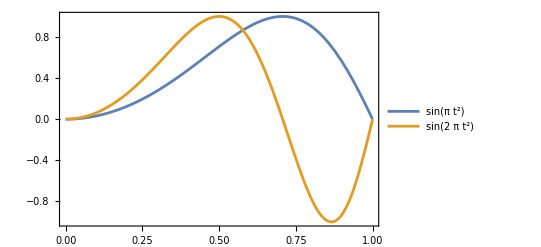

```mathematica
Plot[{Sin[π t^2],Sin[2π t^2]},{t,0,1},
Frame->True,PlotRange->All,
PlotLegends->"Expressions"]
```

```mathematica
Timing[sigsins2=signat[{{t,Sin[π t^2]},{t,Sin[2π t^2]}},{0,1},4]]
```

{44.915,{{{1},{1,0},{{1/2,-FresnelS[√2]/(√2)},{FresnelS[√2]/(√2),0}},{{{1/6,-1/π},{2/π-FresnelS[√2]/(√2),1/8 (2-FresnelC[2])}},{{-1/π+FresnelS[√2]/(√2),1/4 (-2+FresnelC[2])},{1/8 (2-FresnelC[2]),0}}},{{{{1/24,-(2+√2 FresnelC[√2])/(8 π)},{(-2+3 √2 FresnelC[√2])/(8 π),1/8}},{{(10-3 √2 FresnelC[√2]-2 √2 π FresnelS[√2])/(8 π),1/4 (-1+FresnelS[√2]^2)},{1/8 (2-FresnelC[2]-2 FresnelS[√2]^2),1/144 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])}}},{{{(-6+√2 FresnelC[√2]+2 √2 π FresnelS[√2])/(8 π),-1/4 FresnelS[√2]^2},{1/4 (-1+FresnelC[2]+FresnelS[√2]^2),1/48 (9 √2 FresnelS[√2]-√6 FresnelS[√6])}},{{1/8 (1-FresnelC[2]),1/48 (-9 √2 FresnelS[√2]+√6 FresnelS[√6])},{(3 √3 FresnelS[√2]-FresnelS[√6])/(24 √6),0}}}}},{{1},{1,0},{{1/2,-FresnelS[2]/2},{FresnelS[2]/2,0}},{{{1/6,0},{-FresnelS[2]/2,1/16 (4-√2 FresnelC[2 √2])}},{{FresnelS[2]/2,1/8 (-4+√2 FresnelC[2 √2])},{1/16 (4-√2 FresnelC[2 √2]),0}}},{{{{1/24,-(-2+FresnelC[2])/(16 π)},{(3 (-2+FresnelC[2]))/(16 π),1/8}},{{(6-3 FresnelC[2]-4 π FresnelS[2])/(16 π),1/8 (-2+FresnelS[2]^2)},{1/16 (4-√2 FresnelC[2 √2]-2 FresnelS[2]^2),1/144 (-9 FresnelS[2]+√3 FresnelS[2 √3])}}},{{{(-2+FresnelC[2]+4 π FresnelS[2])/(16 π),-1/8 FresnelS[2]^2},{1/8 (-2+√2 FresnelC[2 √2]+FresnelS[2]^2),1/48 (9 FresnelS[2]-√3 FresnelS[2 √3])}},{{1/16 (2-√2 FresnelC[2 √2]),1/48 (-9 FresnelS[2]+√3 FresnelS[2 √3])},{1/144 (9 FresnelS[2]-√3 FresnelS[2 √3]),0}}}}}}}

```mathematica
{sigsins1f2,sigsins2f2}=sigsins2;
```

#### 3 points

```mathematica
solvesigsN[sig3,sigsins1f,{{1,2,2}}]
```

{{δx→0.,δt_1→0.5,δx_1→1.27324}}

```mathematica
solvesigsN[sig3,sigsins1f2,{{1,2,2}}]
```

{{δx→0.,δt_1→0.891494,δx_1→1.00971}}

```mathematica
{N[4/π],N[2 FresnelS[√2]/(√2)]}
```

{1.27324,1.00971}

```mathematica
solvesigsN[sig3,sigsins2f,{{2}}]
```

{{δt_1→0.607927,δx_1→-2.52573,δx→-1.5708}}

```mathematica
solvesigsN[sig3,sigsins2f,{{1,2}}]
```

{}

```mathematica
solvesigsN[sig3,sigsins2f,{{1,1,2}}]
```

{}

```mathematica
solvesigsN[sig3,sigsins2f,{{1,2,2}}]
```

{}

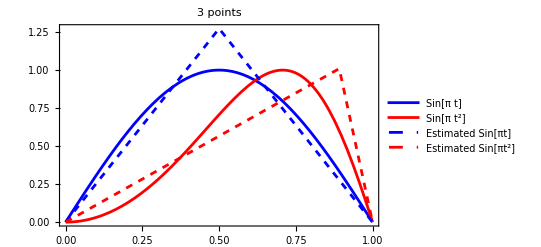

```mathematica
Show[Plot[{Sin[π t],Sin[π t^2]},{t,0,1},
Frame->True,PlotRange->All,PlotStyle->{Blue,Red},
PlotLegends->"Expressions",PlotLabel->"3 points"],
ListLinePlot[{
{{0,0},{1/2,4/π},{1,0}},
{{0,0},{0.8914944415388137,1.009709188227373},{1,0}}},
PlotStyle->{{Dashed,Blue},{Dashed,Red}},
PlotLegends->{"Estimated Sin[πt]","Estimated Sin[πt^2]"}]]
```

#### 4 points

```mathematica
solvesigsN[sig4,sigsins1f,{{1,1,1,2},{1,2,2,2}},4,4]
```

{{δx→0.,δt_1→0.311903,δx_1→0.925189,δt_2→0.376193,δx_2→0},{δx→0.,δt_1→0.311903,δx_1→0.925189,δt_2→0.376193,δx_2→0},{δx→0.,δt_1→0.311903,δx_1→0.925189,δt_2→0.376193,δx_2→0}}

```mathematica
solvesigsN[sig4,sigsins1f2,{{1,1,1,2},{1,1,2,2}},4,4]
```

{{δx→0.,δt_1→0.00379522,δx_1→-0.122195,δt_2→0.788072,δx_2→1.23288},{δx→0.,δt_1→0.00379522,δx_1→-0.122195,δt_2→0.788072,δx_2→1.23288},{δx→0.,δt_1→0.00379522,δx_1→-0.122195,δt_2→0.788072,δx_2→1.23288},{δx→0.,δt_1→0.00379522,δx_1→-0.122195,δt_2→0.788072,δx_2→1.23288},{δx→0.,δt_1→0.00379522,δx_1→-0.122195,δt_2→0.788072,δx_2→1.23288},{δx→0.,δt_1→0.00379522,δx_1→-0.122195,δt_2→0.788072,δx_2→1.23288}}

```mathematica
solvesigsN[sig4,sigsins2f,{},4,4]
```

{{δt_1→0.220303,δx_1→1.22474,δt_2→0.559394,δx_2→-2.44949,δx→0.}}

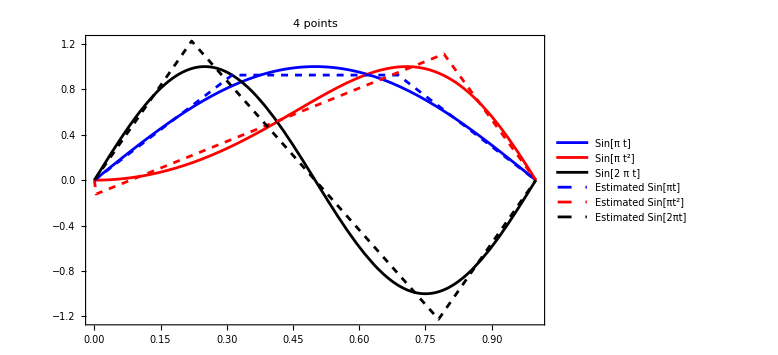

```mathematica
Show[Plot[{Sin[π t],Sin[π t^2],Sin[2π t]},{t,0,1},
Frame->True,PlotRange->All,PlotStyle->{Blue,Red,Black},ImageSize->Large,
PlotLegends->"Expressions",PlotLabel->"4 points"],
ListLinePlot[{
{{0,0},{0.31190326327551826,0.9251893496807685},{0.31190326327551826,0.9251893496807685}+{0.37619347344896714,0},{1,0}},
{{0,0},{0.003795223985323593,-0.12219543654389427},{0.003795223985323593,-0.12219543654389427}+{0.7880718969102517,1.232882479399091},{1,0}},
{{0,0},{0.22030319876632395,1.224744871391589},{0.22030319876632395,1.224744871391589}+{0.559393602467352,-2.449489742783178},{1,0}}},
PlotStyle->{{Dashed,Blue},{Dashed,Red},{Dashed,Black}},
PlotLegends->{"Estimated Sin[πt]","Estimated Sin[πt^2]","Estimated Sin[2πt]"}]]
```

#### 6 points

### Circle

#### Plot and Signatures

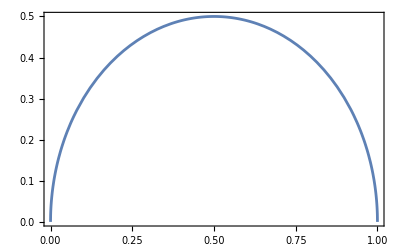

```mathematica
Plot[√(1/4-(t-1/2)^2),{t,0,1},
Frame->True,PlotRange->All]
```

```mathematica
Timing[sigcircle=signat[{{t,√(1/4-(t-1/2)^2)}},{0,1},5]]
```

$Aborted

#### 3 points

```mathematica
Timing[solscircle3pts=Solve[{
sig3[[2,2]]==sigcircle[[2,2]],
sig3[[3,1,2]]==sigcircle[[3,1,2]],
sig3[[4,1,1,2]]==sigcircle[[4,1,1,2]],
0<δt1<1},
{δt1,δx1,δx}]]
```

{0.001405,{{δt1→1/2,δx1→4/π,δx→0}}}

```mathematica
Timing[solssin2f3pts=NSolve[{
sig3[[2,2]]==sigsins2f[[2,2]],
sig3[[3,1,2]]==sigsins2f[[3,1,2]],
sig3[[4,1,1,2]]==sigsins2f[[4,1,1,2]],
sig3[[4,1,2,2]]==sigsins2f[[4,1,2,2]],
0<δt1<1},
{δt1,δx1,δx}]]
```

{0.004884,{}}

```mathematica
Timing[solssin2f3pts=NSolve[{
sig3[[2,2]]==sigsins2f[[2,2]],
sig3[[4,1,1,2]]==sigsins2f[[4,1,1,2]],
sig3[[4,1,2,2]]==sigsins2f[[4,1,2,2]]},
{δt1,δx1,δx}]]
```

{0.005798,{{δx→0.,δt1→-0.220303,δx1→-1.22474},{δx→0.,δt1→-1.7797,δx1→1.22474}}}

```mathematica
Timing[solssin2f3pts=NSolve[{
sig3[[2,2]]==sigsins2f[[2,2]],
sig3[[3,1,2]]==sigsins2f[[3,1,2]],
sig3[[4,1,2,2]]==sigsins2f[[4,1,2,2]],
0<δt1<1},
{δt1,δx1,δx}]]
```

{0.006735,{}}

```mathematica
Timing[solssin2f3pts=NSolve[{
sig3[[2,2]]==sigsins2f[[2,2]],
sig3[[3,1,2]]==sigsins2f[[3,1,2]],
sig3[[4,1,1,2]]==sigsins2f[[4,1,1,2]],
0<δt1<1},
{δt1,δx1,δx}]]
```

{0.004385,{}}

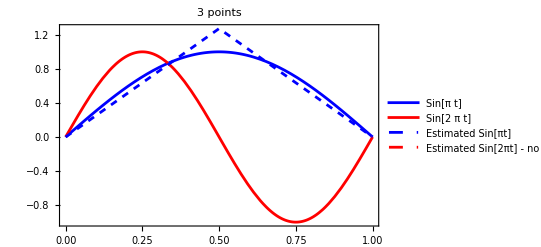

```mathematica
Show[Plot[{Sin[π t],Sin[2π t]},{t,0,1},
Frame->True,PlotRange->All,PlotStyle->{Blue,Red},
PlotLegends->"Expressions",PlotLabel->"3 points"],
ListLinePlot[{
{{0,0},{1/2,4/π},{1,0}},
{{0,0}}},
PlotStyle->{{Dashed,Blue},{Dashed,Red}},
PlotLegends->{"Estimated Sin[πt]","Estimated Sin[2πt] - no solution"}]]
```

#### 4 points

```mathematica
Timing[solssin1f4pts=NSolve[{
sig4[[2,2]]==sigsins1f[[2,2]],
sig4[[3,1,2]]==sigsins1f[[3,1,2]],
sig4[[4,1,1,2]]==sigsins1f[[4,1,1,2]],
sig4[[4,1,2,2]]==sigsins1f[[4,1,2,2]],
sig4[[5,1,1,1,2]]==sigsins1f[[5,1,1,1,2]],
sig4[[5,1,1,2,2]]==sigsins1f[[5,1,1,2,2]],
sig4[[5,1,2,2,2]]==sigsins1f[[5,1,2,2,2]],
0<δt1<1,
0<δt2<1,
0<δt1+δt2<1},
{δt1,δx1,δt2,δx2,δx},Reals]]
```

{0.016998,{}}

```mathematica
Timing[solssin1f4pts=NSolve[{
sig4[[2,2]]==sigsins1f[[2,2]],
sig4[[3,1,2]]==sigsins1f[[3,1,2]],
sig4[[4,1,1,2]]==sigsins1f[[4,1,1,2]],
sig4[[4,1,2,2]]==sigsins1f[[4,1,2,2]],
sig4[[5,1,1,2,2]]==sigsins1f[[5,1,1,2,2]],
0<δt1<1,
0<δt2<1,
0<δt1+δt2<1},
{δt1,δx1,δt2,δx2,δx},Reals]]
```

{0.428544,{{δx→0,δt1→0.311903,δx1→0.925189,δt2→0.376193,δx2→0},{δx→0,δt1→0.311903,δx1→0.925189,δt2→0.376193,δx2→0},{δx→0,δt1→0.311903,δx1→0.925189,δt2→0.376193,δx2→0}}}

```mathematica
Timing[solssin1f4pts=NSolve[{
sig4[[2,2]]==sigsins1f[[2,2]],
sig4[[3,1,2]]==sigsins1f[[3,1,2]],
sig4[[4,1,1,2]]==sigsins1f[[4,1,1,2]],
sig4[[4,1,2,2]]==sigsins1f[[4,1,2,2]],
sig4[[5,1,2,2,2]]==sigsins1f[[5,1,2,2,2]],
0<δt1<1,
0<δt2<1,
0<δt1+δt2<1},
{δt1,δx1,δt2,δx2,δx},Reals]]
```

{0.454553,{{δx→0,δt1→0.372343,δx1→1.0676,δt2→0.418048,δx2→-0.383431},{δx→0,δt1→0.372343,δx1→1.0676,δt2→0.418048,δx2→-0.383431},{δx→0,δt1→0.372343,δx1→1.0676,δt2→0.418048,δx2→-0.383431},{δx→0,δt1→0.20961,δx1→0.684165,δt2→0.418048,δx2→0.383431},{δx→0,δt1→0.20961,δx1→0.684165,δt2→0.418048,δx2→0.383431},{δx→0,δt1→0.20961,δx1→0.684165,δt2→0.418048,δx2→0.383431},{δx→0,δt1→0.20961,δx1→0.684165,δt2→0.418048,δx2→0.383431},{δx→0,δt1→0.20961,δx1→0.684165,δt2→0.418048,δx2→0.383431}}}

```mathematica
Timing[solssin2f4pts=NSolve[{
sig4[[2,2]]==sigsins2f[[2,2]],
sig4[[3,1,2]]==sigsins2f[[3,1,2]],
sig4[[4,1,1,2]]==sigsins2f[[4,1,1,2]],
sig4[[4,1,2,2]]==sigsins2f[[4,1,2,2]],
sig4[[5,1,1,1,2]]==sigsins2f[[5,1,1,1,2]],
sig4[[5,1,1,2,2]]==sigsins2f[[5,1,1,2,2]],
sig4[[5,1,2,2,2]]==sigsins2f[[5,1,2,2,2]],
0<δt1<1,
0<δt2<1,
0<δt1+δt2<1},
{δt1,δx1,δt2,δx2,δx},Reals]]
```

{0.025962,{{δt1→0.220303,δx1→1.22474,δt2→0.559394,δx2→-2.44949,δx→0.}}}

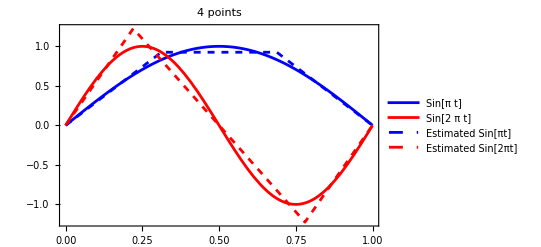

```mathematica
Show[Plot[{Sin[π t],Sin[2π t]},{t,0,1},
Frame->True,PlotRange->All,PlotStyle->{Blue,Red},
PlotLegends->"Expressions",PlotLabel->"4 points"],
ListLinePlot[{
{{0,0},{0.31190326327551826,0.9251893496807685},{0.31190326327551826,0.9251893496807685}+{0.37619347344896714,0},{1,0}},
{{0,0},{0.22030319876632395,1.224744871391589},{0.22030319876632395,1.224744871391589}+{0.559393602467352,-2.449489742783178},{1,0}}},
PlotStyle->{{Dashed,Blue},{Dashed,Red}},
PlotLegends->{"Estimated Sin[πt]","Estimated Sin[2πt]"}]]
```

#### 5 points

## Other stuff

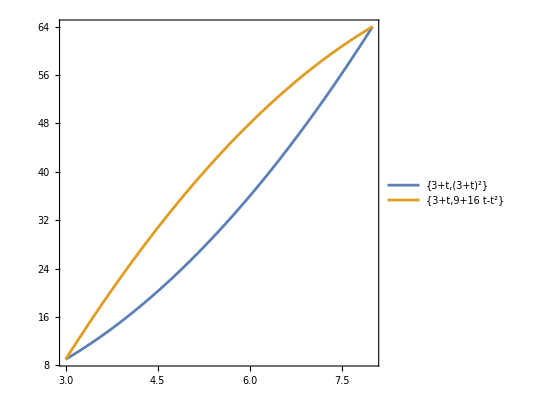

```mathematica
ParametricPlot[{{3+t,(3+t)^2},{3+t,9+16t-t^2}},{t,0,5},
Frame->True,AspectRatio->1,PlotLegends->"Expressions"]
```

```mathematica
D[{{3+t,(3+t)^2},{3+t,9+16t-t^2}},t]
```

{{1,2 (3+t)},{1,16-2 t}}

```mathematica
Grid[signat[{{t,0}},{0,1},4],Frame->All]
```

{1,0} | {1/2,0,0,0} | {1/6,0,0,0,0,0,0,0} | {1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Grid[signat[{{0,t}},{0,1},4],Frame->All]
```

{0,1} | {0,0,0,1/2} | {0,0,0,0,0,0,0,1/6} | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/24}

```mathematica
Grid[signat[{{1,t-1}},{1,2},4],Frame->All]
```

{0,1} | {0,0,0,1/2} | {0,0,0,0,0,0,0,1/6} | {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1/24}

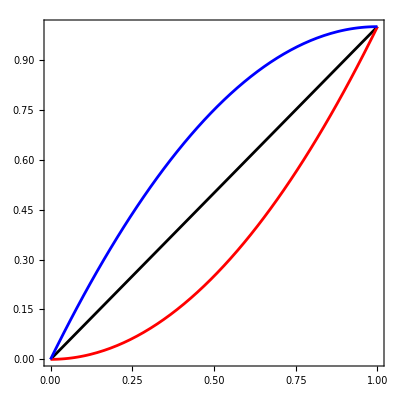

```mathematica
Plot[{x,x^2,1-(1-x)^(2)},{x,0,1},PlotRange->All,
Frame->True,AspectRatio->1,
PlotStyle->{Black,Red,Blue}]
```

```mathematica
Grid[signat[{{t,t},{t,t^2},{t,1-(1-t)^2}},{0,1},4],Frame->All]
```

{1,1} | {1/2,1/2,1/2,1/2} | {1/6,1/6,1/6,1/6,1/6,1/6,1/6,1/6} | {1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24,1/24}
{1,1} | {1/2,2/3,1/3,1/2} | {1/6,1/4,1/6,4/15,1/12,2/15,1/10,1/6} | {1/24,1/15,1/20,1/12,1/30,1/18,2/45,8/105,1/60,1/36,1/45,4/105,1/60,1/35,1/42,1/24}
{1,1} | {1/2,1/3,2/3,1/2} | {1/6,1/12,1/6,1/10,1/4,2/15,4/15,1/6} | {1/24,1/60,1/30,1/60,1/20,1/45,2/45,1/42,1/15,1/36,1/18,1/35,1/12,4/105,8/105,1/24}

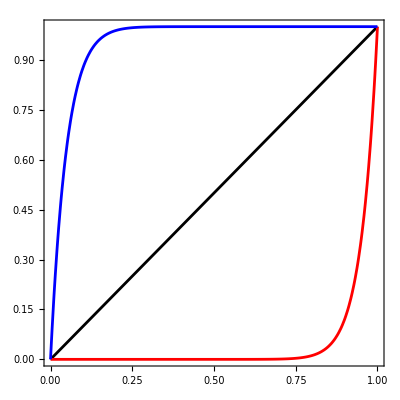

```mathematica
Plot[{x,x^20,1-(1-x)^(20)},{x,0,1},PlotRange->All,
Frame->True,AspectRatio->1,
PlotStyle->{Black,Red,Blue}]
```

```mathematica
Grid[signat[{{t,t^20},{t,1-(1-t)^20}},{0,1}],Frame->All]
```

{1,1} | {1/2,20/21,1/21,1/2} | {1/6,5/11,10/231,400/861,1/462,20/861,1/82,1/6}
{1,1} | {1/2,1/21,20/21,1/2} | {1/6,1/462,10/231,1/82,5/11,20/861,400/861,1/6}

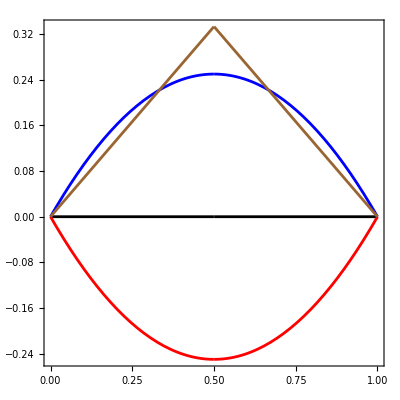

```mathematica
Plot[{x-x,x^2-x,1-(1-x)^(2)-x,1/3 UnitTriangle[2x-1]},{x,0,1},PlotRange->All,
Frame->True,AspectRatio->1,
PlotStyle->{Black,Red,Blue,Brown}]
```

```mathematica
Refine[Grid[signat[{{t,t-t},{t,t^2-t},{t,1-(1-t)^2-t},{t,1/3 UnitTriangle[2t-1]}},{0,1},4],Frame->All],Subscript[t, 1]≥0&&Subscript[t, 2]≥0&&Subscript[t, 3]≥0&&Subscript[t, 4]≥0]
```

Integrate::pwrl: Unable to prove that integration limits {0,t_2} are real. Adding assumptions may help.

Integrate::pwrl: Unable to prove that integration limits {0,t_3} are real. Adding assumptions may help.

General::stop: Further output of Integrate::pwrl will be suppressed during this calculation.

{1,0} | {1/2,0,0,0} | {1/6,0,0,0,0,0,0,0} | {1/24,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
{1,0} | {1/2,1/6,-1/6,0} | {1/6,1/12,0,1/60,-1/12,-1/30,1/60,0} | {1/24,1/40,1/120,1/120,-1/120,-1/360,1/360,1/840,-1/40,-1/72,-1/360,-1/280,1/120,1/280,-1/840,0}
{1,0} | {1/2,-1/6,1/6,0} | {1/6,-1/12,0,1/60,1/12,-1/30,1/60,0} | {1/24,-1/40,-1/120,1/120,1/120,-1/360,1/360,-1/840,1/40,-1/72,-1/360,1/280,1/120,-1/280,1/840,0}
{1,0} | {1/2,-1/6,1/6,0} | {1/6,-1/12,0,1/54,1/12,-1/27,1/54,0} | {1/24,-7/288,-1/96,1/108,1/96,-1/216,1/216,-1/648,7/288,-1/72,-1/216,1/216,1/108,-1/216,1/648,0}

```mathematica
M[α_,n_]:=Module[{d},d=Divisors[n];
1/n Total[Map[(MoebiusMu[n/#] α^#)&,d]]];
```

```mathematica
GN[α_,n_]:=Module[{d},d=Divisors[n];
Total[Map[M[α,#]&,d]]];
```

```mathematica
Table[M[α,n],{n,1,6}]
```

{α,1/2 (-α+α^2),1/3 (-α+α^3),1/4 (-α^2+α^4),1/5 (-α+α^5),1/6 (α-α^2-α^3+α^6)}

```mathematica
Integrate[t^2-t,{t,0,1}]
```

-1/6

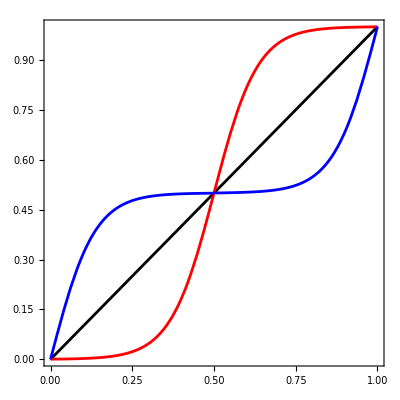

```mathematica
Plot[{x,1/(1+ⅇ^(-15(x-1/2))),1/2-1/(1+ⅇ^(-15((1/2-x)-1/2)))+Piecewise[{{1/(1+ⅇ^(-15(x-1))), x>1/2}, {0, True}}]},{x,0,1},PlotRange->All,
Frame->True,AspectRatio->1,
PlotStyle->{Black,Red,Blue}]
```

```mathematica
Grid[signat[{{t,1/(1+ⅇ^(-15(t-1/2)))},{t,1/2-1/(1+ⅇ^(-15((1/2-t)-1/2)))+Piecewise[{{1/(1+ⅇ^(-15(t-1))), t>1/2}, {0, True}}]}},{0,1},1],Frame->All]
```

{1,(-1+ⅇ^(15/2))/(1+ⅇ^(15/2))}
{1,(-1+ⅇ^(45/2))/((1+ⅇ^(15/2)) (1+ⅇ^15))}